# Even-parity Perturbations of generalized Einstein-Maxwell-scalar black holes

## Part of the paper: arXiv: 2100.XXXX Authors: Yolbeiker Rodríguez Baez and Radouane Gannouji

In this notebook we give the coefficients of the second-order Lagrangian for even-parity perturbations for a theory given by the action
-Graphics-
where R is the scalar curvature, g is the determinant of the metric, ϕ is a scalar field and X is the kinetic term, and F=∂_μ A_ν - ∂_ν A_μ  where A_μ is a vector field.
The metric ansatz is

-Graphics-

As shown in the paper, we get the second-order Lagrangian

```mathematica
ClearAll["Global`*"]
```

```mathematica
SecOrdℒ  = α1[r](Derivative[1,0][q][t,r])^2+ β1[r](Derivative[0,1][q][t,r])^2+γ1[r] q[t,r]^2 +
		 α2[r](Derivative[1,0][H][t,r])^2+ β2[r](Derivative[0,1][H][t,r])^2+γ2[r] H[t,r]^2 +
		 α3[r](Derivative[1,0][S][t,r])^2+ β3[r](Derivative[0,1][S][t,r])^2+γ3[r] S[t,r]^2 +
		σ1[r]q[t,r]H[t,r]+σ2[r]Derivative[0,1][q][t,r]H[t,r]-σ2[r]q[t,r]Derivative[0,1][H][t,r]+σ3[r]Derivative[0,1][q][t,r]Derivative[0,1][H][t,r]+σ4[r]Derivative[1,0][q][t,r]Derivative[1,0][H][t,r] +
		δ1[r]q[t,r]S[t,r]+δ3[r]Derivative[0,1][q][t,r]S[t,r]-δ3[r]q[t,r]Derivative[0,1][S][t,r]+δ4[r]Derivative[0,1][q][t,r]Derivative[0,1][S][t,r]+δ5[r]Derivative[1,0][q][t,r]Derivative[1,0][S][t,r]+
		ν1[r]H[t,r]S[t,r]+ν2[r]S[t,r]Derivative[0,1][H][t,r]-ν2[r]H[t,r]Derivative[0,1][S][t,r]+ν3[r]Derivative[0,1][H][t,r]Derivative[0,1][S][t,r]+ν4[r]Derivative[1,0][H][t,r]Derivative[1,0][S][t,r];
```

In matrix form

```mathematica
χvector:=({{q[t,r]}, {H[t,r]}, {S[t,r]}})  (* {{Gravitational DOF}, {Vector DOF}, {Scalar DOF}} *)

matrixK:=({{α1[r], σ4[r]/2, δ5[r]/2}, {σ4[r]/2, α2[r], ν4[r]/2}, {δ5[r]/2, ν4[r]/2, α3[r]}});                   matrixL:=-({{β1[r], σ3[r]/2, δ4[r]/2}, {σ3[r]/2, β2[r], ν3[r]/2}, {δ4[r]/2, ν3[r]/2, β3[r]}})

matrixM:=({{γ1[r], σ1[r]/2, δ1[r]/2}, {σ1[r]/2, γ2[r], ν1[r]/2}, {δ1[r]/2, ν1[r]/2, γ3[r]}});                   matrixD:=({{0, σ2[r], δ3[r]}, {-σ2[r], 0, ν2[r]}, {-δ3[r], -ν2[r], 0}})
```

where we have defined:

### Lagrangian Coefficients

```mathematica
α1[r_]:=(A[r] Τ[r]^2 (√A[r] (-f1[ϕ[r]]+λ P1[r])+𝒢 √B[r] A0'[r]))/(λ √B[r] c[r])
α2[r_]:=(c[r] A0'[r])/(4 𝒢 λ A[r])
α3[r_]:=-(2 Ρ[r]^2)/(λ A[r]^(3/2) √B[r] f1[ϕ[r]])-(A[r]^(3/2) f1[ϕ[r]] Ρ[r]^2 Τ[r]^2)/(λ √B[r] c[r])+(A[r]^(3/2) P1[r] Ρ[r]^2 Τ[r]^2)/(√B[r] c[r])-(Ρ[r]^2 Τ[r] A'[r])/(λ A[r])+(𝒢 A[r] Ρ[r]^2 Τ[r]^2 A0'[r])/(λ c[r])+(Ρ[r]^2 Τ[r] c'[r])/(λ c[r])+(2 √A[r] Ρ[r] Τ[r] f1'[ϕ[r]])/(√B[r])-(2 √A[r] Ρ[r] Τ[r] f1'[ϕ[r]])/(λ √B[r])-(2 c[r] Ρ[r] A'[r] f1'[ϕ[r]])/(λ A[r]^2 f1[ϕ[r]])-(A[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] f1'[ϕ[r]])/λ+A[r] P1[r] Ρ[r] Τ[r]^2 A'[r] f1'[ϕ[r]]-(√B[r] c[r] Ρ[r] Τ[r] A'[r]^2 f1'[ϕ[r]])/(λ A[r]^(3/2))+(2 𝒢 Ρ[r] Τ[r] A0'[r] f1'[ϕ[r]])/(λ f1[ϕ[r]])+(𝒢 √A[r] √B[r] Ρ[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]])/λ+(2 Ρ[r] c'[r] f1'[ϕ[r]])/(λ A[r] f1[ϕ[r]])+(A[r]^2 f1[ϕ[r]] Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]])/(λ c[r])-(A[r]^2 P1[r] Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]])/c[r]+(2 √B[r] Ρ[r] Τ[r] A'[r] c'[r] f1'[ϕ[r]])/(λ √A[r])-(𝒢 A[r]^(3/2) √B[r] Ρ[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]])/(λ c[r])-(√A[r] √B[r] Ρ[r] Τ[r] c'[r]^2 f1'[ϕ[r]])/(λ c[r])+(2 c[r] f1'[ϕ[r]]^2)/(√A[r] √B[r] f1[ϕ[r]])-(c[r] f1'[ϕ[r]]^2)/(λ √A[r] √B[r] f1[ϕ[r]])+c[r] Τ[r] A'[r] f1'[ϕ[r]]^2-(c[r] Τ[r] A'[r] f1'[ϕ[r]]^2)/λ-(√B[r] c[r]^2 A'[r]^2 f1'[ϕ[r]]^2)/(2 λ A[r]^(5/2) f1[ϕ[r]])-(√A[r] √B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^2)/(4 λ)+1/4 √A[r] √B[r] c[r] P1[r] Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^2-(B[r] c[r]^2 Τ[r] A'[r]^3 f1'[ϕ[r]]^2)/(4 λ A[r]^2)+(𝒢 c[r] A0'[r] f1'[ϕ[r]]^2)/(λ A[r] f1[ϕ[r]]^2)+(𝒢 √B[r] c[r] Τ[r] A'[r] A0'[r] f1'[ϕ[r]]^2)/(λ √A[r] f1[ϕ[r]])+(𝒢 B[r] c[r] Τ[r]^2 A'[r]^2 A0'[r] f1'[ϕ[r]]^2)/(4 λ)-A[r] Τ[r] c'[r] f1'[ϕ[r]]^2+(A[r] Τ[r] c'[r] f1'[ϕ[r]]^2)/λ+(√B[r] c[r] A'[r] c'[r] f1'[ϕ[r]]^2)/(λ A[r]^(3/2) f1[ϕ[r]])+(A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2)/(2 λ)-1/2 A[r]^(3/2) √B[r] P1[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2+(3 B[r] c[r] Τ[r] A'[r]^2 c'[r] f1'[ϕ[r]]^2)/(4 λ A[r])-(𝒢 √A[r] √B[r] Τ[r] A0'[r] c'[r] f1'[ϕ[r]]^2)/(λ f1[ϕ[r]])-(𝒢 A[r] B[r] Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]]^2)/(2 λ)-(√B[r] c'[r]^2 f1'[ϕ[r]]^2)/(2 λ √A[r] f1[ϕ[r]])-(A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2)/(4 λ c[r])+(A[r]^(5/2) √B[r] P1[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2)/(4 c[r])-(3 B[r] Τ[r] A'[r] c'[r]^2 f1'[ϕ[r]]^2)/(4 λ)+(𝒢 A[r]^2 B[r] Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]]^2)/(4 λ c[r])+(A[r] B[r] Τ[r] c'[r]^3 f1'[ϕ[r]]^2)/(4 λ c[r])+𝒥[r]/(A[r] B[r] ϕ'[r])-(2 c[r] Ρ[r] f1'[ϕ[r]]^2 ϕ'[r])/(λ A[r] f1[ϕ[r]]^2)-(√B[r] c[r] Ρ[r] Τ[r] A'[r] f1'[ϕ[r]]^2 ϕ'[r])/(λ √A[r] f1[ϕ[r]])+(√A[r] √B[r] Ρ[r] Τ[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(λ f1[ϕ[r]])-(√B[r] c[r]^2 A'[r] f1'[ϕ[r]]^3 ϕ'[r])/(λ A[r]^(3/2) f1[ϕ[r]]^2)-(B[r] c[r]^2 Τ[r] A'[r]^2 f1'[ϕ[r]]^3 ϕ'[r])/(2 λ A[r] f1[ϕ[r]])+(√B[r] c[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(λ √A[r] f1[ϕ[r]]^2)+(B[r] c[r] Τ[r] A'[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(λ f1[ϕ[r]])-(A[r] B[r] Τ[r] c'[r]^2 f1'[ϕ[r]]^3 ϕ'[r])/(2 λ f1[ϕ[r]])+(2 c[r] Ρ[r] ϕ'[r] f1''[ϕ[r]])/(λ A[r] f1[ϕ[r]])+(√B[r] c[r] Ρ[r] Τ[r] A'[r] ϕ'[r] f1''[ϕ[r]])/(λ √A[r])-(√A[r] √B[r] Ρ[r] Τ[r] c'[r] ϕ'[r] f1''[ϕ[r]])/λ+(√B[r] c[r]^2 A'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(λ A[r]^(3/2) f1[ϕ[r]])+(B[r] c[r]^2 Τ[r] A'[r]^2 f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(2 λ A[r])-(√B[r] c[r] c'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(λ √A[r] f1[ϕ[r]])-(B[r] c[r] Τ[r] A'[r] c'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/λ+(A[r] B[r] Τ[r] c'[r]^2 f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(2 λ)
```

```mathematica
β1[r_]:=(A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2)/(λ c[r])+(A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2)/(√B[r] ℱ[r] Ξ[r]^2)+(2 A[r]^(5/2) c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2)/(√B[r] Ξ[r]^2)-(𝒢 A[r]^2 B[r] Τ[r]^2 A0'[r])/(λ c[r])-(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r])/(2 c[r] Ξ[r])-(2 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]] ϕ'[r])/Ξ[r]+(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r])/(2 Ξ[r]^2)

β2[r_]:=-(B[r] c[r] A0'[r])/(4 𝒢 λ)

β3[r_]:=(A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r]^2 Τ[r]^2)/(λ c[r])+(A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r]^2 Τ[r]^2)/(√B[r] ℱ[r] Ξ[r]^2)+(2 A[r]^(5/2) c[r] f1[ϕ[r]]^2 Ρ[r]^2 Σ[r] Τ[r]^2)/(√B[r] Ξ[r]^2)-(𝒢 A[r]^2 B[r] Ρ[r]^2 Τ[r]^2 A0'[r])/(λ c[r])-(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r]^2 Τ[r]^2 c'[r])/(2 c[r] Ξ[r])-2 A[r]^(3/2) √B[r] Ρ[r] Τ[r] f1'[ϕ[r]]+(2 A[r]^(3/2) √B[r] Ρ[r] Τ[r] f1'[ϕ[r]])/λ+(A[r]^2 B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] f1'[ϕ[r]])/λ+(A[r]^2 c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 A'[r] f1'[ϕ[r]])/(ℱ[r] Ξ[r]^2)+(2 A[r]^2 c[r]^2 f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 A'[r] f1'[ϕ[r]])/Ξ[r]^2-(2 𝒢 A[r] B[r] Ρ[r] Τ[r] A0'[r] f1'[ϕ[r]])/(λ f1[ϕ[r]])-(𝒢 A[r]^(3/2) B[r]^(3/2) Ρ[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]])/λ+(A[r]^(3/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r] c'[r] f1'[ϕ[r]])/Ξ[r]-(A[r]^3 B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]])/(λ c[r])-(A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]])/(ℱ[r] Ξ[r]^2)-(2 A[r]^3 c[r] f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 c'[r] f1'[ϕ[r]])/Ξ[r]^2-(A[r]^2 B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]])/(2 Ξ[r])+(𝒢 A[r]^(5/2) B[r]^(3/2) Ρ[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]])/(λ c[r])+(A[r]^3 B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]])/(2 c[r] Ξ[r])-(2 √A[r] √B[r] c[r] f1'[ϕ[r]]^2)/f1[ϕ[r]]+(√A[r] √B[r] c[r] f1'[ϕ[r]]^2)/(λ f1[ϕ[r]])-A[r] B[r] c[r] Τ[r] A'[r] f1'[ϕ[r]]^2+(A[r] B[r] c[r] Τ[r] A'[r] f1'[ϕ[r]]^2)/λ+(A[r]^(3/2) B[r]^(3/2) c[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^2)/(4 λ)+(A[r]^(3/2) √B[r] c[r]^3 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^2)/(4 ℱ[r] Ξ[r]^2)+(A[r]^(3/2) √B[r] c[r]^3 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^2)/(2 Ξ[r]^2)-(𝒢 B[r] c[r] A0'[r] f1'[ϕ[r]]^2)/(λ f1[ϕ[r]]^2)-(𝒢 √A[r] B[r]^(3/2) c[r] Τ[r] A'[r] A0'[r] f1'[ϕ[r]]^2)/(λ f1[ϕ[r]])-(𝒢 A[r] B[r]^2 c[r] Τ[r]^2 A'[r]^2 A0'[r] f1'[ϕ[r]]^2)/(4 λ)+A[r]^2 B[r] Τ[r] c'[r] f1'[ϕ[r]]^2-(A[r]^2 B[r] Τ[r] c'[r] f1'[ϕ[r]]^2)/λ+(A[r] B[r] c[r] f1[ϕ[r]] Τ[r] A'[r] c'[r] f1'[ϕ[r]]^2)/(2 Ξ[r])-(A[r]^(5/2) B[r]^(3/2) f1[ϕ[r]] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2)/(2 λ)-(A[r]^(5/2) √B[r] c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2)/(2 ℱ[r] Ξ[r]^2)-(A[r]^(5/2) √B[r] c[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2)/Ξ[r]^2-(A[r]^(3/2) B[r]^(3/2) c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 c'[r] f1'[ϕ[r]]^2)/(8 Ξ[r])+(𝒢 A[r]^(3/2) B[r]^(3/2) Τ[r] A0'[r] c'[r] f1'[ϕ[r]]^2)/(λ f1[ϕ[r]])+(𝒢 A[r]^2 B[r]^2 Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]]^2)/(2 λ)-(A[r]^2 B[r] f1[ϕ[r]] Τ[r] c'[r]^2 f1'[ϕ[r]]^2)/(2 Ξ[r])+(A[r]^(7/2) B[r]^(3/2) f1[ϕ[r]] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2)/(4 λ c[r])+(A[r]^(7/2) √B[r] c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2)/(4 ℱ[r] Ξ[r]^2)+(A[r]^(7/2) √B[r] c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2)/(2 Ξ[r]^2)+(A[r]^(5/2) B[r]^(3/2) f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r]^2 f1'[ϕ[r]]^2)/(4 Ξ[r])-(𝒢 A[r]^3 B[r]^2 Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]]^2)/(4 λ c[r])-(A[r]^(7/2) B[r]^(3/2) f1[ϕ[r]]^2 Τ[r]^2 c'[r]^3 f1'[ϕ[r]]^2)/(8 c[r] Ξ[r])+(√A[r] c[r] ℳ[r]^2)/(√B[r] ℱ[r] ϕ'[r]^2)+(2 √A[r] c[r] Σ[r])/(√B[r] ϕ'[r]^2)+(2 A[r]^(3/2) c[r] f1[ϕ[r]] ℳ[r]^2 Ρ[r] Τ[r])/(√B[r] ℱ[r] Ξ[r] ϕ'[r])+(4 A[r]^(3/2) c[r] f1[ϕ[r]] Ρ[r] Σ[r] Τ[r])/(√B[r] Ξ[r] ϕ'[r])+(A[r] c[r]^2 f1[ϕ[r]] ℳ[r]^2 Τ[r] A'[r] f1'[ϕ[r]])/(ℱ[r] Ξ[r] ϕ'[r])+(2 A[r] c[r]^2 f1[ϕ[r]] Σ[r] Τ[r] A'[r] f1'[ϕ[r]])/(Ξ[r] ϕ'[r])-(A[r]^2 c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] c'[r] f1'[ϕ[r]])/(ℱ[r] Ξ[r] ϕ'[r])-(2 A[r]^2 c[r] f1[ϕ[r]] Σ[r] Τ[r] c'[r] f1'[ϕ[r]])/(Ξ[r] ϕ'[r])-(2 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r]^2 Τ[r]^2 f1'[ϕ[r]] ϕ'[r])/Ξ[r]+(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r]^2 Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r])/(2 Ξ[r]^2)-(2 A[r]^(3/2) √B[r] c[r] Ρ[r] Τ[r] f1'[ϕ[r]]^2 ϕ'[r])/Ξ[r]-(2 A[r]^2 B[r] c[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] f1'[ϕ[r]]^2 ϕ'[r])/Ξ[r]+(2 A[r]^3 B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ'[r])/Ξ[r]+(3 A[r]^2 B[r] c[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(2 Ξ[r]^2)-(3 A[r]^3 B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(2 Ξ[r]^2)-(A[r] B[r] c[r]^2 Τ[r] A'[r] f1'[ϕ[r]]^3 ϕ'[r])/Ξ[r]-(A[r]^(3/2) B[r]^(3/2) c[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^3 ϕ'[r])/(2 Ξ[r])+(A[r]^2 B[r] c[r] Τ[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r])/Ξ[r]+(A[r]^(5/2) B[r]^(3/2) c[r] f1[ϕ[r]] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r])/Ξ[r]+(3 A[r]^(3/2) B[r]^(3/2) c[r]^2 f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(8 Ξ[r]^2)-(A[r]^(7/2) B[r]^(3/2) f1[ϕ[r]] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^3 ϕ'[r])/(2 Ξ[r])-(3 A[r]^(5/2) B[r]^(3/2) c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r]^2 f1'[ϕ[r]]^3 ϕ'[r])/(4 Ξ[r]^2)+(3 A[r]^(7/2) B[r]^(3/2) f1[ϕ[r]]^2 Τ[r]^2 c'[r]^3 f1'[ϕ[r]]^3 ϕ'[r])/(8 Ξ[r]^2)
```

```mathematica
γ1[r_]:=1/(λ √A[r] √B[r] c[r] f1[ϕ[r]])+(A[r] f1[ϕ[r]] Τ[r])/(B[r] c[r] Ξ[r])-(2 A[r]^(5/2) f1[ϕ[r]] Τ[r]^2)/(λ √B[r] c[r]^2)+(A[r]^(5/2) P1[r] Τ[r]^2)/(√B[r] c[r]^2)-(A[r]^(5/2) f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2)/(B[r]^(3/2) ℱ[r] Ξ[r]^2)-(2 A[r]^(5/2) f1[ϕ[r]]^2 Σ[r] Τ[r]^2)/(B[r]^(3/2) Ξ[r]^2)+(Τ[r] A'[r])/(λ c[r])+(A[r]^(3/2) f1[ϕ[r]]^2 Τ[r]^2 A'[r])/(2 √B[r] c[r] Ξ[r])-(λ A[r]^(3/2) f1[ϕ[r]] P1[r] Τ[r]^2 A'[r])/(2 √B[r] c[r] Ξ[r])-(A[r]^3 f1[ϕ[r]]^2 Τ[r]^3 A'[r])/(λ c[r]^2)+(A[r]^3 f1[ϕ[r]] P1[r] Τ[r]^3 A'[r])/c[r]^2-(A[r]^3 f1[ϕ[r]]^3 ℳ[r]^2 Τ[r]^3 A'[r])/(B[r] ℱ[r] Ξ[r]^2)+(λ A[r]^3 f1[ϕ[r]]^2 P1[r] ℳ[r]^2 Τ[r]^3 A'[r])/(B[r] ℱ[r] Ξ[r]^2)-(2 A[r]^3 f1[ϕ[r]]^3 Σ[r] Τ[r]^3 A'[r])/(B[r] Ξ[r]^2)+(2 λ A[r]^3 f1[ϕ[r]]^2 P1[r] Σ[r] Τ[r]^3 A'[r])/(B[r] Ξ[r]^2)-(f1[ϕ[r]] Τ[r] A'[r]^2)/(4 A[r] Ξ[r])+(√A[r] √B[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2)/(4 λ c[r])+(√A[r] c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r]^2)/(4 √B[r] ℱ[r] Ξ[r]^2)+(√A[r] c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r]^2)/(2 √B[r] Ξ[r]^2)-(𝒢 A0'[r])/(λ A[r] c[r] f1[ϕ[r]]^2)-(𝒢 √A[r] Τ[r] A0'[r])/(√B[r] c[r] Ξ[r])+(4 𝒢 A[r]^2 Τ[r]^2 A0'[r])/(λ c[r]^2)-(𝒢 A[r]^2 P1[r] Τ[r]^2 A0'[r])/(c[r]^2 f1[ϕ[r]])+(𝒢 A[r]^2 f1[ϕ[r]] ℳ[r]^2 Τ[r]^2 A0'[r])/(B[r] ℱ[r] Ξ[r]^2)+(2 𝒢 A[r]^2 f1[ϕ[r]] Σ[r] Τ[r]^2 A0'[r])/(B[r] Ξ[r]^2)-(𝒢 √B[r] Τ[r] A'[r] A0'[r])/(2 λ √A[r] c[r] f1[ϕ[r]])-(𝒢 A[r] f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r])/(2 c[r] Ξ[r])+(2 𝒢 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^3 A'[r] A0'[r])/(λ c[r]^2)-(𝒢 A[r]^(5/2) √B[r] P1[r] Τ[r]^3 A'[r] A0'[r])/c[r]^2+(𝒢 A[r]^(5/2) f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^3 A'[r] A0'[r])/(√B[r] ℱ[r] Ξ[r]^2)+(2 𝒢 A[r]^(5/2) f1[ϕ[r]]^2 Σ[r] Τ[r]^3 A'[r] A0'[r])/(√B[r] Ξ[r]^2)-(2 𝒢^2 A[r]^(3/2) √B[r] Τ[r]^2 A0'[r]^2)/(λ c[r]^2 f1[ϕ[r]])-(𝒢^2 A[r]^2 B[r] Τ[r]^3 A'[r] A0'[r]^2)/(λ c[r]^2)+(f1[ϕ[r]] Τ[r] A'[r] B'[r])/(4 B[r] Ξ[r])-(A[r]^(3/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] B'[r])/(2 B[r]^(3/2) ℱ[r] Ξ[r]^2)-(A[r]^(3/2) c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] B'[r])/(B[r]^(3/2) Ξ[r]^2)-(𝒢 √A[r] Τ[r] A0'[r] B'[r])/(2 λ √B[r] c[r] f1[ϕ[r]])-(𝒢 A[r] Τ[r]^2 A'[r] A0'[r] B'[r])/(4 λ c[r])-(A[r] Τ[r] c'[r])/(λ c[r]^2)+(A[r]^(5/2) f1[ϕ[r]]^2 Τ[r]^2 c'[r])/(√B[r] c[r]^2 Ξ[r])-(λ A[r]^(5/2) f1[ϕ[r]] P1[r] Τ[r]^2 c'[r])/(2 √B[r] c[r]^2 Ξ[r])+(A[r]^4 f1[ϕ[r]]^2 Τ[r]^3 c'[r])/(λ c[r]^3)-(A[r]^4 f1[ϕ[r]] P1[r] Τ[r]^3 c'[r])/c[r]^3+(A[r]^4 f1[ϕ[r]]^3 ℳ[r]^2 Τ[r]^3 c'[r])/(B[r] c[r] ℱ[r] Ξ[r]^2)-(λ A[r]^4 f1[ϕ[r]]^2 P1[r] ℳ[r]^2 Τ[r]^3 c'[r])/(B[r] c[r] ℱ[r] Ξ[r]^2)+(2 A[r]^4 f1[ϕ[r]]^3 Σ[r] Τ[r]^3 c'[r])/(B[r] c[r] Ξ[r]^2)-(2 λ A[r]^4 f1[ϕ[r]]^2 P1[r] Σ[r] Τ[r]^3 c'[r])/(B[r] c[r] Ξ[r]^2)-(3 f1[ϕ[r]] Τ[r] A'[r] c'[r])/(4 c[r] Ξ[r])-(A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r]^2 A'[r] c'[r])/(2 λ c[r]^2)+(A[r]^(3/2) f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] c'[r])/(2 √B[r] ℱ[r] Ξ[r]^2)+(A[r]^(3/2) f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] c'[r])/(√B[r] Ξ[r]^2)+(A[r]^3 f1[ϕ[r]]^3 Τ[r]^3 A'[r] c'[r])/(2 c[r]^2 Ξ[r])-(λ A[r]^3 f1[ϕ[r]]^2 P1[r] Τ[r]^3 A'[r] c'[r])/(2 c[r]^2 Ξ[r])-(√A[r] √B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 c'[r])/(4 c[r] Ξ[r])+(𝒢 √A[r] √B[r] Τ[r] A0'[r] c'[r])/(λ c[r]^2 f1[ϕ[r]])-(𝒢 A[r]^2 f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r])/(c[r]^2 Ξ[r])-(2 𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]] Τ[r]^3 A0'[r] c'[r])/(λ c[r]^3)+(𝒢 A[r]^(7/2) √B[r] P1[r] Τ[r]^3 A0'[r] c'[r])/c[r]^3-(𝒢 A[r]^(7/2) f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^3 A0'[r] c'[r])/(√B[r] c[r] ℱ[r] Ξ[r]^2)-(2 𝒢 A[r]^(7/2) f1[ϕ[r]]^2 Σ[r] Τ[r]^3 A0'[r] c'[r])/(√B[r] c[r] Ξ[r]^2)+(𝒢 A[r] B[r] Τ[r]^2 A'[r] A0'[r] c'[r])/(4 λ c[r]^2)-(𝒢 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 A'[r] A0'[r] c'[r])/(2 c[r]^2 Ξ[r])+(𝒢^2 A[r]^3 B[r] Τ[r]^3 A0'[r]^2 c'[r])/(λ c[r]^3)+(A[r] f1[ϕ[r]] Τ[r] B'[r] c'[r])/(4 B[r] c[r] Ξ[r])+(A[r]^(5/2) f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 B'[r] c'[r])/(2 B[r]^(3/2) ℱ[r] Ξ[r]^2)+(A[r]^(5/2) f1[ϕ[r]]^2 Σ[r] Τ[r]^2 B'[r] c'[r])/(B[r]^(3/2) Ξ[r]^2)+(A[r]^(3/2) f1[ϕ[r]]^2 Τ[r]^2 A'[r] B'[r] c'[r])/(8 √B[r] c[r] Ξ[r])+(𝒢 A[r]^2 Τ[r]^2 A0'[r] B'[r] c'[r])/(4 λ c[r]^2)+(A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 c'[r]^2)/(4 λ c[r]^3)-(3 A[r]^(5/2) f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r]^2)/(4 √B[r] c[r] ℱ[r] Ξ[r]^2)-(3 A[r]^(5/2) f1[ϕ[r]]^2 Σ[r] Τ[r]^2 c'[r]^2)/(2 √B[r] c[r] Ξ[r]^2)-(A[r]^4 f1[ϕ[r]]^3 Τ[r]^3 c'[r]^2)/(2 c[r]^3 Ξ[r])+(λ A[r]^4 f1[ϕ[r]]^2 P1[r] Τ[r]^3 c'[r]^2)/(2 c[r]^3 Ξ[r])+(A[r]^(3/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r]^2)/(4 c[r]^2 Ξ[r])-(𝒢 A[r]^2 B[r] Τ[r]^2 A0'[r] c'[r]^2)/(4 λ c[r]^3)+(𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 A0'[r] c'[r]^2)/(2 c[r]^3 Ξ[r])-(A[r]^(5/2) f1[ϕ[r]]^2 Τ[r]^2 B'[r] c'[r]^2)/(8 √B[r] c[r]^2 Ξ[r])-(A[r]^(3/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] ℱ'[r])/(2 √B[r] ℱ[r]^2 Ξ[r]^2)+(A[r]^(5/2) f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r] ℱ'[r])/(2 √B[r] ℱ[r]^2 Ξ[r]^2)+(A[r]^(3/2) c[r] f1[ϕ[r]]^2 ℳ[r] Τ[r]^2 A'[r] ℳ'[r])/(√B[r] ℱ[r] Ξ[r]^2)-(A[r]^(5/2) f1[ϕ[r]]^2 ℳ[r] Τ[r]^2 c'[r] ℳ'[r])/(√B[r] ℱ[r] Ξ[r]^2)+(f1[ϕ[r]] Τ[r] A'[r] Ξ'[r])/(2 Ξ[r]^2)-(A[r]^(3/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] Ξ'[r])/(√B[r] ℱ[r] Ξ[r]^3)-(2 A[r]^(3/2) c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] Ξ'[r])/(√B[r] Ξ[r]^3)+(A[r] f1[ϕ[r]] Τ[r] c'[r] Ξ'[r])/(2 c[r] Ξ[r]^2)+(A[r]^(5/2) f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r] Ξ'[r])/(√B[r] ℱ[r] Ξ[r]^3)+(2 A[r]^(5/2) f1[ϕ[r]]^2 Σ[r] Τ[r]^2 c'[r] Ξ'[r])/(√B[r] Ξ[r]^3)+(A[r]^(3/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] Ξ'[r])/(4 c[r] Ξ[r]^2)-(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 Ξ'[r])/(4 c[r]^2 Ξ[r]^2)+(A[r]^(3/2) c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] Σ'[r])/(√B[r] Ξ[r]^2)-(A[r]^(5/2) f1[ϕ[r]]^2 Τ[r]^2 c'[r] Σ'[r])/(√B[r] Ξ[r]^2)+(√A[r] 𝒥[r] Τ[r] ϕ'[r])/(√B[r] c[r] Ξ[r])+(A[r] f1[ϕ[r]] 𝒥[r] Τ[r]^2 A'[r] ϕ'[r])/(4 c[r] Ξ[r])-(A[r]^2 f1[ϕ[r]] 𝒥[r] Τ[r]^2 c'[r] ϕ'[r])/(4 c[r]^2 Ξ[r])+(3 A[r]^(5/2) f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]] ϕ'[r])/(√B[r] c[r] Ξ[r])-(λ A[r]^(5/2) P1[r] Τ[r]^2 f1'[ϕ[r]] ϕ'[r])/(√B[r] c[r] Ξ[r])-(3 Τ[r] A'[r] f1'[ϕ[r]] ϕ'[r])/(2 Ξ[r])+(A[r]^(3/2) c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r]^2 A'[r] f1'[ϕ[r]] ϕ'[r])/(2 √B[r] ℱ[r] Ξ[r]^2)+(A[r]^(3/2) c[r] f1[ϕ[r]] Σ[r] Τ[r]^2 A'[r] f1'[ϕ[r]] ϕ'[r])/(√B[r] Ξ[r]^2)+(2 A[r]^3 f1[ϕ[r]]^2 Τ[r]^3 A'[r] f1'[ϕ[r]] ϕ'[r])/(c[r] Ξ[r])-(2 λ A[r]^3 f1[ϕ[r]] P1[r] Τ[r]^3 A'[r] f1'[ϕ[r]] ϕ'[r])/(c[r] Ξ[r])-(5 √A[r] √B[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2 f1'[ϕ[r]] ϕ'[r])/(8 Ξ[r])+(𝒢 √A[r] √B[r] Τ[r] A0'[r] f1'[ϕ[r]] ϕ'[r])/(λ c[r] f1[ϕ[r]]^2)-(3 𝒢 A[r]^2 Τ[r]^2 A0'[r] f1'[ϕ[r]] ϕ'[r])/(c[r] Ξ[r])+(𝒢 A[r] B[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]] ϕ'[r])/(2 λ c[r] f1[ϕ[r]])-(2 𝒢 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^3 A'[r] A0'[r] f1'[ϕ[r]] ϕ'[r])/(c[r] Ξ[r])+(A[r] Τ[r] B'[r] f1'[ϕ[r]] ϕ'[r])/(2 B[r] Ξ[r])+(A[r]^(3/2) f1[ϕ[r]] Τ[r]^2 A'[r] B'[r] f1'[ϕ[r]] ϕ'[r])/(8 √B[r] Ξ[r])-(A[r] Τ[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(c[r] Ξ[r])-(3 A[r]^(5/2) f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r])/(2 √B[r] c[r] Ξ[r]^2)-(A[r]^(5/2) f1[ϕ[r]] ℳ[r]^2 Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r])/(2 √B[r] ℱ[r] Ξ[r]^2)-(A[r]^(5/2) f1[ϕ[r]] Σ[r] Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r])/(√B[r] Ξ[r]^2)-(2 A[r]^4 f1[ϕ[r]]^2 Τ[r]^3 c'[r] f1'[ϕ[r]] ϕ'[r])/(c[r]^2 Ξ[r])+(2 λ A[r]^4 f1[ϕ[r]] P1[r] Τ[r]^3 c'[r] f1'[ϕ[r]] ϕ'[r])/(c[r]^2 Ξ[r])-(A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(8 c[r] Ξ[r])-(3 A[r]^3 f1[ϕ[r]]^3 Τ[r]^3 A'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(2 c[r] Ξ[r]^2)+(3 λ A[r]^3 f1[ϕ[r]]^2 P1[r] Τ[r]^3 A'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(2 c[r] Ξ[r]^2)+(3 √A[r] √B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r])/(4 Ξ[r]^2)-(𝒢 A[r]^2 B[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(2 λ c[r]^2 f1[ϕ[r]])+(3 𝒢 A[r]^2 f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(2 c[r] Ξ[r]^2)+(2 𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]] Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(c[r]^2 Ξ[r])+(3 𝒢 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 A'[r] A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(2 c[r] Ξ[r]^2)-(A[r]^(5/2) f1[ϕ[r]] Τ[r]^2 B'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(8 √B[r] c[r] Ξ[r])-(3 A[r]^(3/2) f1[ϕ[r]]^2 Τ[r]^2 A'[r] B'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(8 √B[r] Ξ[r]^2)+(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 c'[r]^2 f1'[ϕ[r]] ϕ'[r])/(4 c[r]^2 Ξ[r])+(3 A[r]^4 f1[ϕ[r]]^3 Τ[r]^3 c'[r]^2 f1'[ϕ[r]] ϕ'[r])/(2 c[r]^2 Ξ[r]^2)-(3 λ A[r]^4 f1[ϕ[r]]^2 P1[r] Τ[r]^3 c'[r]^2 f1'[ϕ[r]] ϕ'[r])/(2 c[r]^2 Ξ[r]^2)-(3 𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 A0'[r] c'[r]^2 f1'[ϕ[r]] ϕ'[r])/(2 c[r]^2 Ξ[r]^2)+(3 A[r]^(5/2) f1[ϕ[r]]^2 Τ[r]^2 B'[r] c'[r]^2 f1'[ϕ[r]] ϕ'[r])/(8 √B[r] c[r] Ξ[r]^2)-(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^3 f1'[ϕ[r]] ϕ'[r])/(4 c[r]^2 Ξ[r]^2)+(A[r] Τ[r] f1'[ϕ[r]] Ξ'[r] ϕ'[r])/Ξ[r]^2+(A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]] Ξ'[r] ϕ'[r])/Ξ[r]^2-(A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]] Ξ'[r] ϕ'[r])/(c[r] Ξ[r]^2)-(3 A[r]^(3/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] Ξ'[r] ϕ'[r])/(2 Ξ[r]^3)+(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]] Ξ'[r] ϕ'[r])/(2 c[r] Ξ[r]^3)-(3 A[r] f1[ϕ[r]] 𝒥[r] Τ[r]^2 A'[r] f1'[ϕ[r]] ϕ'[r]^2)/(4 Ξ[r]^2)+(3 A[r]^2 f1[ϕ[r]] 𝒥[r] Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r]^2)/(4 c[r] Ξ[r]^2)+(3 √A[r] √B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^2 ϕ'[r]^2)/(8 Ξ[r]^2)-(3 A[r]^(3/2) c[r] f1[ϕ[r]] Τ[r]^2 A'[r] B'[r] f1'[ϕ[r]]^2 ϕ'[r]^2)/(8 √B[r] Ξ[r]^2)+(3 A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r]^2)/(8 Ξ[r]^2)+(3 A[r]^(5/2) f1[ϕ[r]] Τ[r]^2 B'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r]^2)/(8 √B[r] Ξ[r]^2)-(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r]^2)/(4 c[r] Ξ[r]^2)-(𝒢 √A[r] √B[r] Τ[r] A0''[r])/(λ c[r] f1[ϕ[r]])-(𝒢 A[r] B[r] Τ[r]^2 A'[r] A0''[r])/(2 λ c[r])+(𝒢 A[r]^2 B[r] Τ[r]^2 c'[r] A0''[r])/(2 λ c[r]^2)-(3 A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r]^2 A'[r] ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r])+(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 c'[r] ϕ'[r]^2 f1''[ϕ[r]])/(4 c[r] Ξ[r])+(3 A[r]^(3/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r]^2)-(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 ϕ'[r]^2 f1''[ϕ[r]])/(4 c[r] Ξ[r]^2)-(3 A[r]^(3/2) √B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]] ϕ'[r]^3 f1''[ϕ[r]])/(4 Ξ[r]^2)+(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r]^3 f1''[ϕ[r]])/(4 Ξ[r]^2)-(3 A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]] ϕ''[r])/(4 Ξ[r])+(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ''[r])/(4 c[r] Ξ[r])+(3 A[r]^(3/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] ϕ''[r])/(4 Ξ[r]^2)-(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]] ϕ''[r])/(4 c[r] Ξ[r]^2)-(3 A[r]^(3/2) √B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]]^2 ϕ'[r] ϕ''[r])/(4 Ξ[r]^2)+(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ'[r] ϕ''[r])/(4 Ξ[r]^2)

γ2[r_]:=(√B[r] A0'[r]^2)/(4 √A[r] c[r] ℱ[r])+(A[r] f1[ϕ[r]] Τ[r] A0'[r]^2)/(2 Ξ[r])+(A[r] f1[ϕ[r]] ℳ[r] Τ[r] A0'[r]^2)/(2 ℱ[r] Ξ[r])+(A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 A0'[r]^2)/(4 λ c[r])+(A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A0'[r]^2)/(4 √B[r] ℱ[r] Ξ[r]^2)+(A[r]^(5/2) c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A0'[r]^2)/(2 √B[r] Ξ[r]^2)-(B[r] Τ[r] A'[r] A0'[r]^2)/(4 λ)-(𝒢 A[r]^2 B[r] Τ[r]^2 A0'[r]^3)/(4 λ c[r])-(A[r] Τ[r] A0'[r]^2 B'[r])/(4 λ)-(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r]^2 c'[r])/(8 c[r] Ξ[r])-(A[r] B[r] A0'[r]^2 Τ'[r])/(4 λ)-(A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 A0'[r]^2 f1'[ϕ[r]] ϕ'[r])/(2 Ξ[r])+(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r])/(8 Ξ[r]^2)-(A[r] B[r] Τ[r] A0'[r] A0''[r])/(2 λ)

γ3[r_]:=(√A[r] c[r] 𝒻2ϕϕ[r])/(√B[r])-(A[r]^(5/2) f1[ϕ[r]] 𝒥[r] Ρ[r] Τ[r]^2)/(√B[r] c[r]^2)+(λ A[r]^(5/2) P1[r] 𝒥[r] Ρ[r] Τ[r]^2)/(√B[r] c[r]^2)-(A[r]^3 f1[ϕ[r]]^2 𝒻2ϕ[r] Ρ[r] Τ[r]^2)/(B[r] Ξ[r])+(λ A[r]^3 f1[ϕ[r]] P1[r] 𝒻2ϕ[r] Ρ[r] Τ[r]^2)/(B[r] Ξ[r])+(√A[r] c[r] f1[ϕ[r]] 𝒻2ϕ[r] Ρ[r] Τ[r] A'[r])/(2 √B[r] Ξ[r])+(𝒢 A[r]^2 𝒥[r] Ρ[r] Τ[r]^2 A0'[r])/c[r]^2+(𝒢 A[r]^(5/2) f1[ϕ[r]] 𝒻2ϕ[r] Ρ[r] Τ[r]^2 A0'[r])/(√B[r] Ξ[r])-(A[r]^2 f1[ϕ[r]]^2 𝒻2ϕF[r] ℳ[r] Ρ[r] Τ[r]^2 A0'[r]^2)/(ℱ[r] Ξ[r])+(λ A[r]^2 f1[ϕ[r]] P1[r] 𝒻2ϕF[r] ℳ[r] Ρ[r] Τ[r]^2 A0'[r]^2)/(ℱ[r] Ξ[r])-(√B[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Ρ[r] Τ[r] A'[r] A0'[r]^2)/(2 √A[r] ℱ[r] Ξ[r])+(𝒢 A[r]^(3/2) √B[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Ρ[r] Τ[r]^2 A0'[r]^3)/(ℱ[r] Ξ[r])+(B[r]^(3/2) c[r] 𝒻2ϕF[r]^2 A0'[r]^4)/(A[r]^(3/2) ℱ[r])-(A[r]^(3/2) c[r] f1[ϕ[r]] 𝒻2ϕ[r] Ρ[r] Τ[r] B'[r])/(2 B[r]^(3/2) Ξ[r])+(√A[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Ρ[r] Τ[r] A0'[r]^2 B'[r])/(2 √B[r] ℱ[r] Ξ[r])+(2 A[r]^(3/2) f1[ϕ[r]] 𝒻2ϕ[r] Ρ[r] Τ[r] c'[r])/(√B[r] Ξ[r])+(2 √A[r] √B[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Ρ[r] Τ[r] A0'[r]^2 c'[r])/(ℱ[r] Ξ[r])-(A[r]^(3/2) 𝒥[r] Τ[r] f1'[ϕ[r]])/(√B[r] c[r])+(2 λ A[r]^(3/2) 𝒥[r] Τ[r] f1'[ϕ[r]])/(√B[r] c[r])-(A[r]^2 c[r] f1[ϕ[r]] 𝒻2ϕ[r] Τ[r] f1'[ϕ[r]])/(B[r] Ξ[r])+(2 λ A[r]^2 c[r] f1[ϕ[r]] 𝒻2ϕ[r] Τ[r] f1'[ϕ[r]])/(B[r] Ξ[r])-(A[r]^3 f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 f1'[ϕ[r]])/(B[r] c[r] Ξ[r])-(λ A[r]^3 f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 f1'[ϕ[r]])/(B[r] c[r] Ξ[r])+(λ A[r]^3 f1[ϕ[r]] P1[r] Ρ[r] Τ[r]^2 f1'[ϕ[r]])/(B[r] c[r] Ξ[r])+(λ^2 A[r]^3 f1[ϕ[r]] P1[r] Ρ[r] Τ[r]^2 f1'[ϕ[r]])/(B[r] c[r] Ξ[r])-(2 A[r]^(9/2) f1[ϕ[r]]^2 Ρ[r] Τ[r]^3 f1'[ϕ[r]])/(√B[r] c[r]^2)+(2 λ A[r]^(9/2) f1[ϕ[r]] P1[r] Ρ[r] Τ[r]^3 f1'[ϕ[r]])/(√B[r] c[r]^2)-(2 λ A[r]^(9/2) f1[ϕ[r]]^3 ℳ[r]^2 Ρ[r] Τ[r]^3 f1'[ϕ[r]])/(B[r]^(3/2) ℱ[r] Ξ[r]^2)+(2 λ^2 A[r]^(9/2) f1[ϕ[r]]^2 P1[r] ℳ[r]^2 Ρ[r] Τ[r]^3 f1'[ϕ[r]])/(B[r]^(3/2) ℱ[r] Ξ[r]^2)-(4 λ A[r]^(9/2) f1[ϕ[r]]^3 Ρ[r] Σ[r] Τ[r]^3 f1'[ϕ[r]])/(B[r]^(3/2) Ξ[r]^2)+(4 λ^2 A[r]^(9/2) f1[ϕ[r]]^2 P1[r] Ρ[r] Σ[r] Τ[r]^3 f1'[ϕ[r]])/(B[r]^(3/2) Ξ[r]^2)+(√A[r] f1[ϕ[r]] Ρ[r] Τ[r] A'[r] f1'[ϕ[r]])/(2 √B[r] Ξ[r])+(λ √A[r] f1[ϕ[r]] Ρ[r] Τ[r] A'[r] f1'[ϕ[r]])/(2 √B[r] Ξ[r])-(A[r]^2 f1[ϕ[r]] 𝒥[r] Τ[r]^2 A'[r] f1'[ϕ[r]])/(2 c[r])+(λ A[r]^2 P1[r] 𝒥[r] Τ[r]^2 A'[r] f1'[ϕ[r]])/(2 c[r])-(A[r]^(5/2) c[r] f1[ϕ[r]]^2 𝒻2ϕ[r] Τ[r]^2 A'[r] f1'[ϕ[r]])/(2 √B[r] Ξ[r])+(λ A[r]^(5/2) c[r] f1[ϕ[r]] P1[r] 𝒻2ϕ[r] Τ[r]^2 A'[r] f1'[ϕ[r]])/(2 √B[r] Ξ[r])+(A[r]^2 f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] f1'[ϕ[r]])/c[r]+(λ A[r]^2 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 A'[r] f1'[ϕ[r]])/(B[r] ℱ[r] Ξ[r]^2)+(2 λ A[r]^2 c[r] f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 A'[r] f1'[ϕ[r]])/(B[r] Ξ[r]^2)+(c[r]^2 f1[ϕ[r]] 𝒻2ϕ[r] Τ[r] A'[r]^2 f1'[ϕ[r]])/(4 Ξ[r])+(𝒢 A[r] 𝒥[r] Τ[r] A0'[r] f1'[ϕ[r]])/(c[r] f1[ϕ[r]])+(𝒢 A[r]^(3/2) c[r] 𝒻2ϕ[r] Τ[r] A0'[r] f1'[ϕ[r]])/(√B[r] Ξ[r])+(𝒢 A[r]^(5/2) f1[ϕ[r]] Ρ[r] Τ[r]^2 A0'[r] f1'[ϕ[r]])/(√B[r] c[r] Ξ[r])+(𝒢 λ A[r]^(5/2) f1[ϕ[r]] Ρ[r] Τ[r]^2 A0'[r] f1'[ϕ[r]])/(√B[r] c[r] Ξ[r])+(4 𝒢 A[r]^4 f1[ϕ[r]] Ρ[r] Τ[r]^3 A0'[r] f1'[ϕ[r]])/c[r]^2-(2 𝒢 λ A[r]^4 P1[r] Ρ[r] Τ[r]^3 A0'[r] f1'[ϕ[r]])/c[r]^2+(2 𝒢 λ A[r]^4 f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^3 A0'[r] f1'[ϕ[r]])/(B[r] ℱ[r] Ξ[r]^2)+(4 𝒢 λ A[r]^4 f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^3 A0'[r] f1'[ϕ[r]])/(B[r] Ξ[r]^2)+(𝒢 A[r]^(3/2) √B[r] 𝒥[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]])/(2 c[r])+(𝒢 A[r]^2 c[r] f1[ϕ[r]] 𝒻2ϕ[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]])/(2 Ξ[r])-(𝒢 A[r]^(3/2) √B[r] Ρ[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]])/(2 c[r])-(A[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A0'[r]^2 f1'[ϕ[r]])/(ℱ[r] Ξ[r])+(2 λ A[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A0'[r]^2 f1'[ϕ[r]])/(ℱ[r] Ξ[r])-(2 𝒢^2 A[r]^(7/2) √B[r] Ρ[r] Τ[r]^3 A0'[r]^2 f1'[ϕ[r]])/c[r]^2-(A[r]^(3/2) √B[r] c[r] f1[ϕ[r]]^2 𝒻2ϕF[r] ℳ[r] Τ[r]^2 A'[r] A0'[r]^2 f1'[ϕ[r]])/(2 ℱ[r] Ξ[r])+(λ A[r]^(3/2) √B[r] c[r] f1[ϕ[r]] P1[r] 𝒻2ϕF[r] ℳ[r] Τ[r]^2 A'[r] A0'[r]^2 f1'[ϕ[r]])/(2 ℱ[r] Ξ[r])-(B[r] c[r]^2 f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A'[r]^2 A0'[r]^2 f1'[ϕ[r]])/(4 A[r] ℱ[r] Ξ[r])+(𝒢 √A[r] √B[r] c[r] 𝒻2ϕF[r] ℳ[r] Τ[r] A0'[r]^3 f1'[ϕ[r]])/(ℱ[r] Ξ[r])+(𝒢 A[r] B[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r]^2 A'[r] A0'[r]^3 f1'[ϕ[r]])/(2 ℱ[r] Ξ[r])-(A[r]^(3/2) f1[ϕ[r]] Ρ[r] Τ[r] B'[r] f1'[ϕ[r]])/(2 B[r]^(3/2) Ξ[r])-(λ A[r]^(3/2) f1[ϕ[r]] Ρ[r] Τ[r] B'[r] f1'[ϕ[r]])/(2 B[r]^(3/2) Ξ[r])-(λ A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 B'[r] f1'[ϕ[r]])/(B[r]^2 ℱ[r] Ξ[r]^2)-(2 λ A[r]^3 c[r] f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 B'[r] f1'[ϕ[r]])/(B[r]^2 Ξ[r]^2)-(A[r] c[r]^2 f1[ϕ[r]] 𝒻2ϕ[r] Τ[r] A'[r] B'[r] f1'[ϕ[r]])/(4 B[r] Ξ[r])-(𝒢 A[r]^(5/2) Ρ[r] Τ[r]^2 A0'[r] B'[r] f1'[ϕ[r]])/(2 √B[r] c[r])+(c[r]^2 f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A'[r] A0'[r]^2 B'[r] f1'[ϕ[r]])/(4 ℱ[r] Ξ[r])+(2 A[r]^(3/2) f1[ϕ[r]] Ρ[r] Τ[r] c'[r] f1'[ϕ[r]])/(√B[r] c[r] Ξ[r])+(λ A[r]^(3/2) f1[ϕ[r]] Ρ[r] Τ[r] c'[r] f1'[ϕ[r]])/(√B[r] c[r] Ξ[r])+(A[r]^3 f1[ϕ[r]] 𝒥[r] Τ[r]^2 c'[r] f1'[ϕ[r]])/(2 c[r]^2)-(λ A[r]^3 P1[r] 𝒥[r] Τ[r]^2 c'[r] f1'[ϕ[r]])/(2 c[r]^2)+(A[r]^(7/2) f1[ϕ[r]]^2 𝒻2ϕ[r] Τ[r]^2 c'[r] f1'[ϕ[r]])/(2 √B[r] Ξ[r])-(λ A[r]^(7/2) f1[ϕ[r]] P1[r] 𝒻2ϕ[r] Τ[r]^2 c'[r] f1'[ϕ[r]])/(2 √B[r] Ξ[r])+(3 A[r]^3 f1[ϕ[r]] Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]])/(2 c[r]^2)-(λ A[r]^3 P1[r] Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]])/(2 c[r]^2)+(3 λ A[r]^3 f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]])/(B[r] ℱ[r] Ξ[r]^2)+(6 λ A[r]^3 f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 c'[r] f1'[ϕ[r]])/(B[r] Ξ[r]^2)+(λ A[r]^(9/2) f1[ϕ[r]]^3 Ρ[r] Τ[r]^3 c'[r] f1'[ϕ[r]])/(√B[r] c[r]^2 Ξ[r])-(λ^2 A[r]^(9/2) f1[ϕ[r]]^2 P1[r] Ρ[r] Τ[r]^3 c'[r] f1'[ϕ[r]])/(√B[r] c[r]^2 Ξ[r])+(3 A[r] c[r] f1[ϕ[r]] 𝒻2ϕ[r] Τ[r] A'[r] c'[r] f1'[ϕ[r]])/(4 Ξ[r])-(√A[r] √B[r] Ρ[r] Τ[r] A'[r] c'[r] f1'[ϕ[r]])/(2 c[r])+(A[r]^2 f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]])/(2 c[r] Ξ[r])-(3 λ A[r]^2 f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]])/(4 c[r] Ξ[r])-(λ A[r]^2 f1[ϕ[r]] P1[r] Ρ[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]])/(2 c[r] Ξ[r])-(√B[r] f1[ϕ[r]] Ρ[r] Τ[r] A'[r]^2 c'[r] f1'[ϕ[r]])/(4 √A[r] Ξ[r])-(𝒢 A[r] Ρ[r] Τ[r] A0'[r] c'[r] f1'[ϕ[r]])/(c[r] Ξ[r])-(𝒢 A[r]^(5/2) √B[r] 𝒥[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]])/(2 c[r]^2)-(𝒢 A[r]^3 f1[ϕ[r]] 𝒻2ϕ[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]])/(2 Ξ[r])-(3 𝒢 A[r]^(5/2) √B[r] Ρ[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]])/(2 c[r]^2)-(𝒢 λ A[r]^4 f1[ϕ[r]]^2 Ρ[r] Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]])/(c[r]^2 Ξ[r])-(𝒢 A[r]^(3/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]])/(2 c[r] Ξ[r])+(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 𝒻2ϕF[r] ℳ[r] Τ[r]^2 A0'[r]^2 c'[r] f1'[ϕ[r]])/(2 ℱ[r] Ξ[r])-(λ A[r]^(5/2) √B[r] f1[ϕ[r]] P1[r] 𝒻2ϕF[r] ℳ[r] Τ[r]^2 A0'[r]^2 c'[r] f1'[ϕ[r]])/(2 ℱ[r] Ξ[r])+(5 B[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A'[r] A0'[r]^2 c'[r] f1'[ϕ[r]])/(4 ℱ[r] Ξ[r])-(𝒢 A[r]^2 B[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r]^2 A0'[r]^3 c'[r] f1'[ϕ[r]])/(2 ℱ[r] Ξ[r])+(A[r]^2 c[r] f1[ϕ[r]] 𝒻2ϕ[r] Τ[r] B'[r] c'[r] f1'[ϕ[r]])/(4 B[r] Ξ[r])+(λ A[r]^3 f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 B'[r] c'[r] f1'[ϕ[r]])/(4 B[r] c[r] Ξ[r])+(√A[r] f1[ϕ[r]] Ρ[r] Τ[r] A'[r] B'[r] c'[r] f1'[ϕ[r]])/(4 √B[r] Ξ[r])-(A[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A0'[r]^2 B'[r] c'[r] f1'[ϕ[r]])/(4 ℱ[r] Ξ[r])-(A[r]^2 f1[ϕ[r]] 𝒻2ϕ[r] Τ[r] c'[r]^2 f1'[ϕ[r]])/Ξ[r]-(A[r]^(3/2) √B[r] Ρ[r] Τ[r] c'[r]^2 f1'[ϕ[r]])/(4 c[r]^2)+(A[r]^3 f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]])/(4 c[r]^2 Ξ[r])-(3 λ A[r]^3 f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]])/(4 c[r]^2 Ξ[r])-(λ A[r]^3 f1[ϕ[r]] P1[r] Ρ[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]])/(4 c[r]^2 Ξ[r])-(9 √A[r] √B[r] f1[ϕ[r]] Ρ[r] Τ[r] A'[r] c'[r]^2 f1'[ϕ[r]])/(8 c[r] Ξ[r])-(𝒢 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]])/(4 c[r]^2 Ξ[r])-(A[r] B[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A0'[r]^2 c'[r]^2 f1'[ϕ[r]])/(ℱ[r] Ξ[r])+(A[r]^(3/2) f1[ϕ[r]] Ρ[r] Τ[r] B'[r] c'[r]^2 f1'[ϕ[r]])/(8 √B[r] c[r] Ξ[r])-(A[r]^(3/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r] c'[r]^3 f1'[ϕ[r]])/(2 c[r]^2 Ξ[r])-(A[r]^2 f1[ϕ[r]] Τ[r] f1'[ϕ[r]]^2)/(B[r] Ξ[r])+(λ A[r]^2 f1[ϕ[r]] Τ[r] f1'[ϕ[r]]^2)/(B[r] Ξ[r])+(2 λ^2 A[r]^2 f1[ϕ[r]] Τ[r] f1'[ϕ[r]]^2)/(B[r] Ξ[r])+(λ A[r]^2 c[r] ℳ[r]^2 Τ[r] f1'[ϕ[r]]^2)/(B[r] ℱ[r] Ξ[r])+(2 λ A[r]^2 c[r] Σ[r] Τ[r] f1'[ϕ[r]]^2)/(B[r] Ξ[r])-(2 A[r]^(7/2) f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]]^2)/(√B[r] c[r])+(2 λ A[r]^(7/2) f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]]^2)/(√B[r] c[r])+(λ A[r]^(7/2) P1[r] Τ[r]^2 f1'[ϕ[r]]^2)/(√B[r] c[r])-(λ^2 A[r]^(7/2) P1[r] Τ[r]^2 f1'[ϕ[r]]^2)/(√B[r] c[r])-(λ A[r]^(7/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 f1'[ϕ[r]]^2)/(B[r]^(3/2) ℱ[r] Ξ[r]^2)+(λ^2 A[r]^(7/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 f1'[ϕ[r]]^2)/(B[r]^(3/2) ℱ[r] Ξ[r]^2)-(2 λ A[r]^(7/2) c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 f1'[ϕ[r]]^2)/(B[r]^(3/2) Ξ[r]^2)+(2 λ^2 A[r]^(7/2) c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 f1'[ϕ[r]]^2)/(B[r]^(3/2) Ξ[r]^2)+A[r] Τ[r] A'[r] f1'[ϕ[r]]^2-λ A[r] Τ[r] A'[r] f1'[ϕ[r]]^2-(A[r]^(5/2) f1[ϕ[r]]^2 Τ[r]^2 A'[r] f1'[ϕ[r]]^2)/(2 √B[r] Ξ[r])-(λ A[r]^(5/2) f1[ϕ[r]]^2 Τ[r]^2 A'[r] f1'[ϕ[r]]^2)/(2 √B[r] Ξ[r])+(λ A[r]^(5/2) f1[ϕ[r]] P1[r] Τ[r]^2 A'[r] f1'[ϕ[r]]^2)/(2 √B[r] Ξ[r])+(λ^2 A[r]^(5/2) f1[ϕ[r]] P1[r] Τ[r]^2 A'[r] f1'[ϕ[r]]^2)/(2 √B[r] Ξ[r])-(A[r]^4 f1[ϕ[r]]^2 Τ[r]^3 A'[r] f1'[ϕ[r]]^2)/c[r]+(λ A[r]^4 f1[ϕ[r]] P1[r] Τ[r]^3 A'[r] f1'[ϕ[r]]^2)/c[r]-(λ A[r]^4 c[r] f1[ϕ[r]]^3 ℳ[r]^2 Τ[r]^3 A'[r] f1'[ϕ[r]]^2)/(B[r] ℱ[r] Ξ[r]^2)+(λ^2 A[r]^4 c[r] f1[ϕ[r]]^2 P1[r] ℳ[r]^2 Τ[r]^3 A'[r] f1'[ϕ[r]]^2)/(B[r] ℱ[r] Ξ[r]^2)-(2 λ A[r]^4 c[r] f1[ϕ[r]]^3 Σ[r] Τ[r]^3 A'[r] f1'[ϕ[r]]^2)/(B[r] Ξ[r]^2)+(2 λ^2 A[r]^4 c[r] f1[ϕ[r]]^2 P1[r] Σ[r] Τ[r]^3 A'[r] f1'[ϕ[r]]^2)/(B[r] Ξ[r]^2)+(c[r] f1[ϕ[r]] Τ[r] A'[r]^2 f1'[ϕ[r]]^2)/(4 Ξ[r])+(λ c[r] f1[ϕ[r]] Τ[r] A'[r]^2 f1'[ϕ[r]]^2)/(4 Ξ[r])+1/2 A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^2+(λ A[r]^(3/2) c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^2)/(2 √B[r] ℱ[r] Ξ[r]^2)+(λ A[r]^(3/2) c[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^2)/(√B[r] Ξ[r]^2)+(𝒢 A[r]^(3/2) Τ[r] A0'[r] f1'[ϕ[r]]^2)/(√B[r] Ξ[r])+(𝒢 λ A[r]^(3/2) Τ[r] A0'[r] f1'[ϕ[r]]^2)/(√B[r] Ξ[r])+(4 𝒢 A[r]^3 Τ[r]^2 A0'[r] f1'[ϕ[r]]^2)/c[r]-(2 𝒢 λ A[r]^3 Τ[r]^2 A0'[r] f1'[ϕ[r]]^2)/c[r]-(𝒢 λ A[r]^3 P1[r] Τ[r]^2 A0'[r] f1'[ϕ[r]]^2)/(c[r] f1[ϕ[r]])+(𝒢 λ A[r]^3 c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r]^2 A0'[r] f1'[ϕ[r]]^2)/(B[r] ℱ[r] Ξ[r]^2)+(2 𝒢 λ A[r]^3 c[r] f1[ϕ[r]] Σ[r] Τ[r]^2 A0'[r] f1'[ϕ[r]]^2)/(B[r] Ξ[r]^2)-(𝒢 √A[r] √B[r] Τ[r] A'[r] A0'[r] f1'[ϕ[r]]^2)/(2 f1[ϕ[r]])+(𝒢 A[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]]^2)/(2 Ξ[r])+(𝒢 λ A[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]]^2)/(2 Ξ[r])+(2 𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]] Τ[r]^3 A'[r] A0'[r] f1'[ϕ[r]]^2)/c[r]-(𝒢 λ A[r]^(7/2) √B[r] P1[r] Τ[r]^3 A'[r] A0'[r] f1'[ϕ[r]]^2)/c[r]+(𝒢 λ A[r]^(7/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^3 A'[r] A0'[r] f1'[ϕ[r]]^2)/(√B[r] ℱ[r] Ξ[r]^2)+(2 𝒢 λ A[r]^(7/2) c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^3 A'[r] A0'[r] f1'[ϕ[r]]^2)/(√B[r] Ξ[r]^2)-1/4 𝒢 A[r] B[r] Τ[r]^2 A'[r]^2 A0'[r] f1'[ϕ[r]]^2-(2 𝒢^2 A[r]^(5/2) √B[r] Τ[r]^2 A0'[r]^2 f1'[ϕ[r]]^2)/(c[r] f1[ϕ[r]])-(𝒢^2 A[r]^3 B[r] Τ[r]^3 A'[r] A0'[r]^2 f1'[ϕ[r]]^2)/c[r]-(A[r] c[r] f1[ϕ[r]] Τ[r] A'[r] B'[r] f1'[ϕ[r]]^2)/(4 B[r] Ξ[r])-(λ A[r] c[r] f1[ϕ[r]] Τ[r] A'[r] B'[r] f1'[ϕ[r]]^2)/(4 B[r] Ξ[r])-(λ A[r]^(5/2) c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] B'[r] f1'[ϕ[r]]^2)/(2 B[r]^(3/2) ℱ[r] Ξ[r]^2)-(λ A[r]^(5/2) c[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] B'[r] f1'[ϕ[r]]^2)/(B[r]^(3/2) Ξ[r]^2)-(𝒢 A[r]^(3/2) Τ[r] A0'[r] B'[r] f1'[ϕ[r]]^2)/(2 √B[r] f1[ϕ[r]])-1/4 𝒢 A[r]^2 Τ[r]^2 A'[r] A0'[r] B'[r] f1'[ϕ[r]]^2+(3 A[r]^2 Τ[r] c'[r] f1'[ϕ[r]]^2)/(2 c[r])-(2 λ A[r]^2 Τ[r] c'[r] f1'[ϕ[r]]^2)/c[r]+(A[r]^(7/2) f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]]^2)/(2 √B[r] c[r] Ξ[r])+(λ A[r]^(7/2) f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]]^2)/(2 √B[r] c[r] Ξ[r])-(λ^2 A[r]^(7/2) f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]]^2)/(2 √B[r] c[r] Ξ[r])-(λ A[r]^(7/2) f1[ϕ[r]] P1[r] Τ[r]^2 c'[r] f1'[ϕ[r]]^2)/(2 √B[r] c[r] Ξ[r])+(A[r]^5 f1[ϕ[r]]^2 Τ[r]^3 c'[r] f1'[ϕ[r]]^2)/c[r]^2-(λ A[r]^5 f1[ϕ[r]] P1[r] Τ[r]^3 c'[r] f1'[ϕ[r]]^2)/c[r]^2+(λ A[r]^5 f1[ϕ[r]]^3 ℳ[r]^2 Τ[r]^3 c'[r] f1'[ϕ[r]]^2)/(B[r] ℱ[r] Ξ[r]^2)-(λ^2 A[r]^5 f1[ϕ[r]]^2 P1[r] ℳ[r]^2 Τ[r]^3 c'[r] f1'[ϕ[r]]^2)/(B[r] ℱ[r] Ξ[r]^2)+(2 λ A[r]^5 f1[ϕ[r]]^3 Σ[r] Τ[r]^3 c'[r] f1'[ϕ[r]]^2)/(B[r] Ξ[r]^2)-(2 λ^2 A[r]^5 f1[ϕ[r]]^2 P1[r] Σ[r] Τ[r]^3 c'[r] f1'[ϕ[r]]^2)/(B[r] Ξ[r]^2)-(√B[r] A'[r] c'[r] f1'[ϕ[r]]^2)/(2 √A[r] f1[ϕ[r]])+(5 A[r] f1[ϕ[r]] Τ[r] A'[r] c'[r] f1'[ϕ[r]]^2)/(4 Ξ[r])+(A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2)/(4 c[r])-(λ A[r]^(5/2) √B[r] P1[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2)/(4 c[r])+(λ A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2)/(√B[r] ℱ[r] Ξ[r]^2)+(2 λ A[r]^(5/2) c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2)/(√B[r] Ξ[r]^2)+(λ A[r]^4 f1[ϕ[r]]^3 Τ[r]^3 A'[r] c'[r] f1'[ϕ[r]]^2)/(2 c[r] Ξ[r])-(λ^2 A[r]^4 f1[ϕ[r]]^2 P1[r] Τ[r]^3 A'[r] c'[r] f1'[ϕ[r]]^2)/(2 c[r] Ξ[r])-1/4 B[r] Τ[r] A'[r]^2 c'[r] f1'[ϕ[r]]^2+(A[r]^(3/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 c'[r] f1'[ϕ[r]]^2)/(4 Ξ[r])-(3 λ A[r]^(3/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 c'[r] f1'[ϕ[r]]^2)/(8 Ξ[r])-(λ A[r]^(3/2) √B[r] f1[ϕ[r]] P1[r] Τ[r]^2 A'[r]^2 c'[r] f1'[ϕ[r]]^2)/(4 Ξ[r])-(B[r] c[r] f1[ϕ[r]] Τ[r] A'[r]^3 c'[r] f1'[ϕ[r]]^2)/(8 A[r] Ξ[r])-(3 𝒢 A[r]^(3/2) √B[r] Τ[r] A0'[r] c'[r] f1'[ϕ[r]]^2)/(2 c[r] f1[ϕ[r]])-(𝒢 A[r]^3 f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]]^2)/(2 c[r] Ξ[r])-(𝒢 λ A[r]^3 f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]]^2)/(2 c[r] Ξ[r])-(2 𝒢 A[r]^(9/2) √B[r] f1[ϕ[r]] Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]]^2)/c[r]^2+(𝒢 λ A[r]^(9/2) √B[r] P1[r] Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]]^2)/c[r]^2-(𝒢 λ A[r]^(9/2) f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]]^2)/(√B[r] ℱ[r] Ξ[r]^2)-(2 𝒢 λ A[r]^(9/2) f1[ϕ[r]]^2 Σ[r] Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]]^2)/(√B[r] Ξ[r]^2)-(𝒢 √A[r] √B[r] Τ[r] A'[r] A0'[r] c'[r] f1'[ϕ[r]]^2)/Ξ[r]-(𝒢 A[r]^2 B[r] Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]]^2)/(2 c[r])-(𝒢 λ A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 A'[r] A0'[r] c'[r] f1'[ϕ[r]]^2)/(2 c[r] Ξ[r])-(𝒢 A[r] B[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2 A0'[r] c'[r] f1'[ϕ[r]]^2)/(4 Ξ[r])+(𝒢^2 A[r]^4 B[r] Τ[r]^3 A0'[r]^2 c'[r] f1'[ϕ[r]]^2)/c[r]^2+(A[r]^2 f1[ϕ[r]] Τ[r] B'[r] c'[r] f1'[ϕ[r]]^2)/(4 B[r] Ξ[r])+(λ A[r]^(7/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 B'[r] c'[r] f1'[ϕ[r]]^2)/(2 B[r]^(3/2) ℱ[r] Ξ[r]^2)+(λ A[r]^(7/2) c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 B'[r] c'[r] f1'[ϕ[r]]^2)/(B[r]^(3/2) Ξ[r]^2)+(λ A[r]^(5/2) f1[ϕ[r]]^2 Τ[r]^2 A'[r] B'[r] c'[r] f1'[ϕ[r]]^2)/(8 √B[r] Ξ[r])+(c[r] f1[ϕ[r]] Τ[r] A'[r]^2 B'[r] c'[r] f1'[ϕ[r]]^2)/(8 Ξ[r])+(𝒢 A[r]^3 Τ[r]^2 A0'[r] B'[r] c'[r] f1'[ϕ[r]]^2)/(4 c[r])-(√A[r] √B[r] c'[r]^2 f1'[ϕ[r]]^2)/(4 c[r] f1[ϕ[r]])-(3 A[r]^2 f1[ϕ[r]] Τ[r] c'[r]^2 f1'[ϕ[r]]^2)/(4 c[r] Ξ[r])-(λ A[r]^2 f1[ϕ[r]] Τ[r] c'[r]^2 f1'[ϕ[r]]^2)/(4 c[r] Ξ[r])-(3 A[r]^(7/2) √B[r] f1[ϕ[r]] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2)/(4 c[r]^2)+(λ A[r]^(7/2) √B[r] P1[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2)/(4 c[r]^2)-(3 λ A[r]^(7/2) f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2)/(2 √B[r] ℱ[r] Ξ[r]^2)-(3 λ A[r]^(7/2) f1[ϕ[r]]^2 Σ[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2)/(√B[r] Ξ[r]^2)-(λ A[r]^5 f1[ϕ[r]]^3 Τ[r]^3 c'[r]^2 f1'[ϕ[r]]^2)/(2 c[r]^2 Ξ[r])+(λ^2 A[r]^5 f1[ϕ[r]]^2 P1[r] Τ[r]^3 c'[r]^2 f1'[ϕ[r]]^2)/(2 c[r]^2 Ξ[r])+(A[r] B[r] Τ[r] A'[r] c'[r]^2 f1'[ϕ[r]]^2)/(8 c[r])-(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r]^2 f1'[ϕ[r]]^2)/(8 c[r] Ξ[r])+(λ A[r]^(5/2) √B[r] f1[ϕ[r]] P1[r] Τ[r]^2 A'[r] c'[r]^2 f1'[ϕ[r]]^2)/(8 c[r] Ξ[r])-(7 B[r] f1[ϕ[r]] Τ[r] A'[r]^2 c'[r]^2 f1'[ϕ[r]]^2)/(16 Ξ[r])+(𝒢 A[r]^(3/2) √B[r] Τ[r] A0'[r] c'[r]^2 f1'[ϕ[r]]^2)/(4 c[r] Ξ[r])+(3 𝒢 A[r]^3 B[r] Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]]^2)/(4 c[r]^2)+(𝒢 λ A[r]^(9/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 A0'[r] c'[r]^2 f1'[ϕ[r]]^2)/(2 c[r]^2 Ξ[r])+(𝒢 A[r]^2 B[r] f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] c'[r]^2 f1'[ϕ[r]]^2)/(8 c[r] Ξ[r])-(λ A[r]^(7/2) f1[ϕ[r]]^2 Τ[r]^2 B'[r] c'[r]^2 f1'[ϕ[r]]^2)/(8 √B[r] c[r] Ξ[r])-(A[r] f1[ϕ[r]] Τ[r] A'[r] B'[r] c'[r]^2 f1'[ϕ[r]]^2)/(16 Ξ[r])+(A[r]^2 B[r] Τ[r] c'[r]^3 f1'[ϕ[r]]^2)/(8 c[r]^2)-(A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^3 f1'[ϕ[r]]^2)/(8 c[r]^2 Ξ[r])+(3 λ A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^3 f1'[ϕ[r]]^2)/(8 c[r]^2 Ξ[r])+(λ A[r]^(7/2) √B[r] f1[ϕ[r]] P1[r] Τ[r]^2 c'[r]^3 f1'[ϕ[r]]^2)/(8 c[r]^2 Ξ[r])+(5 A[r] B[r] f1[ϕ[r]] Τ[r] A'[r] c'[r]^3 f1'[ϕ[r]]^2)/(16 c[r] Ξ[r])+(𝒢 A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r]^3 f1'[ϕ[r]]^2)/(8 c[r]^2 Ξ[r])-(A[r]^2 f1[ϕ[r]] Τ[r] B'[r] c'[r]^3 f1'[ϕ[r]]^2)/(16 c[r] Ξ[r])+(A[r]^2 B[r] f1[ϕ[r]] Τ[r] c'[r]^4 f1'[ϕ[r]]^2)/(4 c[r]^2 Ξ[r])-(√A[r] √B[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Ρ[r] Τ[r] A0'[r]^2 ℱ'[r])/(ℱ[r]^2 Ξ[r])-(λ A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 f1'[ϕ[r]] ℱ'[r])/(B[r] ℱ[r]^2 Ξ[r]^2)-(B[r] c[r]^2 f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A'[r] A0'[r]^2 f1'[ϕ[r]] ℱ'[r])/(2 ℱ[r]^2 Ξ[r])+(A[r] B[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A0'[r]^2 c'[r] f1'[ϕ[r]] ℱ'[r])/(2 ℱ[r]^2 Ξ[r])-(λ A[r]^(5/2) c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] f1'[ϕ[r]]^2 ℱ'[r])/(2 √B[r] ℱ[r]^2 Ξ[r]^2)+(λ A[r]^(7/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r] f1'[ϕ[r]]^2 ℱ'[r])/(2 √B[r] ℱ[r]^2 Ξ[r]^2)+(A[r]^(3/2) c[r] f1[ϕ[r]] Ρ[r] Τ[r] 𝒻2ϕ'[r])/(√B[r] Ξ[r])+(A[r] c[r]^2 f1[ϕ[r]] Τ[r] A'[r] f1'[ϕ[r]] 𝒻2ϕ'[r])/(2 Ξ[r])-(A[r]^2 c[r] f1[ϕ[r]] Τ[r] c'[r] f1'[ϕ[r]] 𝒻2ϕ'[r])/(2 Ξ[r])+(√A[r] √B[r] c[r] f1[ϕ[r]] ℳ[r] Ρ[r] Τ[r] A0'[r]^2 𝒻2ϕF'[r])/(ℱ[r] Ξ[r])+(B[r] c[r]^2 f1[ϕ[r]] ℳ[r] Τ[r] A'[r] A0'[r]^2 f1'[ϕ[r]] 𝒻2ϕF'[r])/(2 ℱ[r] Ξ[r])-(A[r] B[r] c[r] f1[ϕ[r]] ℳ[r] Τ[r] A0'[r]^2 c'[r] f1'[ϕ[r]] 𝒻2ϕF'[r])/(2 ℱ[r] Ξ[r])+𝒻2ϕX'[r]+(A[r] Ρ[r] Τ[r] 𝒥'[r])/c[r]+(f1'[ϕ[r]] 𝒥'[r])/f1[ϕ[r]]+1/2 √A[r] √B[r] Τ[r] A'[r] f1'[ϕ[r]] 𝒥'[r]-(A[r]^(3/2) √B[r] Τ[r] c'[r] f1'[ϕ[r]] 𝒥'[r])/(2 c[r])+(√A[r] √B[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] Ρ[r] Τ[r] A0'[r]^2 ℳ'[r])/(ℱ[r] Ξ[r])+(2 λ A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r] Ρ[r] Τ[r]^2 f1'[ϕ[r]] ℳ'[r])/(B[r] ℱ[r] Ξ[r]^2)+(B[r] c[r]^2 f1[ϕ[r]] 𝒻2ϕF[r] Τ[r] A'[r] A0'[r]^2 f1'[ϕ[r]] ℳ'[r])/(2 ℱ[r] Ξ[r])-(A[r] B[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] Τ[r] A0'[r]^2 c'[r] f1'[ϕ[r]] ℳ'[r])/(2 ℱ[r] Ξ[r])+(λ A[r]^(5/2) c[r]^2 f1[ϕ[r]]^2 ℳ[r] Τ[r]^2 A'[r] f1'[ϕ[r]]^2 ℳ'[r])/(√B[r] ℱ[r] Ξ[r]^2)-(λ A[r]^(7/2) c[r] f1[ϕ[r]]^2 ℳ[r] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 ℳ'[r])/(√B[r] ℱ[r] Ξ[r]^2)-(A[r]^(3/2) c[r] f1[ϕ[r]] 𝒻2ϕ[r] Ρ[r] Τ[r] Ξ'[r])/(√B[r] Ξ[r]^2)-(√A[r] √B[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Ρ[r] Τ[r] A0'[r]^2 Ξ'[r])/(ℱ[r] Ξ[r]^2)-(A[r]^(3/2) f1[ϕ[r]] Ρ[r] Τ[r] f1'[ϕ[r]] Ξ'[r])/(√B[r] Ξ[r]^2)-(λ A[r]^(3/2) f1[ϕ[r]] Ρ[r] Τ[r] f1'[ϕ[r]] Ξ'[r])/(√B[r] Ξ[r]^2)-(2 λ A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 f1'[ϕ[r]] Ξ'[r])/(B[r] ℱ[r] Ξ[r]^3)-(4 λ A[r]^3 c[r] f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 f1'[ϕ[r]] Ξ'[r])/(B[r] Ξ[r]^3)-(A[r] c[r]^2 f1[ϕ[r]] 𝒻2ϕ[r] Τ[r] A'[r] f1'[ϕ[r]] Ξ'[r])/(2 Ξ[r]^2)-(B[r] c[r]^2 f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A'[r] A0'[r]^2 f1'[ϕ[r]] Ξ'[r])/(2 ℱ[r] Ξ[r]^2)+(A[r]^2 c[r] f1[ϕ[r]] 𝒻2ϕ[r] Τ[r] c'[r] f1'[ϕ[r]] Ξ'[r])/(2 Ξ[r]^2)+(λ A[r]^3 f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]] Ξ'[r])/(2 c[r] Ξ[r]^2)+(√A[r] √B[r] f1[ϕ[r]] Ρ[r] Τ[r] A'[r] c'[r] f1'[ϕ[r]] Ξ'[r])/(2 Ξ[r]^2)+(A[r] B[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A0'[r]^2 c'[r] f1'[ϕ[r]] Ξ'[r])/(2 ℱ[r] Ξ[r]^2)+(A[r]^(3/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r] c'[r]^2 f1'[ϕ[r]] Ξ'[r])/(4 c[r] Ξ[r]^2)-(A[r] c[r] f1[ϕ[r]] Τ[r] A'[r] f1'[ϕ[r]]^2 Ξ'[r])/(2 Ξ[r]^2)-(λ A[r] c[r] f1[ϕ[r]] Τ[r] A'[r] f1'[ϕ[r]]^2 Ξ'[r])/(2 Ξ[r]^2)-(λ A[r]^(5/2) c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] f1'[ϕ[r]]^2 Ξ'[r])/(√B[r] ℱ[r] Ξ[r]^3)-(2 λ A[r]^(5/2) c[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] f1'[ϕ[r]]^2 Ξ'[r])/(√B[r] Ξ[r]^3)+(A[r]^2 f1[ϕ[r]] Τ[r] c'[r] f1'[ϕ[r]]^2 Ξ'[r])/(2 Ξ[r]^2)+(λ A[r]^(7/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r] f1'[ϕ[r]]^2 Ξ'[r])/(√B[r] ℱ[r] Ξ[r]^3)+(2 λ A[r]^(7/2) c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 Ξ'[r])/(√B[r] Ξ[r]^3)+(λ A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2 Ξ'[r])/(4 Ξ[r]^2)+(B[r] c[r] f1[ϕ[r]] Τ[r] A'[r]^2 c'[r] f1'[ϕ[r]]^2 Ξ'[r])/(4 Ξ[r]^2)-(λ A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2 Ξ'[r])/(4 c[r] Ξ[r]^2)-(A[r] B[r] f1[ϕ[r]] Τ[r] A'[r] c'[r]^2 f1'[ϕ[r]]^2 Ξ'[r])/(8 Ξ[r]^2)-(A[r]^2 B[r] f1[ϕ[r]] Τ[r] c'[r]^3 f1'[ϕ[r]]^2 Ξ'[r])/(8 c[r] Ξ[r]^2)-(A[r] 𝒥[r] Τ[r] Ρ'[r])/c[r]-(A[r]^(3/2) c[r] f1[ϕ[r]] 𝒻2ϕ[r] Τ[r] Ρ'[r])/(√B[r] Ξ[r])+(2 A[r]^4 f1[ϕ[r]]^2 Ρ[r] Τ[r]^3 Ρ'[r])/(λ c[r]^2)-(2 A[r]^4 f1[ϕ[r]] P1[r] Ρ[r] Τ[r]^3 Ρ'[r])/c[r]^2+(2 A[r]^4 f1[ϕ[r]]^3 ℳ[r]^2 Ρ[r] Τ[r]^3 Ρ'[r])/(B[r] ℱ[r] Ξ[r]^2)-(2 λ A[r]^4 f1[ϕ[r]]^2 P1[r] ℳ[r]^2 Ρ[r] Τ[r]^3 Ρ'[r])/(B[r] ℱ[r] Ξ[r]^2)+(4 A[r]^4 f1[ϕ[r]]^3 Ρ[r] Σ[r] Τ[r]^3 Ρ'[r])/(B[r] Ξ[r]^2)-(4 λ A[r]^4 f1[ϕ[r]]^2 P1[r] Ρ[r] Σ[r] Τ[r]^3 Ρ'[r])/(B[r] Ξ[r]^2)-(A[r]^(3/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] Ρ'[r])/(2 λ c[r])-(A[r]^(3/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 A'[r] Ρ'[r])/(2 √B[r] ℱ[r] Ξ[r]^2)-(A[r]^(3/2) c[r] f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 A'[r] Ρ'[r])/(√B[r] Ξ[r]^2)-(4 𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^3 A0'[r] Ρ'[r])/(λ c[r]^2)+(2 𝒢 A[r]^(7/2) √B[r] P1[r] Ρ[r] Τ[r]^3 A0'[r] Ρ'[r])/c[r]^2-(2 𝒢 A[r]^(7/2) f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^3 A0'[r] Ρ'[r])/(√B[r] ℱ[r] Ξ[r]^2)-(4 𝒢 A[r]^(7/2) f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^3 A0'[r] Ρ'[r])/(√B[r] Ξ[r]^2)-(√A[r] √B[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A0'[r]^2 Ρ'[r])/(ℱ[r] Ξ[r])+(2 𝒢^2 A[r]^3 B[r] Ρ[r] Τ[r]^3 A0'[r]^2 Ρ'[r])/(λ c[r]^2)-(A[r]^(5/2) f1[ϕ[r]] Ρ[r] Τ[r]^2 B'[r] Ρ'[r])/(2 λ √B[r] c[r])+(A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 B'[r] Ρ'[r])/(2 B[r]^(3/2) ℱ[r] Ξ[r]^2)+(A[r]^(5/2) c[r] f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 B'[r] Ρ'[r])/(B[r]^(3/2) Ξ[r]^2)+(𝒢 A[r]^2 Ρ[r] Τ[r]^2 A0'[r] B'[r] Ρ'[r])/(λ c[r])-(A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 c'[r] Ρ'[r])/(λ c[r]^2)-(3 A[r]^(5/2) f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 c'[r] Ρ'[r])/(√B[r] ℱ[r] Ξ[r]^2)-(6 A[r]^(5/2) f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 c'[r] Ρ'[r])/(√B[r] Ξ[r]^2)-(A[r]^4 f1[ϕ[r]]^3 Ρ[r] Τ[r]^3 c'[r] Ρ'[r])/(c[r]^2 Ξ[r])+(λ A[r]^4 f1[ϕ[r]]^2 P1[r] Ρ[r] Τ[r]^3 c'[r] Ρ'[r])/(c[r]^2 Ξ[r])+(A[r]^(3/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r] c'[r] Ρ'[r])/(2 c[r] Ξ[r])+(𝒢 A[r]^2 B[r] Ρ[r] Τ[r]^2 A0'[r] c'[r] Ρ'[r])/(λ c[r]^2)+(𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^3 A0'[r] c'[r] Ρ'[r])/(c[r]^2 Ξ[r])+(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r]^2 Ρ'[r])/(4 c[r]^2 Ξ[r])-(A[r]^(3/2) f1[ϕ[r]] Τ[r] f1'[ϕ[r]] Ρ'[r])/(√B[r] Ξ[r])-(λ A[r]^(3/2) f1[ϕ[r]] Τ[r] f1'[ϕ[r]] Ρ'[r])/(√B[r] Ξ[r])-(A[r]^(3/2) c[r] ℳ[r]^2 Τ[r] f1'[ϕ[r]] Ρ'[r])/(√B[r] ℱ[r] Ξ[r])-(2 A[r]^(3/2) c[r] Σ[r] Τ[r] f1'[ϕ[r]] Ρ'[r])/(√B[r] Ξ[r])-(2 A[r]^3 f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]] Ρ'[r])/c[r]+(2 A[r]^3 f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]] Ρ'[r])/(λ c[r])-(A[r]^3 P1[r] Τ[r]^2 f1'[ϕ[r]] Ρ'[r])/c[r]+(λ A[r]^3 P1[r] Τ[r]^2 f1'[ϕ[r]] Ρ'[r])/c[r]+(A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 f1'[ϕ[r]] Ρ'[r])/(B[r] ℱ[r] Ξ[r]^2)-(λ A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 f1'[ϕ[r]] Ρ'[r])/(B[r] ℱ[r] Ξ[r]^2)+(2 A[r]^3 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 f1'[ϕ[r]] Ρ'[r])/(B[r] Ξ[r]^2)-(2 λ A[r]^3 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 f1'[ϕ[r]] Ρ'[r])/(B[r] Ξ[r]^2)+1/2 √A[r] √B[r] Τ[r] A'[r] f1'[ϕ[r]] Ρ'[r]-(√A[r] √B[r] Τ[r] A'[r] f1'[ϕ[r]] Ρ'[r])/(2 λ)+(A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 A'[r] f1'[ϕ[r]] Ρ'[r])/(λ c[r])-(A[r]^(7/2) √B[r] f1[ϕ[r]] P1[r] Τ[r]^3 A'[r] f1'[ϕ[r]] Ρ'[r])/c[r]+(A[r]^(7/2) c[r] f1[ϕ[r]]^3 ℳ[r]^2 Τ[r]^3 A'[r] f1'[ϕ[r]] Ρ'[r])/(√B[r] ℱ[r] Ξ[r]^2)-(λ A[r]^(7/2) c[r] f1[ϕ[r]]^2 P1[r] ℳ[r]^2 Τ[r]^3 A'[r] f1'[ϕ[r]] Ρ'[r])/(√B[r] ℱ[r] Ξ[r]^2)+(2 A[r]^(7/2) c[r] f1[ϕ[r]]^3 Σ[r] Τ[r]^3 A'[r] f1'[ϕ[r]] Ρ'[r])/(√B[r] Ξ[r]^2)-(2 λ A[r]^(7/2) c[r] f1[ϕ[r]]^2 P1[r] Σ[r] Τ[r]^3 A'[r] f1'[ϕ[r]] Ρ'[r])/(√B[r] Ξ[r]^2)-(A[r] B[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2 f1'[ϕ[r]] Ρ'[r])/(4 λ)-(A[r] c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r]^2 f1'[ϕ[r]] Ρ'[r])/(4 ℱ[r] Ξ[r]^2)-(A[r] c[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r]^2 f1'[ϕ[r]] Ρ'[r])/(2 Ξ[r]^2)+(2 𝒢 A[r]^(5/2) √B[r] Τ[r]^2 A0'[r] f1'[ϕ[r]] Ρ'[r])/c[r]-(4 𝒢 A[r]^(5/2) √B[r] Τ[r]^2 A0'[r] f1'[ϕ[r]] Ρ'[r])/(λ c[r])+(𝒢 A[r]^(5/2) √B[r] P1[r] Τ[r]^2 A0'[r] f1'[ϕ[r]] Ρ'[r])/(c[r] f1[ϕ[r]])-(𝒢 A[r]^(5/2) c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r]^2 A0'[r] f1'[ϕ[r]] Ρ'[r])/(√B[r] ℱ[r] Ξ[r]^2)-(2 𝒢 A[r]^(5/2) c[r] f1[ϕ[r]] Σ[r] Τ[r]^2 A0'[r] f1'[ϕ[r]] Ρ'[r])/(√B[r] Ξ[r]^2)-(2 𝒢 A[r]^3 B[r] f1[ϕ[r]] Τ[r]^3 A'[r] A0'[r] f1'[ϕ[r]] Ρ'[r])/(λ c[r])+(𝒢 A[r]^3 B[r] P1[r] Τ[r]^3 A'[r] A0'[r] f1'[ϕ[r]] Ρ'[r])/c[r]-(𝒢 A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^3 A'[r] A0'[r] f1'[ϕ[r]] Ρ'[r])/(ℱ[r] Ξ[r]^2)-(2 𝒢 A[r]^3 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^3 A'[r] A0'[r] f1'[ϕ[r]] Ρ'[r])/Ξ[r]^2+(2 𝒢^2 A[r]^2 B[r] Τ[r]^2 A0'[r]^2 f1'[ϕ[r]] Ρ'[r])/(λ c[r] f1[ϕ[r]])+(𝒢^2 A[r]^(5/2) B[r]^(3/2) Τ[r]^3 A'[r] A0'[r]^2 f1'[ϕ[r]] Ρ'[r])/(λ c[r])+(A[r]^(3/2) Τ[r] B'[r] f1'[ϕ[r]] Ρ'[r])/(2 √B[r])-(A[r]^(3/2) Τ[r] B'[r] f1'[ϕ[r]] Ρ'[r])/(2 λ √B[r])-(A[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r] B'[r] f1'[ϕ[r]] Ρ'[r])/(4 λ)+(A[r]^2 c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] B'[r] f1'[ϕ[r]] Ρ'[r])/(4 B[r] ℱ[r] Ξ[r]^2)+(A[r]^2 c[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] B'[r] f1'[ϕ[r]] Ρ'[r])/(2 B[r] Ξ[r]^2)+(𝒢 A[r] Τ[r] A0'[r] B'[r] f1'[ϕ[r]] Ρ'[r])/(λ f1[ϕ[r]])+(𝒢 A[r]^(3/2) √B[r] Τ[r]^2 A'[r] A0'[r] B'[r] f1'[ϕ[r]] Ρ'[r])/(2 λ)+(3 A[r]^(3/2) √B[r] Τ[r] c'[r] f1'[ϕ[r]] Ρ'[r])/(2 c[r])-(A[r]^(3/2) √B[r] Τ[r] c'[r] f1'[ϕ[r]] Ρ'[r])/(λ c[r])+(λ A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]] Ρ'[r])/(2 c[r] Ξ[r])-(λ A[r]^3 f1[ϕ[r]] P1[r] Τ[r]^2 c'[r] f1'[ϕ[r]] Ρ'[r])/(2 c[r] Ξ[r])-(A[r]^(9/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 c'[r] f1'[ϕ[r]] Ρ'[r])/(λ c[r]^2)+(A[r]^(9/2) √B[r] f1[ϕ[r]] P1[r] Τ[r]^3 c'[r] f1'[ϕ[r]] Ρ'[r])/c[r]^2-(A[r]^(9/2) f1[ϕ[r]]^3 ℳ[r]^2 Τ[r]^3 c'[r] f1'[ϕ[r]] Ρ'[r])/(√B[r] ℱ[r] Ξ[r]^2)+(λ A[r]^(9/2) f1[ϕ[r]]^2 P1[r] ℳ[r]^2 Τ[r]^3 c'[r] f1'[ϕ[r]] Ρ'[r])/(√B[r] ℱ[r] Ξ[r]^2)-(2 A[r]^(9/2) f1[ϕ[r]]^3 Σ[r] Τ[r]^3 c'[r] f1'[ϕ[r]] Ρ'[r])/(√B[r] Ξ[r]^2)+(2 λ A[r]^(9/2) f1[ϕ[r]]^2 P1[r] Σ[r] Τ[r]^3 c'[r] f1'[ϕ[r]] Ρ'[r])/(√B[r] Ξ[r]^2)-(A[r]^2 B[r] f1[ϕ[r]] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] Ρ'[r])/(4 λ c[r])-(5 A[r]^2 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] Ρ'[r])/(4 ℱ[r] Ξ[r]^2)-(5 A[r]^2 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] Ρ'[r])/(2 Ξ[r]^2)-(A[r]^(7/2) √B[r] f1[ϕ[r]]^3 Τ[r]^3 A'[r] c'[r] f1'[ϕ[r]] Ρ'[r])/(2 c[r] Ξ[r])+(λ A[r]^(7/2) √B[r] f1[ϕ[r]]^2 P1[r] Τ[r]^3 A'[r] c'[r] f1'[ϕ[r]] Ρ'[r])/(2 c[r] Ξ[r])+(A[r] B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 c'[r] f1'[ϕ[r]] Ρ'[r])/(4 Ξ[r])+(𝒢 A[r] B[r] Τ[r] A0'[r] c'[r] f1'[ϕ[r]] Ρ'[r])/(λ c[r] f1[ϕ[r]])+(2 𝒢 A[r]^4 B[r] f1[ϕ[r]] Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]] Ρ'[r])/(λ c[r]^2)-(𝒢 A[r]^4 B[r] P1[r] Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]] Ρ'[r])/c[r]^2+(𝒢 A[r]^4 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]] Ρ'[r])/(ℱ[r] Ξ[r]^2)+(2 𝒢 A[r]^4 f1[ϕ[r]]^2 Σ[r] Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]] Ρ'[r])/Ξ[r]^2+(𝒢 A[r]^(3/2) B[r]^(3/2) Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]] Ρ'[r])/(2 λ c[r])+(𝒢 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^3 A'[r] A0'[r] c'[r] f1'[ϕ[r]] Ρ'[r])/(2 c[r] Ξ[r])-(𝒢^2 A[r]^(7/2) B[r]^(3/2) Τ[r]^3 A0'[r]^2 c'[r] f1'[ϕ[r]] Ρ'[r])/(λ c[r]^2)+(A[r]^3 f1[ϕ[r]] Τ[r]^2 B'[r] c'[r] f1'[ϕ[r]] Ρ'[r])/(4 λ c[r])-(A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 B'[r] c'[r] f1'[ϕ[r]] Ρ'[r])/(4 B[r] ℱ[r] Ξ[r]^2)-(A[r]^3 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 B'[r] c'[r] f1'[ϕ[r]] Ρ'[r])/(2 B[r] Ξ[r]^2)-(𝒢 A[r]^(5/2) √B[r] Τ[r]^2 A0'[r] B'[r] c'[r] f1'[ϕ[r]] Ρ'[r])/(2 λ c[r])-(A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r] c'[r]^2 f1'[ϕ[r]] Ρ'[r])/(2 c[r] Ξ[r])+(A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 c'[r]^2 f1'[ϕ[r]] Ρ'[r])/(2 λ c[r]^2)+(3 A[r]^3 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]] Ρ'[r])/(2 ℱ[r] Ξ[r]^2)+(3 A[r]^3 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]] Ρ'[r])/Ξ[r]^2+(A[r]^(9/2) √B[r] f1[ϕ[r]]^3 Τ[r]^3 c'[r]^2 f1'[ϕ[r]] Ρ'[r])/(2 c[r]^2 Ξ[r])-(λ A[r]^(9/2) √B[r] f1[ϕ[r]]^2 P1[r] Τ[r]^3 c'[r]^2 f1'[ϕ[r]] Ρ'[r])/(2 c[r]^2 Ξ[r])+(A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r]^2 f1'[ϕ[r]] Ρ'[r])/(8 c[r] Ξ[r])-(𝒢 A[r]^(5/2) B[r]^(3/2) Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]] Ρ'[r])/(2 λ c[r]^2)-(𝒢 A[r]^4 B[r] f1[ϕ[r]]^2 Τ[r]^3 A0'[r] c'[r]^2 f1'[ϕ[r]] Ρ'[r])/(2 c[r]^2 Ξ[r])-(3 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^3 f1'[ϕ[r]] Ρ'[r])/(8 c[r]^2 Ξ[r])+(A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 ℱ'[r] Ρ'[r])/(√B[r] ℱ[r]^2 Ξ[r]^2)+(A[r]^2 c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] f1'[ϕ[r]] ℱ'[r] Ρ'[r])/(2 ℱ[r]^2 Ξ[r]^2)-(A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r] f1'[ϕ[r]] ℱ'[r] Ρ'[r])/(2 ℱ[r]^2 Ξ[r]^2)-(2 A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r] Ρ[r] Τ[r]^2 ℳ'[r] Ρ'[r])/(√B[r] ℱ[r] Ξ[r]^2)-(A[r]^2 c[r]^2 f1[ϕ[r]]^2 ℳ[r] Τ[r]^2 A'[r] f1'[ϕ[r]] ℳ'[r] Ρ'[r])/(ℱ[r] Ξ[r]^2)+(A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r] Τ[r]^2 c'[r] f1'[ϕ[r]] ℳ'[r] Ρ'[r])/(ℱ[r] Ξ[r]^2)+(2 A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 Ξ'[r] Ρ'[r])/(√B[r] ℱ[r] Ξ[r]^3)+(4 A[r]^(5/2) c[r] f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 Ξ'[r] Ρ'[r])/(√B[r] Ξ[r]^3)-(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r] Ξ'[r] Ρ'[r])/(2 c[r] Ξ[r]^2)+(A[r]^2 c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] f1'[ϕ[r]] Ξ'[r] Ρ'[r])/(ℱ[r] Ξ[r]^3)+(2 A[r]^2 c[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] f1'[ϕ[r]] Ξ'[r] Ρ'[r])/Ξ[r]^3+(A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r] c'[r] f1'[ϕ[r]] Ξ'[r] Ρ'[r])/(2 Ξ[r]^2)-(A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r] f1'[ϕ[r]] Ξ'[r] Ρ'[r])/(ℱ[r] Ξ[r]^3)-(2 A[r]^3 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 c'[r] f1'[ϕ[r]] Ξ'[r] Ρ'[r])/Ξ[r]^3-(A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] Ξ'[r] Ρ'[r])/(4 Ξ[r]^2)+(A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]] Ξ'[r] Ρ'[r])/(4 c[r] Ξ[r]^2)+(2 λ A[r]^3 c[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 f1'[ϕ[r]] Σ'[r])/(B[r] Ξ[r]^2)+(λ A[r]^(5/2) c[r]^2 f1[ϕ[r]]^2 Τ[r]^2 A'[r] f1'[ϕ[r]]^2 Σ'[r])/(√B[r] Ξ[r]^2)-(λ A[r]^(7/2) c[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]]^2 Σ'[r])/(√B[r] Ξ[r]^2)-(2 A[r]^(5/2) c[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 Ρ'[r] Σ'[r])/(√B[r] Ξ[r]^2)-(A[r]^2 c[r]^2 f1[ϕ[r]]^2 Τ[r]^2 A'[r] f1'[ϕ[r]] Ρ'[r] Σ'[r])/Ξ[r]^2+(A[r]^3 c[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]] Ρ'[r] Σ'[r])/Ξ[r]^2-(λ 𝒥[r])/(B[r] c[r] ϕ'[r])-(√B[r] c[r] 𝒻2ϕF[r] ℳ[r] A'[r] A0'[r]^2)/(2 A[r]^(3/2) ℱ[r] ϕ'[r])+(c[r] 𝒻2ϕF[r] ℳ[r] A0'[r]^2 B'[r])/(2 √A[r] √B[r] ℱ[r] ϕ'[r])+(√B[r] 𝒻2ϕF[r] ℳ[r] A0'[r]^2 c'[r])/(√A[r] ℱ[r] ϕ'[r])-(λ A[r]^(7/2) f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 f1'[ϕ[r]])/(B[r]^(3/2) ℱ[r] Ξ[r] ϕ'[r])+(λ^2 A[r]^(7/2) f1[ϕ[r]] P1[r] ℳ[r]^2 Τ[r]^2 f1'[ϕ[r]])/(B[r]^(3/2) ℱ[r] Ξ[r] ϕ'[r])-(2 λ A[r]^(7/2) f1[ϕ[r]]^2 Σ[r] Τ[r]^2 f1'[ϕ[r]])/(B[r]^(3/2) Ξ[r] ϕ'[r])+(2 λ^2 A[r]^(7/2) f1[ϕ[r]] P1[r] Σ[r] Τ[r]^2 f1'[ϕ[r]])/(B[r]^(3/2) Ξ[r] ϕ'[r])+(λ A[r] c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] A'[r] f1'[ϕ[r]])/(B[r] ℱ[r] Ξ[r] ϕ'[r])+(2 λ A[r] c[r] f1[ϕ[r]] Σ[r] Τ[r] A'[r] f1'[ϕ[r]])/(B[r] Ξ[r] ϕ'[r])+(𝒢 λ A[r]^3 f1[ϕ[r]] ℳ[r]^2 Τ[r]^2 A0'[r] f1'[ϕ[r]])/(B[r] ℱ[r] Ξ[r] ϕ'[r])+(2 𝒢 λ A[r]^3 f1[ϕ[r]] Σ[r] Τ[r]^2 A0'[r] f1'[ϕ[r]])/(B[r] Ξ[r] ϕ'[r])-(λ A[r]^2 c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] B'[r] f1'[ϕ[r]])/(B[r]^2 ℱ[r] Ξ[r] ϕ'[r])-(2 λ A[r]^2 c[r] f1[ϕ[r]] Σ[r] Τ[r] B'[r] f1'[ϕ[r]])/(B[r]^2 Ξ[r] ϕ'[r])+(2 λ A[r]^2 f1[ϕ[r]] ℳ[r]^2 Τ[r] c'[r] f1'[ϕ[r]])/(B[r] ℱ[r] Ξ[r] ϕ'[r])+(4 λ A[r]^2 f1[ϕ[r]] Σ[r] Τ[r] c'[r] f1'[ϕ[r]])/(B[r] Ξ[r] ϕ'[r])-(√B[r] c[r] 𝒻2ϕF[r] ℳ[r] A0'[r]^2 ℱ'[r])/(√A[r] ℱ[r]^2 ϕ'[r])-(λ A[r]^2 c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] f1'[ϕ[r]] ℱ'[r])/(B[r] ℱ[r]^2 Ξ[r] ϕ'[r])+(√B[r] c[r] ℳ[r] A0'[r]^2 𝒻2ϕF'[r])/(√A[r] ℱ[r] ϕ'[r])+(√B[r] c[r] 𝒻2ϕF[r] A0'[r]^2 ℳ'[r])/(√A[r] ℱ[r] ϕ'[r])+(2 λ A[r]^2 c[r] f1[ϕ[r]] ℳ[r] Τ[r] f1'[ϕ[r]] ℳ'[r])/(B[r] ℱ[r] Ξ[r] ϕ'[r])-(λ A[r]^2 c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] f1'[ϕ[r]] Ξ'[r])/(B[r] ℱ[r] Ξ[r]^2 ϕ'[r])-(2 λ A[r]^2 c[r] f1[ϕ[r]] Σ[r] Τ[r] f1'[ϕ[r]] Ξ'[r])/(B[r] Ξ[r]^2 ϕ'[r])+(A[r]^3 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 Ρ'[r])/(B[r] ℱ[r] Ξ[r] ϕ'[r])-(λ A[r]^3 f1[ϕ[r]] P1[r] ℳ[r]^2 Τ[r]^2 Ρ'[r])/(B[r] ℱ[r] Ξ[r] ϕ'[r])+(2 A[r]^3 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 Ρ'[r])/(B[r] Ξ[r] ϕ'[r])-(2 λ A[r]^3 f1[ϕ[r]] P1[r] Σ[r] Τ[r]^2 Ρ'[r])/(B[r] Ξ[r] ϕ'[r])-(√A[r] c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] A'[r] Ρ'[r])/(2 √B[r] ℱ[r] Ξ[r] ϕ'[r])-(√A[r] c[r] f1[ϕ[r]] Σ[r] Τ[r] A'[r] Ρ'[r])/(√B[r] Ξ[r] ϕ'[r])-(𝒢 A[r]^(5/2) f1[ϕ[r]] ℳ[r]^2 Τ[r]^2 A0'[r] Ρ'[r])/(√B[r] ℱ[r] Ξ[r] ϕ'[r])-(2 𝒢 A[r]^(5/2) f1[ϕ[r]] Σ[r] Τ[r]^2 A0'[r] Ρ'[r])/(√B[r] Ξ[r] ϕ'[r])+(A[r]^(3/2) c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] B'[r] Ρ'[r])/(2 B[r]^(3/2) ℱ[r] Ξ[r] ϕ'[r])+(A[r]^(3/2) c[r] f1[ϕ[r]] Σ[r] Τ[r] B'[r] Ρ'[r])/(B[r]^(3/2) Ξ[r] ϕ'[r])-(2 A[r]^(3/2) f1[ϕ[r]] ℳ[r]^2 Τ[r] c'[r] Ρ'[r])/(√B[r] ℱ[r] Ξ[r] ϕ'[r])-(4 A[r]^(3/2) f1[ϕ[r]] Σ[r] Τ[r] c'[r] Ρ'[r])/(√B[r] Ξ[r] ϕ'[r])+(A[r]^(3/2) c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] ℱ'[r] Ρ'[r])/(√B[r] ℱ[r]^2 Ξ[r] ϕ'[r])-(2 A[r]^(3/2) c[r] f1[ϕ[r]] ℳ[r] Τ[r] ℳ'[r] Ρ'[r])/(√B[r] ℱ[r] Ξ[r] ϕ'[r])+(A[r]^(3/2) c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] Ξ'[r] Ρ'[r])/(√B[r] ℱ[r] Ξ[r]^2 ϕ'[r])+(2 A[r]^(3/2) c[r] f1[ϕ[r]] Σ[r] Τ[r] Ξ'[r] Ρ'[r])/(√B[r] Ξ[r]^2 ϕ'[r])+(2 λ A[r]^2 c[r] f1[ϕ[r]] Τ[r] f1'[ϕ[r]] Σ'[r])/(B[r] Ξ[r] ϕ'[r])-(2 A[r]^(3/2) c[r] f1[ϕ[r]] Τ[r] Ρ'[r] Σ'[r])/(√B[r] Ξ[r] ϕ'[r])-(A[r]^(5/2) f1[ϕ[r]]^2 𝒻2ϕX[r] Ρ[r] Τ[r]^2 ϕ'[r])/(√B[r] c[r] Ξ[r])+(λ A[r]^(5/2) f1[ϕ[r]] P1[r] 𝒻2ϕX[r] Ρ[r] Τ[r]^2 ϕ'[r])/(√B[r] c[r] Ξ[r])+(𝒢 A[r]^2 f1[ϕ[r]] 𝒻2ϕX[r] Ρ[r] Τ[r]^2 A0'[r] ϕ'[r])/(c[r] Ξ[r])+(A[r] f1[ϕ[r]] 𝒻2ϕX[r] Ρ[r] Τ[r] c'[r] ϕ'[r])/(c[r] Ξ[r])-(A[r]^(3/2) f1[ϕ[r]] 𝒻2ϕX[r] Τ[r] f1'[ϕ[r]] ϕ'[r])/(√B[r] Ξ[r])+(2 λ A[r]^(3/2) f1[ϕ[r]] 𝒻2ϕX[r] Τ[r] f1'[ϕ[r]] ϕ'[r])/(√B[r] Ξ[r])+(A[r] 𝒥[r] Ρ[r] Τ[r] f1'[ϕ[r]] ϕ'[r])/(2 c[r] f1[ϕ[r]])+(A[r]^(3/2) c[r] 𝒻2ϕ[r] Ρ[r] Τ[r] f1'[ϕ[r]] ϕ'[r])/(√B[r] Ξ[r])+(λ A[r]^(5/2) f1[ϕ[r]] 𝒥[r] Ρ[r] Τ[r]^2 f1'[ϕ[r]] ϕ'[r])/(2 √B[r] c[r] Ξ[r])+(𝒥[r] Ρ[r] Τ[r] A'[r] f1'[ϕ[r]] ϕ'[r])/(2 Ξ[r])-(A[r]^2 f1[ϕ[r]]^2 𝒻2ϕX[r] Τ[r]^2 A'[r] f1'[ϕ[r]] ϕ'[r])/(2 Ξ[r])+(λ A[r]^2 f1[ϕ[r]] P1[r] 𝒻2ϕX[r] Τ[r]^2 A'[r] f1'[ϕ[r]] ϕ'[r])/(2 Ξ[r])+(𝒢 A[r] 𝒻2ϕX[r] Τ[r] A0'[r] f1'[ϕ[r]] ϕ'[r])/Ξ[r]+(𝒢 A[r]^(3/2) √B[r] f1[ϕ[r]] 𝒻2ϕX[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]] ϕ'[r])/(2 Ξ[r])+(√A[r] √B[r] c[r] 𝒻2ϕF[r] ℳ[r] Ρ[r] Τ[r] A0'[r]^2 f1'[ϕ[r]] ϕ'[r])/(ℱ[r] Ξ[r])+(A[r] 𝒥[r] Ρ[r] Τ[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(c[r] Ξ[r])+(A[r]^3 f1[ϕ[r]]^2 𝒻2ϕX[r] Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r])/(2 c[r] Ξ[r])-(λ A[r]^3 f1[ϕ[r]] P1[r] 𝒻2ϕX[r] Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r])/(2 c[r] Ξ[r])+(√A[r] √B[r] f1[ϕ[r]] 𝒻2ϕX[r] Τ[r] A'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(2 Ξ[r])-(𝒢 A[r]^(5/2) √B[r] f1[ϕ[r]] 𝒻2ϕX[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(2 c[r] Ξ[r])-(A[r]^(3/2) √B[r] f1[ϕ[r]] 𝒻2ϕX[r] Τ[r] c'[r]^2 f1'[ϕ[r]] ϕ'[r])/(2 c[r] Ξ[r])-(𝒥[r] f1'[ϕ[r]]^2 ϕ'[r])/(2 f1[ϕ[r]]^2)-(λ A[r]^(3/2) 𝒥[r] Τ[r] f1'[ϕ[r]]^2 ϕ'[r])/(2 √B[r] Ξ[r])+(A[r]^(3/2) Ρ[r] Τ[r] f1'[ϕ[r]]^2 ϕ'[r])/(√B[r] Ξ[r])+(λ A[r]^(3/2) Ρ[r] Τ[r] f1'[ϕ[r]]^2 ϕ'[r])/(√B[r] Ξ[r])+(A[r]^3 Ρ[r] Τ[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/c[r]+(2 λ A[r]^3 c[r] f1[ϕ[r]] ℳ[r]^2 Ρ[r] Τ[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(B[r] ℱ[r] Ξ[r]^2)+(4 λ A[r]^3 c[r] f1[ϕ[r]] Ρ[r] Σ[r] Τ[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(B[r] Ξ[r]^2)+(4 λ A[r]^(9/2) f1[ϕ[r]]^2 Ρ[r] Τ[r]^3 f1'[ϕ[r]]^2 ϕ'[r])/(√B[r] c[r] Ξ[r])-(4 λ^2 A[r]^(9/2) f1[ϕ[r]] P1[r] Ρ[r] Τ[r]^3 f1'[ϕ[r]]^2 ϕ'[r])/(√B[r] c[r] Ξ[r])-(√A[r] √B[r] 𝒥[r] Τ[r] A'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 f1[ϕ[r]])-(√A[r] √B[r] Ρ[r] Τ[r] A'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 f1[ϕ[r]])+(λ A[r]^2 f1[ϕ[r]] 𝒥[r] Τ[r]^2 A'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 Ξ[r])-(9 λ A[r]^2 f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 Ξ[r])+(√B[r] c[r] 𝒥[r] Τ[r] A'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(4 √A[r] Ξ[r])-(√B[r] c[r] Ρ[r] Τ[r] A'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(4 √A[r] Ξ[r])-(4 𝒢 λ A[r]^4 f1[ϕ[r]] Ρ[r] Τ[r]^3 A0'[r] f1'[ϕ[r]]^2 ϕ'[r])/(c[r] Ξ[r])+(A[r]^(3/2) Ρ[r] Τ[r] B'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 √B[r] f1[ϕ[r]])+(λ A[r]^3 f1[ϕ[r]] Ρ[r] Τ[r]^2 B'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 B[r] Ξ[r])+(√A[r] c[r] Ρ[r] Τ[r] A'[r] B'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 √B[r] Ξ[r])+(A[r]^(3/2) √B[r] 𝒥[r] Τ[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 c[r] f1[ϕ[r]])-(λ A[r]^3 f1[ϕ[r]] 𝒥[r] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 c[r] Ξ[r])-(5 λ A[r]^3 f1[ϕ[r]] Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(c[r] Ξ[r])-(3 λ A[r]^(9/2) f1[ϕ[r]]^3 Ρ[r] Τ[r]^3 c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(√B[r] c[r] Ξ[r]^2)+(3 λ^2 A[r]^(9/2) f1[ϕ[r]]^2 P1[r] Ρ[r] Τ[r]^3 c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(√B[r] c[r] Ξ[r]^2)+(√A[r] √B[r] 𝒥[r] Τ[r] A'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 Ξ[r])-(√A[r] √B[r] Ρ[r] Τ[r] A'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(2 Ξ[r])+(9 λ A[r]^2 f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 Ξ[r]^2)+(3 𝒢 λ A[r]^4 f1[ϕ[r]]^2 Ρ[r] Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(c[r] Ξ[r]^2)+(A[r]^(3/2) Ρ[r] Τ[r] B'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(2 √B[r] Ξ[r])-(3 λ A[r]^3 f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 B'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 B[r] Ξ[r]^2)-(A[r]^(3/2) √B[r] 𝒥[r] Τ[r] c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(2 c[r] Ξ[r])-(3 A[r]^(3/2) √B[r] Ρ[r] Τ[r] c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(4 c[r] Ξ[r])+(15 λ A[r]^3 f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(4 c[r] Ξ[r]^2)+(3 λ A[r]^(7/2) f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]]^3 ϕ'[r])/(√B[r] Ξ[r])-(2 λ^2 A[r]^(7/2) f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]]^3 ϕ'[r])/(√B[r] Ξ[r])-(λ^2 A[r]^(7/2) P1[r] Τ[r]^2 f1'[ϕ[r]]^3 ϕ'[r])/(√B[r] Ξ[r])-(√B[r] c[r] A'[r] f1'[ϕ[r]]^3 ϕ'[r])/(4 √A[r] f1[ϕ[r]]^2)-(3 λ A[r] c[r] Τ[r] A'[r] f1'[ϕ[r]]^3 ϕ'[r])/(4 Ξ[r])+(λ A[r]^(5/2) c[r]^2 f1[ϕ[r]] ℳ[r]^2 Τ[r]^2 A'[r] f1'[ϕ[r]]^3 ϕ'[r])/(2 √B[r] ℱ[r] Ξ[r]^2)+(λ A[r]^(5/2) c[r]^2 f1[ϕ[r]] Σ[r] Τ[r]^2 A'[r] f1'[ϕ[r]]^3 ϕ'[r])/(√B[r] Ξ[r]^2)+(2 λ A[r]^4 f1[ϕ[r]]^2 Τ[r]^3 A'[r] f1'[ϕ[r]]^3 ϕ'[r])/Ξ[r]-(2 λ^2 A[r]^4 f1[ϕ[r]] P1[r] Τ[r]^3 A'[r] f1'[ϕ[r]]^3 ϕ'[r])/Ξ[r]-(B[r] c[r] Τ[r] A'[r]^2 f1'[ϕ[r]]^3 ϕ'[r])/(8 f1[ϕ[r]])-(9 λ A[r]^(3/2) √B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^3 ϕ'[r])/(8 Ξ[r])-(B[r] c[r]^2 Τ[r] A'[r]^3 f1'[ϕ[r]]^3 ϕ'[r])/(8 A[r] Ξ[r])+(𝒢 A[r]^(3/2) √B[r] Τ[r] A0'[r] f1'[ϕ[r]]^3 ϕ'[r])/f1[ϕ[r]]^2-(3 𝒢 λ A[r]^3 Τ[r]^2 A0'[r] f1'[ϕ[r]]^3 ϕ'[r])/Ξ[r]+(𝒢 A[r]^2 B[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]]^3 ϕ'[r])/(2 f1[ϕ[r]])-(2 𝒢 λ A[r]^(7/2) √B[r] f1[ϕ[r]] Τ[r]^3 A'[r] A0'[r] f1'[ϕ[r]]^3 ϕ'[r])/Ξ[r]+(√A[r] c[r] B'[r] f1'[ϕ[r]]^3 ϕ'[r])/(4 √B[r] f1[ϕ[r]]^2)-(λ A[r]^2 c[r] Τ[r] B'[r] f1'[ϕ[r]]^3 ϕ'[r])/(4 B[r] Ξ[r])+(A[r] c[r] Τ[r] A'[r] B'[r] f1'[ϕ[r]]^3 ϕ'[r])/(8 f1[ϕ[r]])+(λ A[r]^(5/2) c[r] f1[ϕ[r]] Τ[r]^2 A'[r] B'[r] f1'[ϕ[r]]^3 ϕ'[r])/(8 √B[r] Ξ[r])+(c[r]^2 Τ[r] A'[r]^2 B'[r] f1'[ϕ[r]]^3 ϕ'[r])/(8 Ξ[r])+(√A[r] √B[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(2 f1[ϕ[r]]^2)-(3 λ A[r]^2 Τ[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(2 Ξ[r])-(3 λ A[r]^(7/2) f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(2 √B[r] Ξ[r]^2)+(3 λ^2 A[r]^(7/2) f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(2 √B[r] Ξ[r]^2)-(λ A[r]^(7/2) c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r]^2 c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(2 √B[r] ℱ[r] Ξ[r]^2)-(λ A[r]^(7/2) c[r] f1[ϕ[r]] Σ[r] Τ[r]^2 c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(√B[r] Ξ[r]^2)-(2 λ A[r]^5 f1[ϕ[r]]^2 Τ[r]^3 c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(c[r] Ξ[r])+(2 λ^2 A[r]^5 f1[ϕ[r]] P1[r] Τ[r]^3 c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(c[r] Ξ[r])+(3 A[r] B[r] Τ[r] A'[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(8 f1[ϕ[r]])-(9 λ A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(8 Ξ[r])-(3 λ A[r]^4 f1[ϕ[r]]^3 Τ[r]^3 A'[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(2 Ξ[r]^2)+(3 λ^2 A[r]^4 f1[ϕ[r]]^2 P1[r] Τ[r]^3 A'[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(2 Ξ[r]^2)+(B[r] c[r] Τ[r] A'[r]^2 c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(8 Ξ[r])+(9 λ A[r]^(3/2) √B[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(8 Ξ[r]^2)-(𝒢 A[r]^3 B[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(2 c[r] f1[ϕ[r]])+(3 𝒢 λ A[r]^3 f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(2 Ξ[r]^2)+(2 𝒢 λ A[r]^(9/2) √B[r] f1[ϕ[r]] Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(c[r] Ξ[r])+(3 𝒢 λ A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 A'[r] A0'[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(2 Ξ[r]^2)-(A[r]^2 Τ[r] B'[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(8 f1[ϕ[r]])-(λ A[r]^(7/2) f1[ϕ[r]] Τ[r]^2 B'[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(8 √B[r] Ξ[r])+(A[r] c[r] Τ[r] A'[r] B'[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(8 Ξ[r])-(3 λ A[r]^(5/2) c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] B'[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r])/(8 √B[r] Ξ[r]^2)-(A[r]^2 B[r] Τ[r] c'[r]^2 f1'[ϕ[r]]^3 ϕ'[r])/(4 c[r] f1[ϕ[r]])+(9 λ A[r]^(7/2) √B[r] f1[ϕ[r]] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^3 ϕ'[r])/(4 c[r] Ξ[r])+(3 λ A[r]^5 f1[ϕ[r]]^3 Τ[r]^3 c'[r]^2 f1'[ϕ[r]]^3 ϕ'[r])/(2 c[r] Ξ[r]^2)-(3 λ^2 A[r]^5 f1[ϕ[r]]^2 P1[r] Τ[r]^3 c'[r]^2 f1'[ϕ[r]]^3 ϕ'[r])/(2 c[r] Ξ[r]^2)-(A[r] B[r] Τ[r] A'[r] c'[r]^2 f1'[ϕ[r]]^3 ϕ'[r])/(4 Ξ[r])+(3 λ A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r]^2 f1'[ϕ[r]]^3 ϕ'[r])/(4 Ξ[r]^2)-(3 𝒢 λ A[r]^(9/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 A0'[r] c'[r]^2 f1'[ϕ[r]]^3 ϕ'[r])/(2 c[r] Ξ[r]^2)-(A[r]^2 Τ[r] B'[r] c'[r]^2 f1'[ϕ[r]]^3 ϕ'[r])/(4 Ξ[r])+(3 λ A[r]^(7/2) f1[ϕ[r]]^2 Τ[r]^2 B'[r] c'[r]^2 f1'[ϕ[r]]^3 ϕ'[r])/(8 √B[r] Ξ[r]^2)+(A[r]^2 B[r] Τ[r] c'[r]^3 f1'[ϕ[r]]^3 ϕ'[r])/(4 c[r] Ξ[r])-(15 λ A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^3 f1'[ϕ[r]]^3 ϕ'[r])/(8 c[r] Ξ[r]^2)+(A[r] f1[ϕ[r]] Ρ[r] Τ[r] 𝒻2ϕX'[r] ϕ'[r])/Ξ[r]+(√A[r] √B[r] c[r] f1[ϕ[r]] Τ[r] A'[r] f1'[ϕ[r]] 𝒻2ϕX'[r] ϕ'[r])/(2 Ξ[r])-(A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r] c'[r] f1'[ϕ[r]] 𝒻2ϕX'[r] ϕ'[r])/(2 Ξ[r])-(A[r] f1[ϕ[r]] 𝒻2ϕX[r] Ρ[r] Τ[r] Ξ'[r] ϕ'[r])/Ξ[r]^2-(√A[r] √B[r] c[r] f1[ϕ[r]] 𝒻2ϕX[r] Τ[r] A'[r] f1'[ϕ[r]] Ξ'[r] ϕ'[r])/(2 Ξ[r]^2)+(A[r]^(3/2) √B[r] f1[ϕ[r]] 𝒻2ϕX[r] Τ[r] c'[r] f1'[ϕ[r]] Ξ'[r] ϕ'[r])/(2 Ξ[r]^2)+(2 λ A[r]^3 f1[ϕ[r]] Ρ[r] Τ[r]^2 f1'[ϕ[r]]^2 Ξ'[r] ϕ'[r])/Ξ[r]^2-(3 λ A[r]^3 f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 Ξ'[r] ϕ'[r])/Ξ[r]^3+(λ A[r]^2 c[r] Τ[r] f1'[ϕ[r]]^3 Ξ'[r] ϕ'[r])/Ξ[r]^2+(λ A[r]^(5/2) √B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]]^3 Ξ'[r] ϕ'[r])/Ξ[r]^2-(λ A[r]^(7/2) √B[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]]^3 Ξ'[r] ϕ'[r])/Ξ[r]^2-(3 λ A[r]^(5/2) √B[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^3 Ξ'[r] ϕ'[r])/(2 Ξ[r]^3)+(3 λ A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^3 Ξ'[r] ϕ'[r])/(2 Ξ[r]^3)-(A[r] f1[ϕ[r]] 𝒻2ϕX[r] Τ[r] Ρ'[r] ϕ'[r])/Ξ[r]-(A[r]^2 f1[ϕ[r]] 𝒥[r] Ρ[r] Τ[r]^2 Ρ'[r] ϕ'[r])/(2 c[r] Ξ[r])+(A[r] 𝒥[r] Τ[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(2 Ξ[r])-(A[r]^(5/2) √B[r] Ρ[r] Τ[r]^2 f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(λ c[r])-(2 A[r]^(5/2) c[r] f1[ϕ[r]] ℳ[r]^2 Ρ[r] Τ[r]^2 f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(√B[r] ℱ[r] Ξ[r]^2)-(4 A[r]^(5/2) c[r] f1[ϕ[r]] Ρ[r] Σ[r] Τ[r]^2 f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(√B[r] Ξ[r]^2)-(4 A[r]^4 f1[ϕ[r]]^2 Ρ[r] Τ[r]^3 f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(c[r] Ξ[r])+(4 λ A[r]^4 f1[ϕ[r]] P1[r] Ρ[r] Τ[r]^3 f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(c[r] Ξ[r])-(A[r]^(3/2) √B[r] f1[ϕ[r]] 𝒥[r] Τ[r]^2 A'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(4 Ξ[r])+(5 A[r]^(3/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(4 Ξ[r])+(4 𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^3 A0'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(c[r] Ξ[r])+(3 A[r]^(5/2) f1[ϕ[r]] Ρ[r] Τ[r]^2 B'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(4 √B[r] Ξ[r])+(A[r]^(5/2) √B[r] f1[ϕ[r]] 𝒥[r] Τ[r]^2 c'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(4 c[r] Ξ[r])+(5 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(c[r] Ξ[r])+(3 A[r]^4 f1[ϕ[r]]^3 Ρ[r] Τ[r]^3 c'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(c[r] Ξ[r]^2)-(3 λ A[r]^4 f1[ϕ[r]]^2 P1[r] Ρ[r] Τ[r]^3 c'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(c[r] Ξ[r]^2)-(3 A[r]^(3/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(2 Ξ[r]^2)-(3 𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(c[r] Ξ[r]^2)-(15 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(4 c[r] Ξ[r]^2)-(3 A[r]^3 f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/Ξ[r]+(2 λ A[r]^3 f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/Ξ[r]+(λ A[r]^3 P1[r] Τ[r]^2 f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/Ξ[r]+(√A[r] √B[r] c[r] Τ[r] A'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(4 Ξ[r])-(A[r]^2 c[r]^2 f1[ϕ[r]] ℳ[r]^2 Τ[r]^2 A'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(2 ℱ[r] Ξ[r]^2)-(A[r]^2 c[r]^2 f1[ϕ[r]] Σ[r] Τ[r]^2 A'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/Ξ[r]^2-(2 A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 A'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/Ξ[r]+(2 λ A[r]^(7/2) √B[r] f1[ϕ[r]] P1[r] Τ[r]^3 A'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/Ξ[r]+(5 A[r] B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(8 Ξ[r])-(𝒢 A[r] B[r] Τ[r] A0'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(λ f1[ϕ[r]]^2)+(3 𝒢 A[r]^(5/2) √B[r] Τ[r]^2 A0'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/Ξ[r]-(𝒢 A[r]^(3/2) B[r]^(3/2) Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(2 λ f1[ϕ[r]])+(2 𝒢 A[r]^3 B[r] f1[ϕ[r]] Τ[r]^3 A'[r] A0'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/Ξ[r]+(3 A[r]^(3/2) c[r] Τ[r] B'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(4 √B[r] Ξ[r])+(3 A[r]^2 c[r] f1[ϕ[r]] Τ[r]^2 A'[r] B'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(8 Ξ[r])+(3 A[r]^(3/2) √B[r] Τ[r] c'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(2 Ξ[r])+(3 A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(2 Ξ[r]^2)-(3 λ A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(2 Ξ[r]^2)+(A[r]^3 c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r]^2 c'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(2 ℱ[r] Ξ[r]^2)+(A[r]^3 c[r] f1[ϕ[r]] Σ[r] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/Ξ[r]^2+(2 A[r]^(9/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 c'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(c[r] Ξ[r])-(2 λ A[r]^(9/2) √B[r] f1[ϕ[r]] P1[r] Τ[r]^3 c'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(c[r] Ξ[r])+(13 A[r]^2 B[r] f1[ϕ[r]] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(8 Ξ[r])+(3 A[r]^(7/2) √B[r] f1[ϕ[r]]^3 Τ[r]^3 A'[r] c'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(2 Ξ[r]^2)-(3 λ A[r]^(7/2) √B[r] f1[ϕ[r]]^2 P1[r] Τ[r]^3 A'[r] c'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(2 Ξ[r]^2)-(3 A[r] B[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 c'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(4 Ξ[r]^2)+(𝒢 A[r]^(5/2) B[r]^(3/2) Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(2 λ c[r] f1[ϕ[r]])-(3 𝒢 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(2 Ξ[r]^2)-(2 𝒢 A[r]^4 B[r] f1[ϕ[r]] Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(c[r] Ξ[r])-(3 𝒢 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^3 A'[r] A0'[r] c'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(2 Ξ[r]^2)-(3 A[r]^3 f1[ϕ[r]] Τ[r]^2 B'[r] c'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(8 Ξ[r])-(9 A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(4 c[r] Ξ[r])-(3 A[r]^(9/2) √B[r] f1[ϕ[r]]^3 Τ[r]^3 c'[r]^2 f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(2 c[r] Ξ[r]^2)+(3 λ A[r]^(9/2) √B[r] f1[ϕ[r]]^2 P1[r] Τ[r]^3 c'[r]^2 f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(2 c[r] Ξ[r]^2)-(9 A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r]^2 f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(8 Ξ[r]^2)+(3 𝒢 A[r]^4 B[r] f1[ϕ[r]]^2 Τ[r]^3 A0'[r] c'[r]^2 f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(2 c[r] Ξ[r]^2)+(15 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^3 f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r])/(8 c[r] Ξ[r]^2)-(2 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 f1'[ϕ[r]] Ξ'[r] Ρ'[r] ϕ'[r])/Ξ[r]^2+(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]] Ξ'[r] Ρ'[r] ϕ'[r])/Ξ[r]^3-(A[r]^(3/2) √B[r] c[r] Τ[r] f1'[ϕ[r]]^2 Ξ'[r] Ρ'[r] ϕ'[r])/Ξ[r]^2-(A[r]^2 B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]]^2 Ξ'[r] Ρ'[r] ϕ'[r])/Ξ[r]^2+(A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 Ξ'[r] Ρ'[r] ϕ'[r])/Ξ[r]^2+(3 A[r]^2 B[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2 Ξ'[r] Ρ'[r] ϕ'[r])/(2 Ξ[r]^3)-(3 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2 Ξ'[r] Ρ'[r] ϕ'[r])/(2 Ξ[r]^3)+(A[r] 𝒻2ϕX[r] Ρ[r] Τ[r] f1'[ϕ[r]] ϕ'[r]^2)/Ξ[r]-(3 λ A[r]^(5/2) f1[ϕ[r]] 𝒥[r] Ρ[r] Τ[r]^2 f1'[ϕ[r]]^2 ϕ'[r]^2)/(2 √B[r] Ξ[r]^2)-(2 λ A[r]^3 Ρ[r] Τ[r]^2 f1'[ϕ[r]]^3 ϕ'[r]^2)/Ξ[r]-(3 λ A[r]^2 c[r] f1[ϕ[r]] 𝒥[r] Τ[r]^2 A'[r] f1'[ϕ[r]]^3 ϕ'[r]^2)/(4 Ξ[r]^2)+(3 λ A[r]^2 c[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] f1'[ϕ[r]]^3 ϕ'[r]^2)/(4 Ξ[r]^2)-(3 λ A[r]^3 c[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 B'[r] f1'[ϕ[r]]^3 ϕ'[r]^2)/(4 B[r] Ξ[r]^2)+(3 λ A[r]^3 f1[ϕ[r]] 𝒥[r] Τ[r]^2 c'[r] f1'[ϕ[r]]^3 ϕ'[r]^2)/(4 Ξ[r]^2)+(3 λ A[r]^3 f1[ϕ[r]] Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]]^3 ϕ'[r]^2)/Ξ[r]^2+(3 λ A[r]^(3/2) √B[r] c[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^4 ϕ'[r]^2)/(8 Ξ[r]^2)-(3 λ A[r]^(5/2) c[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r] B'[r] f1'[ϕ[r]]^4 ϕ'[r]^2)/(8 √B[r] Ξ[r]^2)+(3 λ A[r]^(5/2) √B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^4 ϕ'[r]^2)/(8 Ξ[r]^2)+(3 λ A[r]^(7/2) c[r] f1[ϕ[r]] Τ[r]^2 B'[r] c'[r] f1'[ϕ[r]]^4 ϕ'[r]^2)/(8 √B[r] Ξ[r]^2)-(3 λ A[r]^(7/2) √B[r] f1[ϕ[r]] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^4 ϕ'[r]^2)/(4 Ξ[r]^2)+(3 A[r]^2 f1[ϕ[r]] 𝒥[r] Ρ[r] Τ[r]^2 f1'[ϕ[r]] Ρ'[r] ϕ'[r]^2)/(2 Ξ[r]^2)+(2 A[r]^(5/2) √B[r] Ρ[r] Τ[r]^2 f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r]^2)/Ξ[r]+(3 A[r]^(3/2) √B[r] c[r] f1[ϕ[r]] 𝒥[r] Τ[r]^2 A'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r]^2)/(4 Ξ[r]^2)-(3 A[r]^(3/2) √B[r] c[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r]^2)/(4 Ξ[r]^2)+(3 A[r]^(5/2) c[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 B'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r]^2)/(4 √B[r] Ξ[r]^2)-(3 A[r]^(5/2) √B[r] f1[ϕ[r]] 𝒥[r] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r]^2)/(4 Ξ[r]^2)-(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r]^2)/Ξ[r]^2-(3 A[r] B[r] c[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^3 Ρ'[r] ϕ'[r]^2)/(8 Ξ[r]^2)+(3 A[r]^2 c[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r] B'[r] f1'[ϕ[r]]^3 Ρ'[r] ϕ'[r]^2)/(8 Ξ[r]^2)-(3 A[r]^2 B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^3 Ρ'[r] ϕ'[r]^2)/(8 Ξ[r]^2)-(3 A[r]^3 c[r] f1[ϕ[r]] Τ[r]^2 B'[r] c'[r] f1'[ϕ[r]]^3 Ρ'[r] ϕ'[r]^2)/(8 Ξ[r]^2)+(3 A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^3 Ρ'[r] ϕ'[r]^2)/(4 Ξ[r]^2)+(2 √A[r] √B[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Ρ[r] Τ[r] A0'[r] A0''[r])/(ℱ[r] Ξ[r])-(𝒢 A[r]^(5/2) √B[r] Ρ[r] Τ[r]^2 f1'[ϕ[r]] A0''[r])/c[r]+(B[r] c[r]^2 f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A'[r] A0'[r] f1'[ϕ[r]] A0''[r])/(ℱ[r] Ξ[r])-(A[r] B[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A0'[r] c'[r] f1'[ϕ[r]] A0''[r])/(ℱ[r] Ξ[r])-(𝒢 A[r]^(3/2) √B[r] Τ[r] f1'[ϕ[r]]^2 A0''[r])/f1[ϕ[r]]-1/2 𝒢 A[r]^2 B[r] Τ[r]^2 A'[r] f1'[ϕ[r]]^2 A0''[r]+(𝒢 A[r]^3 B[r] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 A0''[r])/(2 c[r])+(𝒢 A[r]^2 B[r] Ρ[r] Τ[r]^2 Ρ'[r] A0''[r])/(λ c[r])+(𝒢 A[r] B[r] Τ[r] f1'[ϕ[r]] Ρ'[r] A0''[r])/(λ f1[ϕ[r]])+(𝒢 A[r]^(3/2) B[r]^(3/2) Τ[r]^2 A'[r] f1'[ϕ[r]] Ρ'[r] A0''[r])/(2 λ)-(𝒢 A[r]^(5/2) B[r]^(3/2) Τ[r]^2 c'[r] f1'[ϕ[r]] Ρ'[r] A0''[r])/(2 λ c[r])+(2 √B[r] c[r] 𝒻2ϕF[r] ℳ[r] A0'[r] A0''[r])/(√A[r] ℱ[r] ϕ'[r])+(2 √A[r] f1''[ϕ[r]])/(√B[r])+(λ A[r]^2 c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] f1''[ϕ[r]])/(B[r] ℱ[r] Ξ[r])+(2 λ A[r]^2 c[r] f1[ϕ[r]] Σ[r] Τ[r] f1''[ϕ[r]])/(B[r] Ξ[r])-(𝒢 A0'[r] f1''[ϕ[r]])/f1[ϕ[r]]-(√B[r] A'[r] c'[r] f1''[ϕ[r]])/(√A[r])-(√A[r] √B[r] c'[r]^2 f1''[ϕ[r]])/(2 c[r])+(5 𝒥[r] ϕ'[r] f1''[ϕ[r]])/(2 f1[ϕ[r]])+(2 A[r]^(3/2) f1[ϕ[r]] Ρ[r] Τ[r] ϕ'[r] f1''[ϕ[r]])/(√B[r] Ξ[r])+(λ A[r]^(3/2) f1[ϕ[r]] Ρ[r] Τ[r] ϕ'[r] f1''[ϕ[r]])/(√B[r] Ξ[r])+(λ A[r]^3 P1[r] Ρ[r] Τ[r]^2 ϕ'[r] f1''[ϕ[r]])/c[r]+(λ A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 ϕ'[r] f1''[ϕ[r]])/(B[r] ℱ[r] Ξ[r]^2)+(2 λ A[r]^3 c[r] f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 ϕ'[r] f1''[ϕ[r]])/(B[r] Ξ[r]^2)+1/2 √A[r] √B[r] 𝒥[r] Τ[r] A'[r] ϕ'[r] f1''[ϕ[r]]+(A[r] c[r]^2 f1[ϕ[r]] 𝒻2ϕ[r] Τ[r] A'[r] ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r])+1/2 √A[r] √B[r] Ρ[r] Τ[r] A'[r] ϕ'[r] f1''[ϕ[r]]+(A[r]^2 f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r] ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r])-(λ A[r]^2 f1[ϕ[r]] P1[r] Ρ[r] Τ[r]^2 A'[r] ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r])-(𝒢 A[r] Ρ[r] Τ[r] A0'[r] ϕ'[r] f1''[ϕ[r]])/Ξ[r]-(𝒢 A[r]^(3/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] A0'[r] ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r])+(B[r] c[r]^2 f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A'[r] A0'[r]^2 ϕ'[r] f1''[ϕ[r]])/(2 ℱ[r] Ξ[r])+(A[r]^(3/2) Ρ[r] Τ[r] B'[r] ϕ'[r] f1''[ϕ[r]])/(2 √B[r])-(A[r]^(3/2) √B[r] 𝒥[r] Τ[r] c'[r] ϕ'[r] f1''[ϕ[r]])/(2 c[r])-(A[r]^2 c[r] f1[ϕ[r]] 𝒻2ϕ[r] Τ[r] c'[r] ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r])+(A[r]^(3/2) √B[r] Ρ[r] Τ[r] c'[r] ϕ'[r] f1''[ϕ[r]])/(2 c[r])+(A[r]^3 f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r] ϕ'[r] f1''[ϕ[r]])/(c[r] Ξ[r])-(λ A[r]^3 f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r] ϕ'[r] f1''[ϕ[r]])/(2 c[r] Ξ[r])-(λ A[r]^3 f1[ϕ[r]] P1[r] Ρ[r] Τ[r]^2 c'[r] ϕ'[r] f1''[ϕ[r]])/(c[r] Ξ[r])-(5 √A[r] √B[r] f1[ϕ[r]] Ρ[r] Τ[r] A'[r] c'[r] ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r])-(𝒢 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A0'[r] c'[r] ϕ'[r] f1''[ϕ[r]])/(c[r] Ξ[r])-(A[r] B[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A0'[r]^2 c'[r] ϕ'[r] f1''[ϕ[r]])/(2 ℱ[r] Ξ[r])-(2 A[r]^(3/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r] c'[r]^2 ϕ'[r] f1''[ϕ[r]])/(c[r] Ξ[r])+A[r]^2 Τ[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]]+(√B[r] c[r] A'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(4 √A[r] f1[ϕ[r]])+(2 A[r] c[r] f1[ϕ[r]] Τ[r] A'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/Ξ[r]+1/2 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]]+1/2 λ A[r]^(5/2) √B[r] P1[r] Τ[r]^2 A'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]]+(λ A[r]^(5/2) c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(√B[r] ℱ[r] Ξ[r]^2)+(2 λ A[r]^(5/2) c[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(√B[r] Ξ[r]^2)+1/4 B[r] c[r] Τ[r] A'[r]^2 f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]]+(A[r]^(3/2) √B[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(4 Ξ[r])-(λ A[r]^(3/2) √B[r] c[r] f1[ϕ[r]] P1[r] Τ[r]^2 A'[r]^2 f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(4 Ξ[r])-(𝒢 A[r]^(3/2) √B[r] Τ[r] A0'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/f1[ϕ[r]]-(𝒢 √A[r] √B[r] c[r] Τ[r] A'[r] A0'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/Ξ[r]-1/2 𝒢 A[r]^2 B[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]]-(𝒢 A[r] B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2 A0'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(4 Ξ[r])+(5 √A[r] c[r] B'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(4 √B[r] f1[ϕ[r]])+1/4 A[r] c[r] Τ[r] A'[r] B'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]]-(√A[r] √B[r] c'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(2 f1[ϕ[r]])-(A[r]^2 f1[ϕ[r]] Τ[r] c'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r])-(2 λ A[r]^2 f1[ϕ[r]] Τ[r] c'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/Ξ[r]-(A[r]^(7/2) √B[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(2 c[r])-(λ A[r]^(7/2) √B[r] P1[r] Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(2 c[r])-(λ A[r]^(7/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(√B[r] ℱ[r] Ξ[r]^2)-(2 λ A[r]^(7/2) c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(√B[r] Ξ[r]^2)-1/4 A[r] B[r] Τ[r] A'[r] c'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]]+(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(4 Ξ[r])-(λ A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r])-(λ A[r]^(5/2) √B[r] f1[ϕ[r]] P1[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(4 Ξ[r])-(3 B[r] c[r] f1[ϕ[r]] Τ[r] A'[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r])-(𝒢 A[r]^(3/2) √B[r] Τ[r] A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r])+(𝒢 A[r]^3 B[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(2 c[r])-(𝒢 A[r]^2 B[r] f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(4 Ξ[r])-1/4 A[r]^2 Τ[r] B'[r] c'[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]]-(A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(2 c[r] Ξ[r])+(λ A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(2 c[r] Ξ[r])+(λ A[r]^(7/2) √B[r] f1[ϕ[r]] P1[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(2 c[r] Ξ[r])+(3 A[r] B[r] f1[ϕ[r]] Τ[r] A'[r] c'[r]^2 f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(8 Ξ[r])+(𝒢 A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(2 c[r] Ξ[r])+(9 A[r]^2 B[r] f1[ϕ[r]] Τ[r] c'[r]^3 f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]])/(8 c[r] Ξ[r])+(√A[r] √B[r] c[r] f1[ϕ[r]] Ρ[r] Τ[r] A'[r] Ξ'[r] ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r]^2)+(A[r]^(3/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r] c'[r] Ξ'[r] ϕ'[r] f1''[ϕ[r]])/Ξ[r]^2+(B[r] c[r]^2 f1[ϕ[r]] Τ[r] A'[r]^2 f1'[ϕ[r]] Ξ'[r] ϕ'[r] f1''[ϕ[r]])/(4 Ξ[r]^2)+(A[r] B[r] c[r] f1[ϕ[r]] Τ[r] A'[r] c'[r] f1'[ϕ[r]] Ξ'[r] ϕ'[r] f1''[ϕ[r]])/(4 Ξ[r]^2)-(A[r]^2 B[r] f1[ϕ[r]] Τ[r] c'[r]^2 f1'[ϕ[r]] Ξ'[r] ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r]^2)-(A[r]^(3/2) √B[r] Τ[r] Ρ'[r] ϕ'[r] f1''[ϕ[r]])/λ+(√A[r] √B[r] c[r] f1[ϕ[r]] Τ[r] A'[r] Ρ'[r] ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r])-(A[r]^2 B[r] f1[ϕ[r]] Τ[r]^2 A'[r] Ρ'[r] ϕ'[r] f1''[ϕ[r]])/(2 λ)-(A[r]^2 c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] Ρ'[r] ϕ'[r] f1''[ϕ[r]])/(2 ℱ[r] Ξ[r]^2)-(A[r]^2 c[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] Ρ'[r] ϕ'[r] f1''[ϕ[r]])/Ξ[r]^2+(𝒢 A[r] B[r] Τ[r] A0'[r] Ρ'[r] ϕ'[r] f1''[ϕ[r]])/(λ f1[ϕ[r]])+(𝒢 A[r]^(3/2) B[r]^(3/2) Τ[r]^2 A'[r] A0'[r] Ρ'[r] ϕ'[r] f1''[ϕ[r]])/(2 λ)+(A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r] c'[r] Ρ'[r] ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r])+(A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 c'[r] Ρ'[r] ϕ'[r] f1''[ϕ[r]])/(2 λ c[r])+(A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r] Ρ'[r] ϕ'[r] f1''[ϕ[r]])/(2 ℱ[r] Ξ[r]^2)+(A[r]^3 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 c'[r] Ρ'[r] ϕ'[r] f1''[ϕ[r]])/Ξ[r]^2+(A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] Ρ'[r] ϕ'[r] f1''[ϕ[r]])/(4 Ξ[r])-(𝒢 A[r]^(5/2) B[r]^(3/2) Τ[r]^2 A0'[r] c'[r] Ρ'[r] ϕ'[r] f1''[ϕ[r]])/(2 λ c[r])-(A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 Ρ'[r] ϕ'[r] f1''[ϕ[r]])/(4 c[r] Ξ[r])+(3 A[r] 𝒥[r] Ρ[r] Τ[r] ϕ'[r]^2 f1''[ϕ[r]])/(2 Ξ[r])+(√A[r] √B[r] c[r] f1[ϕ[r]] 𝒻2ϕX[r] Τ[r] A'[r] ϕ'[r]^2 f1''[ϕ[r]])/(2 Ξ[r])-(A[r]^(3/2) √B[r] f1[ϕ[r]] 𝒻2ϕX[r] Τ[r] c'[r] ϕ'[r]^2 f1''[ϕ[r]])/(2 Ξ[r])+(A[r]^(3/2) √B[r] Ρ[r] Τ[r] f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/(2 f1[ϕ[r]])-(7 λ A[r]^3 f1[ϕ[r]] Ρ[r] Τ[r]^2 f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/(2 Ξ[r])+(3 √A[r] √B[r] c[r] 𝒥[r] Τ[r] A'[r] f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r])-(√A[r] √B[r] c[r] Ρ[r] Τ[r] A'[r] f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r])+(3 A[r]^(3/2) c[r] Ρ[r] Τ[r] B'[r] f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/(4 √B[r] Ξ[r])-(3 A[r]^(3/2) √B[r] 𝒥[r] Τ[r] c'[r] f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r])-(A[r]^(3/2) √B[r] Ρ[r] Τ[r] c'[r] f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/(2 Ξ[r])+(3 λ A[r]^3 f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/Ξ[r]^2-(√A[r] √B[r] c[r] f1'[ϕ[r]]^2 ϕ'[r]^2 f1''[ϕ[r]])/(2 f1[ϕ[r]]^2)-(7 λ A[r]^2 c[r] Τ[r] f1'[ϕ[r]]^2 ϕ'[r]^2 f1''[ϕ[r]])/(2 Ξ[r])-(A[r] B[r] c[r] Τ[r] A'[r] f1'[ϕ[r]]^2 ϕ'[r]^2 f1''[ϕ[r]])/(4 f1[ϕ[r]])-(11 λ A[r]^(5/2) √B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]]^2 ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r])+(B[r] c[r]^2 Τ[r] A'[r]^2 f1'[ϕ[r]]^2 ϕ'[r]^2 f1''[ϕ[r]])/(8 Ξ[r])+(3 A[r] c[r]^2 Τ[r] A'[r] B'[r] f1'[ϕ[r]]^2 ϕ'[r]^2 f1''[ϕ[r]])/(8 Ξ[r])+(A[r]^2 B[r] Τ[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r]^2 f1''[ϕ[r]])/(4 f1[ϕ[r]])+(11 λ A[r]^(7/2) √B[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r])+(A[r] B[r] c[r] Τ[r] A'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r]^2 f1''[ϕ[r]])/(8 Ξ[r])+(9 λ A[r]^(5/2) √B[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r]^2)-(3 A[r]^2 c[r] Τ[r] B'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r]^2 f1''[ϕ[r]])/(8 Ξ[r])-(A[r]^2 B[r] Τ[r] c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r])-(9 λ A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r]^2)+(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 Ρ'[r] ϕ'[r]^2 f1''[ϕ[r]])/(2 Ξ[r])-(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r] Ρ'[r] ϕ'[r]^2 f1''[ϕ[r]])/(2 Ξ[r]^2)+(5 A[r]^(3/2) √B[r] c[r] Τ[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r]^2 f1''[ϕ[r]])/(2 Ξ[r])+(7 A[r]^2 B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r])-(7 A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r])-(3 A[r]^2 B[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r]^2 f1''[ϕ[r]])/(2 Ξ[r]^2)+(3 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]] Ρ'[r] ϕ'[r]^2 f1''[ϕ[r]])/(2 Ξ[r]^2)-(3 λ A[r]^3 c[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 f1'[ϕ[r]]^2 ϕ'[r]^3 f1''[ϕ[r]])/(2 Ξ[r]^2)-(3 λ A[r]^(5/2) √B[r] c[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]]^3 ϕ'[r]^3 f1''[ϕ[r]])/(4 Ξ[r]^2)+(3 λ A[r]^(7/2) √B[r] c[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]]^3 ϕ'[r]^3 f1''[ϕ[r]])/(4 Ξ[r]^2)+(3 A[r]^(5/2) √B[r] c[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 f1'[ϕ[r]] Ρ'[r] ϕ'[r]^3 f1''[ϕ[r]])/(2 Ξ[r]^2)+(3 A[r]^2 B[r] c[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r]^3 f1''[ϕ[r]])/(4 Ξ[r]^2)-(3 A[r]^3 B[r] c[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r]^3 f1''[ϕ[r]])/(4 Ξ[r]^2)+(5 √A[r] √B[r] c[r] ϕ'[r]^2 f1''[ϕ[r]]^2)/(2 f1[ϕ[r]])+1/2 A[r] B[r] c[r] Τ[r] A'[r] ϕ'[r]^2 f1''[ϕ[r]]^2-(B[r] c[r]^2 f1[ϕ[r]] Τ[r] A'[r]^2 ϕ'[r]^2 f1''[ϕ[r]]^2)/(4 Ξ[r])-1/2 A[r]^2 B[r] Τ[r] c'[r] ϕ'[r]^2 f1''[ϕ[r]]^2-(A[r] B[r] c[r] f1[ϕ[r]] Τ[r] A'[r] c'[r] ϕ'[r]^2 f1''[ϕ[r]]^2)/(4 Ξ[r])+(A[r]^2 B[r] f1[ϕ[r]] Τ[r] c'[r]^2 ϕ'[r]^2 f1''[ϕ[r]]^2)/(2 Ξ[r])+(3 A[r]^(3/2) √B[r] c[r] Ρ[r] Τ[r] ϕ'[r]^3 f1''[ϕ[r]]^2)/(2 Ξ[r])+(3 A[r] B[r] c[r]^2 Τ[r] A'[r] f1'[ϕ[r]] ϕ'[r]^3 f1''[ϕ[r]]^2)/(4 Ξ[r])-(3 A[r]^2 B[r] c[r] Τ[r] c'[r] f1'[ϕ[r]] ϕ'[r]^3 f1''[ϕ[r]]^2)/(4 Ξ[r])-(A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 Ρ''[r])/(λ c[r])-(A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 Ρ''[r])/(√B[r] ℱ[r] Ξ[r]^2)-(2 A[r]^(5/2) c[r] f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 Ρ''[r])/(√B[r] Ξ[r]^2)+(𝒢 A[r]^2 B[r] Ρ[r] Τ[r]^2 A0'[r] Ρ''[r])/(λ c[r])+(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r] Ρ''[r])/(2 c[r] Ξ[r])+A[r]^(3/2) √B[r] Τ[r] f1'[ϕ[r]] Ρ''[r]-(A[r]^(3/2) √B[r] Τ[r] f1'[ϕ[r]] Ρ''[r])/λ-(A[r]^2 B[r] f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]] Ρ''[r])/(2 λ)-(A[r]^2 c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] f1'[ϕ[r]] Ρ''[r])/(2 ℱ[r] Ξ[r]^2)-(A[r]^2 c[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] f1'[ϕ[r]] Ρ''[r])/Ξ[r]^2+(𝒢 A[r] B[r] Τ[r] A0'[r] f1'[ϕ[r]] Ρ''[r])/(λ f1[ϕ[r]])+(𝒢 A[r]^(3/2) B[r]^(3/2) Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]] Ρ''[r])/(2 λ)-(A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r] c'[r] f1'[ϕ[r]] Ρ''[r])/(2 Ξ[r])+(A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]] Ρ''[r])/(2 λ c[r])+(A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r] f1'[ϕ[r]] Ρ''[r])/(2 ℱ[r] Ξ[r]^2)+(A[r]^3 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 c'[r] f1'[ϕ[r]] Ρ''[r])/Ξ[r]^2+(A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] Ρ''[r])/(4 Ξ[r])-(𝒢 A[r]^(5/2) B[r]^(3/2) Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] Ρ''[r])/(2 λ c[r])-(A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]] Ρ''[r])/(4 c[r] Ξ[r])-(A[r]^(3/2) c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] Ρ''[r])/(√B[r] ℱ[r] Ξ[r] ϕ'[r])-(2 A[r]^(3/2) c[r] f1[ϕ[r]] Σ[r] Τ[r] Ρ''[r])/(√B[r] Ξ[r] ϕ'[r])+(2 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 f1'[ϕ[r]] ϕ'[r] Ρ''[r])/Ξ[r]-(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r] Ρ''[r])/(2 Ξ[r]^2)+(A[r]^(3/2) √B[r] c[r] Τ[r] f1'[ϕ[r]]^2 ϕ'[r] Ρ''[r])/Ξ[r]+(A[r]^2 B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]]^2 ϕ'[r] Ρ''[r])/Ξ[r]-(A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ'[r] Ρ''[r])/Ξ[r]-(3 A[r]^2 B[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r] Ρ''[r])/(4 Ξ[r]^2)+(3 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r] Ρ''[r])/(4 Ξ[r]^2)+(A[r] f1[ϕ[r]] 𝒻2ϕX[r] Ρ[r] Τ[r] ϕ''[r])/Ξ[r]+(√A[r] √B[r] c[r] f1[ϕ[r]] 𝒻2ϕX[r] Τ[r] A'[r] f1'[ϕ[r]] ϕ''[r])/(2 Ξ[r])-(A[r]^(3/2) √B[r] f1[ϕ[r]] 𝒻2ϕX[r] Τ[r] c'[r] f1'[ϕ[r]] ϕ''[r])/(2 Ξ[r])+(A[r]^(3/2) √B[r] Ρ[r] Τ[r] f1'[ϕ[r]]^2 ϕ''[r])/(2 f1[ϕ[r]])-(3 λ A[r]^3 f1[ϕ[r]] Ρ[r] Τ[r]^2 f1'[ϕ[r]]^2 ϕ''[r])/(2 Ξ[r])+(√A[r] √B[r] c[r] Ρ[r] Τ[r] A'[r] f1'[ϕ[r]]^2 ϕ''[r])/(2 Ξ[r])+(A[r]^(3/2) √B[r] Ρ[r] Τ[r] c'[r] f1'[ϕ[r]]^2 ϕ''[r])/Ξ[r]+(3 λ A[r]^3 f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ''[r])/(2 Ξ[r]^2)+(√A[r] √B[r] c[r] f1'[ϕ[r]]^3 ϕ''[r])/(2 f1[ϕ[r]]^2)-(3 λ A[r]^2 c[r] Τ[r] f1'[ϕ[r]]^3 ϕ''[r])/(2 Ξ[r])+(A[r] B[r] c[r] Τ[r] A'[r] f1'[ϕ[r]]^3 ϕ''[r])/(4 f1[ϕ[r]])-(3 λ A[r]^(5/2) √B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]]^3 ϕ''[r])/(4 Ξ[r])+(B[r] c[r]^2 Τ[r] A'[r]^2 f1'[ϕ[r]]^3 ϕ''[r])/(4 Ξ[r])-(A[r]^2 B[r] Τ[r] c'[r] f1'[ϕ[r]]^3 ϕ''[r])/(4 f1[ϕ[r]])+(3 λ A[r]^(7/2) √B[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]]^3 ϕ''[r])/(4 Ξ[r])+(A[r] B[r] c[r] Τ[r] A'[r] c'[r] f1'[ϕ[r]]^3 ϕ''[r])/(4 Ξ[r])+(3 λ A[r]^(5/2) √B[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^3 ϕ''[r])/(4 Ξ[r]^2)-(A[r]^2 B[r] Τ[r] c'[r]^2 f1'[ϕ[r]]^3 ϕ''[r])/(2 Ξ[r])-(3 λ A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^3 ϕ''[r])/(4 Ξ[r]^2)+(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 f1'[ϕ[r]] Ρ'[r] ϕ''[r])/(2 Ξ[r])-(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]] Ρ'[r] ϕ''[r])/(2 Ξ[r]^2)+(3 A[r]^(3/2) √B[r] c[r] Τ[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ''[r])/(2 Ξ[r])+(3 A[r]^2 B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ''[r])/(4 Ξ[r])-(3 A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ''[r])/(4 Ξ[r])-(3 A[r]^2 B[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ''[r])/(4 Ξ[r]^2)+(3 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2 Ρ'[r] ϕ''[r])/(4 Ξ[r]^2)-(√B[r] c[r] 𝒻2ϕF[r] ℳ[r] A0'[r]^2 ϕ''[r])/(√A[r] ℱ[r] ϕ'[r]^2)-(λ A[r]^2 c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] f1'[ϕ[r]] ϕ''[r])/(B[r] ℱ[r] Ξ[r] ϕ'[r]^2)-(2 λ A[r]^2 c[r] f1[ϕ[r]] Σ[r] Τ[r] f1'[ϕ[r]] ϕ''[r])/(B[r] Ξ[r] ϕ'[r]^2)+(A[r]^(3/2) c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] Ρ'[r] ϕ''[r])/(√B[r] ℱ[r] Ξ[r] ϕ'[r]^2)+(2 A[r]^(3/2) c[r] f1[ϕ[r]] Σ[r] Τ[r] Ρ'[r] ϕ''[r])/(√B[r] Ξ[r] ϕ'[r]^2)-(3 λ A[r]^3 c[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 f1'[ϕ[r]]^3 ϕ'[r] ϕ''[r])/(2 Ξ[r]^2)-(3 λ A[r]^(5/2) √B[r] c[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]]^4 ϕ'[r] ϕ''[r])/(4 Ξ[r]^2)+(3 λ A[r]^(7/2) √B[r] c[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]]^4 ϕ'[r] ϕ''[r])/(4 Ξ[r]^2)+(3 A[r]^(5/2) √B[r] c[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r] ϕ''[r])/(2 Ξ[r]^2)+(3 A[r]^2 B[r] c[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]]^3 Ρ'[r] ϕ'[r] ϕ''[r])/(4 Ξ[r]^2)-(3 A[r]^3 B[r] c[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]]^3 Ρ'[r] ϕ'[r] ϕ''[r])/(4 Ξ[r]^2)+A[r]^(3/2) √B[r] Ρ[r] Τ[r] f1''[ϕ[r]] ϕ''[r]-(√A[r] √B[r] c[r] f1[ϕ[r]] Ρ[r] Τ[r] A'[r] f1''[ϕ[r]] ϕ''[r])/(2 Ξ[r])-(A[r]^(3/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r] c'[r] f1''[ϕ[r]] ϕ''[r])/Ξ[r]+(5 √A[r] √B[r] c[r] f1'[ϕ[r]] f1''[ϕ[r]] ϕ''[r])/(2 f1[ϕ[r]])+1/2 A[r] B[r] c[r] Τ[r] A'[r] f1'[ϕ[r]] f1''[ϕ[r]] ϕ''[r]-(B[r] c[r]^2 f1[ϕ[r]] Τ[r] A'[r]^2 f1'[ϕ[r]] f1''[ϕ[r]] ϕ''[r])/(4 Ξ[r])-1/2 A[r]^2 B[r] Τ[r] c'[r] f1'[ϕ[r]] f1''[ϕ[r]] ϕ''[r]-(A[r] B[r] c[r] f1[ϕ[r]] Τ[r] A'[r] c'[r] f1'[ϕ[r]] f1''[ϕ[r]] ϕ''[r])/(4 Ξ[r])+(A[r]^2 B[r] f1[ϕ[r]] Τ[r] c'[r]^2 f1'[ϕ[r]] f1''[ϕ[r]] ϕ''[r])/(2 Ξ[r])+(3 A[r]^(3/2) √B[r] c[r] Ρ[r] Τ[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]] ϕ''[r])/(2 Ξ[r])+(3 A[r] B[r] c[r]^2 Τ[r] A'[r] f1'[ϕ[r]]^2 ϕ'[r] f1''[ϕ[r]] ϕ''[r])/(4 Ξ[r])-(3 A[r]^2 B[r] c[r] Τ[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r] f1''[ϕ[r]] ϕ''[r])/(4 Ξ[r])+A[r]^(3/2) √B[r] Ρ[r] Τ[r] ϕ'[r]^2 Derivative[3][f1][ϕ[r]]-(√A[r] √B[r] c[r] f1[ϕ[r]] Ρ[r] Τ[r] A'[r] ϕ'[r]^2 Derivative[3][f1][ϕ[r]])/(2 Ξ[r])-(A[r]^(3/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r] c'[r] ϕ'[r]^2 Derivative[3][f1][ϕ[r]])/Ξ[r]+(√A[r] √B[r] c[r] f1'[ϕ[r]] ϕ'[r]^2 Derivative[3][f1][ϕ[r]])/f1[ϕ[r]]+1/2 A[r] B[r] c[r] Τ[r] A'[r] f1'[ϕ[r]] ϕ'[r]^2 Derivative[3][f1][ϕ[r]]-(B[r] c[r]^2 f1[ϕ[r]] Τ[r] A'[r]^2 f1'[ϕ[r]] ϕ'[r]^2 Derivative[3][f1][ϕ[r]])/(4 Ξ[r])-1/2 A[r]^2 B[r] Τ[r] c'[r] f1'[ϕ[r]] ϕ'[r]^2 Derivative[3][f1][ϕ[r]]-(A[r] B[r] c[r] f1[ϕ[r]] Τ[r] A'[r] c'[r] f1'[ϕ[r]] ϕ'[r]^2 Derivative[3][f1][ϕ[r]])/(4 Ξ[r])+(A[r]^2 B[r] f1[ϕ[r]] Τ[r] c'[r]^2 f1'[ϕ[r]] ϕ'[r]^2 Derivative[3][f1][ϕ[r]])/(2 Ξ[r])
```

```mathematica
σ1[r_]:=-(3 A[r] Τ[r] A0'[r])/(2 λ c[r])+(A[r]^(5/2) f1[ϕ[r]]^2 Τ[r]^2 A0'[r])/(2 √B[r] c[r] Ξ[r])-(λ A[r]^(5/2) f1[ϕ[r]] P1[r] Τ[r]^2 A0'[r])/(2 √B[r] c[r] Ξ[r])+(A[r]^(5/2) f1[ϕ[r]]^2 ℳ[r] Τ[r]^2 A0'[r])/(2 √B[r] c[r] ℱ[r] Ξ[r])-(λ A[r]^(5/2) f1[ϕ[r]] P1[r] ℳ[r] Τ[r]^2 A0'[r])/(2 √B[r] c[r] ℱ[r] Ξ[r])+(A[r]^4 f1[ϕ[r]]^2 Τ[r]^3 A0'[r])/(λ c[r]^2)-(A[r]^4 f1[ϕ[r]] P1[r] Τ[r]^3 A0'[r])/c[r]^2+(A[r]^4 f1[ϕ[r]]^3 ℳ[r]^2 Τ[r]^3 A0'[r])/(B[r] ℱ[r] Ξ[r]^2)-(λ A[r]^4 f1[ϕ[r]]^2 P1[r] ℳ[r]^2 Τ[r]^3 A0'[r])/(B[r] ℱ[r] Ξ[r]^2)+(2 A[r]^4 f1[ϕ[r]]^3 Σ[r] Τ[r]^3 A0'[r])/(B[r] Ξ[r]^2)-(2 λ A[r]^4 f1[ϕ[r]]^2 P1[r] Σ[r] Τ[r]^3 A0'[r])/(B[r] Ξ[r]^2)-(√B[r] A'[r] A0'[r])/(4 λ A[r]^(3/2) f1[ϕ[r]])-(f1[ϕ[r]] ℳ[r] Τ[r] A'[r] A0'[r])/(2 ℱ[r] Ξ[r])-(A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r])/(λ c[r])+(A[r]^(3/2) √B[r] P1[r] Τ[r]^2 A'[r] A0'[r])/(4 c[r])-(3 A[r]^(3/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] A0'[r])/(4 √B[r] ℱ[r] Ξ[r]^2)-(3 A[r]^(3/2) c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] A0'[r])/(2 √B[r] Ξ[r]^2)-(B[r] Τ[r] A'[r]^2 A0'[r])/(8 λ A[r])+(3 𝒢 √A[r] √B[r] Τ[r] A0'[r]^2)/(2 λ c[r] f1[ϕ[r]])-(𝒢 A[r]^2 f1[ϕ[r]] Τ[r]^2 A0'[r]^2)/(2 c[r] Ξ[r])-(𝒢 A[r]^2 f1[ϕ[r]] ℳ[r] Τ[r]^2 A0'[r]^2)/(2 c[r] ℱ[r] Ξ[r])-(2 𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]] Τ[r]^3 A0'[r]^2)/(λ c[r]^2)+(𝒢 A[r]^(7/2) √B[r] P1[r] Τ[r]^3 A0'[r]^2)/c[r]^2-(𝒢 A[r]^(7/2) f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^3 A0'[r]^2)/(√B[r] ℱ[r] Ξ[r]^2)-(2 𝒢 A[r]^(7/2) f1[ϕ[r]]^2 Σ[r] Τ[r]^3 A0'[r]^2)/(√B[r] Ξ[r]^2)+(3 𝒢 A[r] B[r] Τ[r]^2 A'[r] A0'[r]^2)/(4 λ c[r])+(𝒢^2 A[r]^3 B[r] Τ[r]^3 A0'[r]^3)/(λ c[r]^2)+(A0'[r] B'[r])/(4 λ √A[r] √B[r] f1[ϕ[r]])-(A[r]^(5/2) f1[ϕ[r]] Τ[r]^2 A0'[r] B'[r])/(4 λ √B[r] c[r])+(A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A0'[r] B'[r])/(4 B[r]^(3/2) ℱ[r] Ξ[r]^2)+(A[r]^(5/2) c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A0'[r] B'[r])/(2 B[r]^(3/2) Ξ[r]^2)+(Τ[r] A'[r] A0'[r] B'[r])/(8 λ)+(𝒢 A[r]^2 Τ[r]^2 A0'[r]^2 B'[r])/(2 λ c[r])+(A[r] f1[ϕ[r]] Τ[r] A0'[r] c'[r])/(2 c[r] Ξ[r])+(A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r])/(4 λ c[r]^2)-(A[r]^(5/2) √B[r] P1[r] Τ[r]^2 A0'[r] c'[r])/(4 c[r]^2)-(A[r]^(5/2) f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A0'[r] c'[r])/(√B[r] ℱ[r] Ξ[r]^2)-(2 A[r]^(5/2) f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A0'[r] c'[r])/(√B[r] Ξ[r]^2)-(A[r]^4 f1[ϕ[r]]^3 Τ[r]^3 A0'[r] c'[r])/(2 c[r]^2 Ξ[r])+(λ A[r]^4 f1[ϕ[r]]^2 P1[r] Τ[r]^3 A0'[r] c'[r])/(2 c[r]^2 Ξ[r])+(B[r] Τ[r] A'[r] A0'[r] c'[r])/(8 λ c[r])+(A[r]^(3/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] A0'[r] c'[r])/(2 c[r] Ξ[r])-(𝒢 A[r]^2 B[r] Τ[r]^2 A0'[r]^2 c'[r])/(4 λ c[r]^2)+(𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 A0'[r]^2 c'[r])/(2 c[r]^2 Ξ[r])-(A[r] Τ[r] A0'[r] B'[r] c'[r])/(8 λ c[r])+(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r]^2)/(8 c[r]^2 Ξ[r])+(A[r] f1[ϕ[r]] ℳ[r] Τ[r] A0'[r] ℱ'[r])/(2 ℱ[r]^2 Ξ[r])+(A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A0'[r] ℱ'[r])/(2 √B[r] ℱ[r]^2 Ξ[r]^2)-(A[r] f1[ϕ[r]] Τ[r] A0'[r] ℳ'[r])/(2 ℱ[r] Ξ[r])-(A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r] Τ[r]^2 A0'[r] ℳ'[r])/(√B[r] ℱ[r] Ξ[r]^2)+(A[r] f1[ϕ[r]] Τ[r] A0'[r] Ξ'[r])/(2 Ξ[r]^2)+(A[r] f1[ϕ[r]] ℳ[r] Τ[r] A0'[r] Ξ'[r])/(2 ℱ[r] Ξ[r]^2)+(A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A0'[r] Ξ'[r])/(√B[r] ℱ[r] Ξ[r]^3)+(2 A[r]^(5/2) c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A0'[r] Ξ'[r])/(√B[r] Ξ[r]^3)-(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r] Ξ'[r])/(4 c[r] Ξ[r]^2)-(A[r]^(5/2) c[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r] Σ'[r])/(√B[r] Ξ[r]^2)-(A[r]^2 f1[ϕ[r]] 𝒥[r] Τ[r]^2 A0'[r] ϕ'[r])/(4 c[r] Ξ[r])-(√B[r] A0'[r] f1'[ϕ[r]] ϕ'[r])/(2 λ √A[r] f1[ϕ[r]]^2)+(A[r] Τ[r] A0'[r] f1'[ϕ[r]] ϕ'[r])/(2 Ξ[r])-(A[r] ℳ[r] Τ[r] A0'[r] f1'[ϕ[r]] ϕ'[r])/(2 ℱ[r] Ξ[r])-(A[r]^(5/2) √B[r] Τ[r]^2 A0'[r] f1'[ϕ[r]] ϕ'[r])/(2 λ c[r])-(A[r]^(5/2) c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r]^2 A0'[r] f1'[ϕ[r]] ϕ'[r])/(√B[r] ℱ[r] Ξ[r]^2)-(2 A[r]^(5/2) c[r] f1[ϕ[r]] Σ[r] Τ[r]^2 A0'[r] f1'[ϕ[r]] ϕ'[r])/(√B[r] Ξ[r]^2)-(2 A[r]^4 f1[ϕ[r]]^2 Τ[r]^3 A0'[r] f1'[ϕ[r]] ϕ'[r])/(c[r] Ξ[r])+(2 λ A[r]^4 f1[ϕ[r]] P1[r] Τ[r]^3 A0'[r] f1'[ϕ[r]] ϕ'[r])/(c[r] Ξ[r])-(B[r] Τ[r] A'[r] A0'[r] f1'[ϕ[r]] ϕ'[r])/(4 λ f1[ϕ[r]])+(13 A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]] ϕ'[r])/(8 Ξ[r])+(2 𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]] Τ[r]^3 A0'[r]^2 f1'[ϕ[r]] ϕ'[r])/(c[r] Ξ[r])+(3 A[r]^(5/2) f1[ϕ[r]] Τ[r]^2 A0'[r] B'[r] f1'[ϕ[r]] ϕ'[r])/(8 √B[r] Ξ[r])+(A[r] B[r] Τ[r] A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(4 λ c[r] f1[ϕ[r]])+(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(2 c[r] Ξ[r])+(3 A[r]^4 f1[ϕ[r]]^3 Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(2 c[r] Ξ[r]^2)-(3 λ A[r]^4 f1[ϕ[r]]^2 P1[r] Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(2 c[r] Ξ[r]^2)-(3 A[r]^(3/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(2 Ξ[r]^2)-(3 𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 A0'[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r])/(2 c[r] Ξ[r]^2)-(9 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]] ϕ'[r])/(8 c[r] Ξ[r]^2)-(A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] f1'[ϕ[r]] Ξ'[r] ϕ'[r])/Ξ[r]^2+(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] Ξ'[r] ϕ'[r])/(2 Ξ[r]^3)+(3 A[r]^2 f1[ϕ[r]] 𝒥[r] Τ[r]^2 A0'[r] f1'[ϕ[r]] ϕ'[r]^2)/(4 Ξ[r]^2)+(A[r]^(5/2) √B[r] Τ[r]^2 A0'[r] f1'[ϕ[r]]^2 ϕ'[r]^2)/Ξ[r]-(3 A[r]^(3/2) √B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]]^2 ϕ'[r]^2)/(8 Ξ[r]^2)+(3 A[r]^(5/2) c[r] f1[ϕ[r]] Τ[r]^2 A0'[r] B'[r] f1'[ϕ[r]]^2 ϕ'[r]^2)/(8 √B[r] Ξ[r]^2)-(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r]^2)/(2 Ξ[r]^2)+(√B[r] A0''[r])/(2 λ √A[r] f1[ϕ[r]])-(A[r] f1[ϕ[r]] Τ[r] A0''[r])/(2 Ξ[r])-(A[r] f1[ϕ[r]] ℳ[r] Τ[r] A0''[r])/(2 ℱ[r] Ξ[r])-(A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 A0''[r])/(2 λ c[r])-(A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A0''[r])/(2 √B[r] ℱ[r] Ξ[r]^2)-(A[r]^(5/2) c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A0''[r])/(√B[r] Ξ[r]^2)+(B[r] Τ[r] A'[r] A0''[r])/(4 λ)+(𝒢 A[r]^2 B[r] Τ[r]^2 A0'[r] A0''[r])/(λ c[r])-(A[r] B[r] Τ[r] c'[r] A0''[r])/(4 λ c[r])+(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r] A0''[r])/(4 c[r] Ξ[r])+(A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]] ϕ'[r] A0''[r])/Ξ[r]-(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r] A0''[r])/(4 Ξ[r]^2)+(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r])-(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r] ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r]^2)+(3 A[r]^(5/2) √B[r] c[r] f1[ϕ[r]] Τ[r]^2 A0'[r] f1'[ϕ[r]] ϕ'[r]^3 f1''[ϕ[r]])/(4 Ξ[r]^2)+(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] f1'[ϕ[r]] ϕ''[r])/(4 Ξ[r])-(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] ϕ''[r])/(4 Ξ[r]^2)+(3 A[r]^(5/2) √B[r] c[r] f1[ϕ[r]] Τ[r]^2 A0'[r] f1'[ϕ[r]]^2 ϕ'[r] ϕ''[r])/(4 Ξ[r]^2)

σ2[r_]:=(√B[r] A0'[r])/(2 λ √A[r] f1[ϕ[r]])+(A[r] f1[ϕ[r]] Τ[r] A0'[r])/(2 Ξ[r])+(A[r] f1[ϕ[r]] ℳ[r] Τ[r] A0'[r])/(2 ℱ[r] Ξ[r])+(A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 A0'[r])/(2 λ c[r])+(A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A0'[r])/(2 √B[r] ℱ[r] Ξ[r]^2)+(A[r]^(5/2) c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A0'[r])/(√B[r] Ξ[r]^2)+(B[r] Τ[r] A'[r] A0'[r])/(4 λ)-(𝒢 A[r]^2 B[r] Τ[r]^2 A0'[r]^2)/(2 λ c[r])-(A[r] B[r] Τ[r] A0'[r] c'[r])/(4 λ c[r])-(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r])/(4 c[r] Ξ[r])-(A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] f1'[ϕ[r]] ϕ'[r])/Ξ[r]+(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(4 Ξ[r]^2)

σ3[r_]:=(A[r] B[r] Τ[r] A0'[r])/λ

σ4[r_]:=-(Τ[r] A0'[r])/λ
```

```mathematica
δ1[r_]:=(2 𝒥[r])/(√A[r] √B[r] c[r] f1[ϕ[r]])+(A[r] f1[ϕ[r]] Ρ[r] Τ[r])/(B[r] c[r] Ξ[r])-(A[r]^(5/2) f1[ϕ[r]] 𝒥[r] Τ[r]^2)/(√B[r] c[r]^2)+(λ A[r]^(5/2) P1[r] 𝒥[r] Τ[r]^2)/(√B[r] c[r]^2)-(A[r]^3 f1[ϕ[r]]^2 𝒻2ϕ[r] Τ[r]^2)/(B[r] Ξ[r])+(λ A[r]^3 f1[ϕ[r]] P1[r] 𝒻2ϕ[r] Τ[r]^2)/(B[r] Ξ[r])-(2 A[r]^(5/2) f1[ϕ[r]] Ρ[r] Τ[r]^2)/(λ √B[r] c[r]^2)+(A[r]^(5/2) P1[r] Ρ[r] Τ[r]^2)/(√B[r] c[r]^2)-(A[r]^(5/2) f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2)/(B[r]^(3/2) ℱ[r] Ξ[r]^2)-(2 A[r]^(5/2) f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2)/(B[r]^(3/2) Ξ[r]^2)+(𝒥[r] Τ[r] A'[r])/c[r]+(3 √A[r] c[r] f1[ϕ[r]] 𝒻2ϕ[r] Τ[r] A'[r])/(2 √B[r] Ξ[r])+(A[r]^(3/2) f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r])/(2 √B[r] c[r] Ξ[r])-(λ A[r]^(3/2) f1[ϕ[r]] P1[r] Ρ[r] Τ[r]^2 A'[r])/(2 √B[r] c[r] Ξ[r])-(A[r]^3 f1[ϕ[r]]^2 Ρ[r] Τ[r]^3 A'[r])/(λ c[r]^2)+(A[r]^3 f1[ϕ[r]] P1[r] Ρ[r] Τ[r]^3 A'[r])/c[r]^2-(A[r]^3 f1[ϕ[r]]^3 ℳ[r]^2 Ρ[r] Τ[r]^3 A'[r])/(B[r] ℱ[r] Ξ[r]^2)+(λ A[r]^3 f1[ϕ[r]]^2 P1[r] ℳ[r]^2 Ρ[r] Τ[r]^3 A'[r])/(B[r] ℱ[r] Ξ[r]^2)-(2 A[r]^3 f1[ϕ[r]]^3 Ρ[r] Σ[r] Τ[r]^3 A'[r])/(B[r] Ξ[r]^2)+(2 λ A[r]^3 f1[ϕ[r]]^2 P1[r] Ρ[r] Σ[r] Τ[r]^3 A'[r])/(B[r] Ξ[r]^2)+(f1[ϕ[r]] Ρ[r] Τ[r] A'[r]^2)/(4 A[r] Ξ[r])-(𝒢 √A[r] Ρ[r] Τ[r] A0'[r])/(√B[r] c[r] Ξ[r])+(𝒢 A[r]^2 𝒥[r] Τ[r]^2 A0'[r])/c[r]^2+(𝒢 A[r]^(5/2) f1[ϕ[r]] 𝒻2ϕ[r] Τ[r]^2 A0'[r])/(√B[r] Ξ[r])+(4 𝒢 A[r]^2 Ρ[r] Τ[r]^2 A0'[r])/(λ c[r]^2)-(𝒢 A[r]^2 P1[r] Ρ[r] Τ[r]^2 A0'[r])/(c[r]^2 f1[ϕ[r]])+(𝒢 A[r]^2 f1[ϕ[r]] ℳ[r]^2 Ρ[r] Τ[r]^2 A0'[r])/(B[r] ℱ[r] Ξ[r]^2)+(2 𝒢 A[r]^2 f1[ϕ[r]] Ρ[r] Σ[r] Τ[r]^2 A0'[r])/(B[r] Ξ[r]^2)+(𝒢 √B[r] Ρ[r] Τ[r] A'[r] A0'[r])/(2 λ √A[r] c[r] f1[ϕ[r]])-(𝒢 A[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] A0'[r])/(2 c[r] Ξ[r])+(2 𝒢 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^3 A'[r] A0'[r])/(λ c[r]^2)-(𝒢 A[r]^(5/2) √B[r] P1[r] Ρ[r] Τ[r]^3 A'[r] A0'[r])/c[r]^2+(𝒢 A[r]^(5/2) f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^3 A'[r] A0'[r])/(√B[r] ℱ[r] Ξ[r]^2)+(2 𝒢 A[r]^(5/2) f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^3 A'[r] A0'[r])/(√B[r] Ξ[r]^2)+(𝒢 B[r] Ρ[r] Τ[r]^2 A'[r]^2 A0'[r])/(4 λ c[r])-(A[r]^2 f1[ϕ[r]]^2 𝒻2ϕF[r] ℳ[r] Τ[r]^2 A0'[r]^2)/(ℱ[r] Ξ[r])+(λ A[r]^2 f1[ϕ[r]] P1[r] 𝒻2ϕF[r] ℳ[r] Τ[r]^2 A0'[r]^2)/(ℱ[r] Ξ[r])-(2 𝒢^2 A[r]^(3/2) √B[r] Ρ[r] Τ[r]^2 A0'[r]^2)/(λ c[r]^2 f1[ϕ[r]])+(√B[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A'[r] A0'[r]^2)/(2 √A[r] ℱ[r] Ξ[r])-(𝒢^2 A[r]^2 B[r] Ρ[r] Τ[r]^3 A'[r] A0'[r]^2)/(λ c[r]^2)+(𝒢 A[r]^(3/2) √B[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r]^2 A0'[r]^3)/(ℱ[r] Ξ[r])-(A[r]^(3/2) c[r] f1[ϕ[r]] 𝒻2ϕ[r] Τ[r] B'[r])/(2 B[r]^(3/2) Ξ[r])+(f1[ϕ[r]] Ρ[r] Τ[r] A'[r] B'[r])/(4 B[r] Ξ[r])-(A[r]^(3/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 A'[r] B'[r])/(2 B[r]^(3/2) ℱ[r] Ξ[r]^2)-(A[r]^(3/2) c[r] f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 A'[r] B'[r])/(B[r]^(3/2) Ξ[r]^2)-(𝒢 √A[r] Ρ[r] Τ[r] A0'[r] B'[r])/(2 λ √B[r] c[r] f1[ϕ[r]])-(𝒢 A[r] Ρ[r] Τ[r]^2 A'[r] A0'[r] B'[r])/(4 λ c[r])+(√A[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A0'[r]^2 B'[r])/(2 √B[r] ℱ[r] Ξ[r])-(A[r] 𝒥[r] Τ[r] c'[r])/c[r]^2+(A[r]^(3/2) f1[ϕ[r]] 𝒻2ϕ[r] Τ[r] c'[r])/(√B[r] Ξ[r])+(A[r]^(5/2) f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r])/(√B[r] c[r]^2 Ξ[r])-(λ A[r]^(5/2) f1[ϕ[r]] P1[r] Ρ[r] Τ[r]^2 c'[r])/(2 √B[r] c[r]^2 Ξ[r])+(A[r]^4 f1[ϕ[r]]^2 Ρ[r] Τ[r]^3 c'[r])/(λ c[r]^3)-(A[r]^4 f1[ϕ[r]] P1[r] Ρ[r] Τ[r]^3 c'[r])/c[r]^3+(A[r]^4 f1[ϕ[r]]^3 ℳ[r]^2 Ρ[r] Τ[r]^3 c'[r])/(B[r] c[r] ℱ[r] Ξ[r]^2)-(λ A[r]^4 f1[ϕ[r]]^2 P1[r] ℳ[r]^2 Ρ[r] Τ[r]^3 c'[r])/(B[r] c[r] ℱ[r] Ξ[r]^2)+(2 A[r]^4 f1[ϕ[r]]^3 Ρ[r] Σ[r] Τ[r]^3 c'[r])/(B[r] c[r] Ξ[r]^2)-(2 λ A[r]^4 f1[ϕ[r]]^2 P1[r] Ρ[r] Σ[r] Τ[r]^3 c'[r])/(B[r] c[r] Ξ[r]^2)-(3 f1[ϕ[r]] Ρ[r] Τ[r] A'[r] c'[r])/(4 c[r] Ξ[r])+(A[r]^(3/2) f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 A'[r] c'[r])/(√B[r] ℱ[r] Ξ[r]^2)+(2 A[r]^(3/2) f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 A'[r] c'[r])/(√B[r] Ξ[r]^2)+(A[r]^3 f1[ϕ[r]]^3 Ρ[r] Τ[r]^3 A'[r] c'[r])/(2 c[r]^2 Ξ[r])-(λ A[r]^3 f1[ϕ[r]]^2 P1[r] Ρ[r] Τ[r]^3 A'[r] c'[r])/(2 c[r]^2 Ξ[r])-(√A[r] √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r]^2 c'[r])/(8 c[r] Ξ[r])-(𝒢 A[r]^2 f1[ϕ[r]] Ρ[r] Τ[r]^2 A0'[r] c'[r])/(c[r]^2 Ξ[r])-(2 𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^3 A0'[r] c'[r])/(λ c[r]^3)+(𝒢 A[r]^(7/2) √B[r] P1[r] Ρ[r] Τ[r]^3 A0'[r] c'[r])/c[r]^3-(𝒢 A[r]^(7/2) f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^3 A0'[r] c'[r])/(√B[r] c[r] ℱ[r] Ξ[r]^2)-(2 𝒢 A[r]^(7/2) f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^3 A0'[r] c'[r])/(√B[r] c[r] Ξ[r]^2)-(𝒢 A[r] B[r] Ρ[r] Τ[r]^2 A'[r] A0'[r] c'[r])/(4 λ c[r]^2)-(𝒢 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^3 A'[r] A0'[r] c'[r])/(2 c[r]^2 Ξ[r])+(√A[r] √B[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A0'[r]^2 c'[r])/(ℱ[r] Ξ[r])+(𝒢^2 A[r]^3 B[r] Ρ[r] Τ[r]^3 A0'[r]^2 c'[r])/(λ c[r]^3)+(A[r] f1[ϕ[r]] Ρ[r] Τ[r] B'[r] c'[r])/(4 B[r] c[r] Ξ[r])+(A[r]^(5/2) f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 B'[r] c'[r])/(2 B[r]^(3/2) ℱ[r] Ξ[r]^2)+(A[r]^(5/2) f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 B'[r] c'[r])/(B[r]^(3/2) Ξ[r]^2)+(A[r]^(3/2) f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r] B'[r] c'[r])/(8 √B[r] c[r] Ξ[r])+(𝒢 A[r]^2 Ρ[r] Τ[r]^2 A0'[r] B'[r] c'[r])/(4 λ c[r]^2)-(A[r] f1[ϕ[r]] Ρ[r] Τ[r] c'[r]^2)/(2 c[r]^2 Ξ[r])-(A[r]^(5/2) f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 c'[r]^2)/(√B[r] c[r] ℱ[r] Ξ[r]^2)-(2 A[r]^(5/2) f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 c'[r]^2)/(√B[r] c[r] Ξ[r]^2)-(A[r]^4 f1[ϕ[r]]^3 Ρ[r] Τ[r]^3 c'[r]^2)/(2 c[r]^3 Ξ[r])+(λ A[r]^4 f1[ϕ[r]]^2 P1[r] Ρ[r] Τ[r]^3 c'[r]^2)/(2 c[r]^3 Ξ[r])+(𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^3 A0'[r] c'[r]^2)/(2 c[r]^3 Ξ[r])-(A[r]^(5/2) f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 B'[r] c'[r]^2)/(8 √B[r] c[r]^2 Ξ[r])+(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r]^3)/(8 c[r]^3 Ξ[r])+(3 A[r]^(3/2) Τ[r] f1'[ϕ[r]])/(√B[r] c[r])-(2 A[r]^(3/2) Τ[r] f1'[ϕ[r]])/(λ √B[r] c[r])-(A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 f1'[ϕ[r]])/(B[r] c[r] Ξ[r])-(λ A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 f1'[ϕ[r]])/(B[r] c[r] Ξ[r])+(λ A[r]^3 f1[ϕ[r]] P1[r] Τ[r]^2 f1'[ϕ[r]])/(B[r] c[r] Ξ[r])+(λ^2 A[r]^3 f1[ϕ[r]] P1[r] Τ[r]^2 f1'[ϕ[r]])/(B[r] c[r] Ξ[r])-(2 A[r]^(9/2) f1[ϕ[r]]^2 Τ[r]^3 f1'[ϕ[r]])/(√B[r] c[r]^2)+(2 λ A[r]^(9/2) f1[ϕ[r]] P1[r] Τ[r]^3 f1'[ϕ[r]])/(√B[r] c[r]^2)-(2 λ A[r]^(9/2) f1[ϕ[r]]^3 ℳ[r]^2 Τ[r]^3 f1'[ϕ[r]])/(B[r]^(3/2) ℱ[r] Ξ[r]^2)+(2 λ^2 A[r]^(9/2) f1[ϕ[r]]^2 P1[r] ℳ[r]^2 Τ[r]^3 f1'[ϕ[r]])/(B[r]^(3/2) ℱ[r] Ξ[r]^2)-(4 λ A[r]^(9/2) f1[ϕ[r]]^3 Σ[r] Τ[r]^3 f1'[ϕ[r]])/(B[r]^(3/2) Ξ[r]^2)+(4 λ^2 A[r]^(9/2) f1[ϕ[r]]^2 P1[r] Σ[r] Τ[r]^3 f1'[ϕ[r]])/(B[r]^(3/2) Ξ[r]^2)+(5 √A[r] f1[ϕ[r]] Τ[r] A'[r] f1'[ϕ[r]])/(2 √B[r] Ξ[r])+(λ √A[r] f1[ϕ[r]] Τ[r] A'[r] f1'[ϕ[r]])/(2 √B[r] Ξ[r])+(5 A[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]])/(2 c[r])-(2 A[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]])/(λ c[r])+(A[r]^2 P1[r] Τ[r]^2 A'[r] f1'[ϕ[r]])/c[r]-(λ A[r]^2 P1[r] Τ[r]^2 A'[r] f1'[ϕ[r]])/(2 c[r])-(A[r]^2 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] f1'[ϕ[r]])/(B[r] ℱ[r] Ξ[r]^2)+(2 λ A[r]^2 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] f1'[ϕ[r]])/(B[r] ℱ[r] Ξ[r]^2)-(2 A[r]^2 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] f1'[ϕ[r]])/(B[r] Ξ[r]^2)+(4 λ A[r]^2 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] f1'[ϕ[r]])/(B[r] Ξ[r]^2)+(A[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 f1'[ϕ[r]])/(4 Ξ[r])-(λ A[r] f1[ϕ[r]] P1[r] Τ[r]^2 A'[r]^2 f1'[ϕ[r]])/(4 Ξ[r])-(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 A'[r]^2 f1'[ϕ[r]])/(2 λ c[r])+(A[r]^(5/2) √B[r] f1[ϕ[r]] P1[r] Τ[r]^3 A'[r]^2 f1'[ϕ[r]])/(2 c[r])-(A[r]^(5/2) c[r] f1[ϕ[r]]^3 ℳ[r]^2 Τ[r]^3 A'[r]^2 f1'[ϕ[r]])/(2 √B[r] ℱ[r] Ξ[r]^2)+(λ A[r]^(5/2) c[r] f1[ϕ[r]]^2 P1[r] ℳ[r]^2 Τ[r]^3 A'[r]^2 f1'[ϕ[r]])/(2 √B[r] ℱ[r] Ξ[r]^2)-(A[r]^(5/2) c[r] f1[ϕ[r]]^3 Σ[r] Τ[r]^3 A'[r]^2 f1'[ϕ[r]])/(√B[r] Ξ[r]^2)+(λ A[r]^(5/2) c[r] f1[ϕ[r]]^2 P1[r] Σ[r] Τ[r]^3 A'[r]^2 f1'[ϕ[r]])/(√B[r] Ξ[r]^2)+(√B[r] c[r] f1[ϕ[r]] Τ[r] A'[r]^3 f1'[ϕ[r]])/(8 A[r]^(3/2) Ξ[r])-(3 𝒢 A[r] Τ[r] A0'[r] f1'[ϕ[r]])/(c[r] f1[ϕ[r]])+(4 𝒢 A[r] Τ[r] A0'[r] f1'[ϕ[r]])/(λ c[r] f1[ϕ[r]])+(𝒢 A[r]^(5/2) f1[ϕ[r]] Τ[r]^2 A0'[r] f1'[ϕ[r]])/(√B[r] c[r] Ξ[r])+(𝒢 λ A[r]^(5/2) f1[ϕ[r]] Τ[r]^2 A0'[r] f1'[ϕ[r]])/(√B[r] c[r] Ξ[r])+(4 𝒢 A[r]^4 f1[ϕ[r]] Τ[r]^3 A0'[r] f1'[ϕ[r]])/c[r]^2-(2 𝒢 λ A[r]^4 P1[r] Τ[r]^3 A0'[r] f1'[ϕ[r]])/c[r]^2+(2 𝒢 λ A[r]^4 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^3 A0'[r] f1'[ϕ[r]])/(B[r] ℱ[r] Ξ[r]^2)+(4 𝒢 λ A[r]^4 f1[ϕ[r]]^2 Σ[r] Τ[r]^3 A0'[r] f1'[ϕ[r]])/(B[r] Ξ[r]^2)+(𝒢 √B[r] A'[r] A0'[r] f1'[ϕ[r]])/(2 λ A[r]^(3/2) f1[ϕ[r]]^2)-(𝒢 Τ[r] A'[r] A0'[r] f1'[ϕ[r]])/Ξ[r]-(2 𝒢 A[r]^(3/2) √B[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]])/c[r]+(4 𝒢 A[r]^(3/2) √B[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]])/(λ c[r])-(𝒢 A[r]^(3/2) √B[r] P1[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]])/(c[r] f1[ϕ[r]])+(𝒢 A[r]^(3/2) c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]])/(√B[r] ℱ[r] Ξ[r]^2)+(2 𝒢 A[r]^(3/2) c[r] f1[ϕ[r]] Σ[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]])/(√B[r] Ξ[r]^2)+(𝒢 B[r] Τ[r] A'[r]^2 A0'[r] f1'[ϕ[r]])/(2 λ A[r] f1[ϕ[r]])-(𝒢 √A[r] √B[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2 A0'[r] f1'[ϕ[r]])/(4 Ξ[r])+(𝒢 A[r]^2 B[r] f1[ϕ[r]] Τ[r]^3 A'[r]^2 A0'[r] f1'[ϕ[r]])/(λ c[r])-(𝒢 A[r]^2 B[r] P1[r] Τ[r]^3 A'[r]^2 A0'[r] f1'[ϕ[r]])/(2 c[r])+(𝒢 A[r]^2 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^3 A'[r]^2 A0'[r] f1'[ϕ[r]])/(2 ℱ[r] Ξ[r]^2)+(𝒢 A[r]^2 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^3 A'[r]^2 A0'[r] f1'[ϕ[r]])/Ξ[r]^2+(𝒢 B[r]^(3/2) Τ[r]^2 A'[r]^3 A0'[r] f1'[ϕ[r]])/(8 λ √A[r])-(2 𝒢^2 √A[r] √B[r] Τ[r] A0'[r]^2 f1'[ϕ[r]])/(λ c[r] f1[ϕ[r]]^2)-(2 𝒢^2 A[r]^(7/2) √B[r] Τ[r]^3 A0'[r]^2 f1'[ϕ[r]])/c[r]^2-(2 𝒢^2 A[r] B[r] Τ[r]^2 A'[r] A0'[r]^2 f1'[ϕ[r]])/(λ c[r] f1[ϕ[r]])-(𝒢^2 A[r]^(3/2) B[r]^(3/2) Τ[r]^3 A'[r]^2 A0'[r]^2 f1'[ϕ[r]])/(2 λ c[r])-(A[r]^(3/2) f1[ϕ[r]] Τ[r] B'[r] f1'[ϕ[r]])/(2 B[r]^(3/2) Ξ[r])-(λ A[r]^(3/2) f1[ϕ[r]] Τ[r] B'[r] f1'[ϕ[r]])/(2 B[r]^(3/2) Ξ[r])-(λ A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 B'[r] f1'[ϕ[r]])/(B[r]^2 ℱ[r] Ξ[r]^2)-(2 λ A[r]^3 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 B'[r] f1'[ϕ[r]])/(B[r]^2 Ξ[r]^2)+(c[r] f1[ϕ[r]] Τ[r] A'[r]^2 B'[r] f1'[ϕ[r]])/(8 √A[r] √B[r] Ξ[r])-(A[r] c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r]^2 B'[r] f1'[ϕ[r]])/(4 B[r] ℱ[r] Ξ[r]^2)-(A[r] c[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r]^2 B'[r] f1'[ϕ[r]])/(2 B[r] Ξ[r]^2)-(𝒢 A0'[r] B'[r] f1'[ϕ[r]])/(2 λ √A[r] √B[r] f1[ϕ[r]]^2)-(𝒢 A[r]^(5/2) Τ[r]^2 A0'[r] B'[r] f1'[ϕ[r]])/(2 √B[r] c[r])-(𝒢 Τ[r] A'[r] A0'[r] B'[r] f1'[ϕ[r]])/(2 λ f1[ϕ[r]])-(𝒢 √A[r] √B[r] Τ[r]^2 A'[r]^2 A0'[r] B'[r] f1'[ϕ[r]])/(8 λ)-(c'[r] f1'[ϕ[r]])/(c[r] f1[ϕ[r]])+(A[r]^(3/2) f1[ϕ[r]] Τ[r] c'[r] f1'[ϕ[r]])/(2 √B[r] c[r] Ξ[r])-(λ A[r]^(3/2) f1[ϕ[r]] Τ[r] c'[r] f1'[ϕ[r]])/(√B[r] c[r] Ξ[r])+(2 A[r]^3 f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]])/(λ c[r]^2)-(A[r]^3 P1[r] Τ[r]^2 c'[r] f1'[ϕ[r]])/c[r]^2+(A[r]^3 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r] f1'[ϕ[r]])/(B[r] ℱ[r] Ξ[r]^2)+(2 λ A[r]^3 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r] f1'[ϕ[r]])/(B[r] ℱ[r] Ξ[r]^2)+(2 A[r]^3 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 c'[r] f1'[ϕ[r]])/(B[r] Ξ[r]^2)+(4 λ A[r]^3 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 c'[r] f1'[ϕ[r]])/(B[r] Ξ[r]^2)+(λ A[r]^(9/2) f1[ϕ[r]]^3 Τ[r]^3 c'[r] f1'[ϕ[r]])/(√B[r] c[r]^2 Ξ[r])-(λ^2 A[r]^(9/2) f1[ϕ[r]]^2 P1[r] Τ[r]^3 c'[r] f1'[ϕ[r]])/(√B[r] c[r]^2 Ξ[r])-(√A[r] √B[r] Τ[r] A'[r] c'[r] f1'[ϕ[r]])/c[r]+(3 A[r]^2 f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]])/(4 c[r] Ξ[r])-(5 λ A[r]^2 f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]])/(4 c[r] Ξ[r])-(λ A[r]^2 f1[ϕ[r]] P1[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]])/(4 c[r] Ξ[r])+(A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 A'[r] c'[r] f1'[ϕ[r]])/(λ c[r]^2)-(A[r]^(7/2) √B[r] f1[ϕ[r]] P1[r] Τ[r]^3 A'[r] c'[r] f1'[ϕ[r]])/c[r]^2+(A[r]^(7/2) f1[ϕ[r]]^3 ℳ[r]^2 Τ[r]^3 A'[r] c'[r] f1'[ϕ[r]])/(√B[r] ℱ[r] Ξ[r]^2)-(λ A[r]^(7/2) f1[ϕ[r]]^2 P1[r] ℳ[r]^2 Τ[r]^3 A'[r] c'[r] f1'[ϕ[r]])/(√B[r] ℱ[r] Ξ[r]^2)+(2 A[r]^(7/2) f1[ϕ[r]]^3 Σ[r] Τ[r]^3 A'[r] c'[r] f1'[ϕ[r]])/(√B[r] Ξ[r]^2)-(2 λ A[r]^(7/2) f1[ϕ[r]]^2 P1[r] Σ[r] Τ[r]^3 A'[r] c'[r] f1'[ϕ[r]])/(√B[r] Ξ[r]^2)-(9 √B[r] f1[ϕ[r]] Τ[r] A'[r]^2 c'[r] f1'[ϕ[r]])/(8 √A[r] Ξ[r])+(A[r] c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r]^2 c'[r] f1'[ϕ[r]])/(2 ℱ[r] Ξ[r]^2)+(A[r] c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r]^2 c'[r] f1'[ϕ[r]])/Ξ[r]^2+(A[r]^(5/2) √B[r] f1[ϕ[r]]^3 Τ[r]^3 A'[r]^2 c'[r] f1'[ϕ[r]])/(4 c[r] Ξ[r])-(λ A[r]^(5/2) √B[r] f1[ϕ[r]]^2 P1[r] Τ[r]^3 A'[r]^2 c'[r] f1'[ϕ[r]])/(4 c[r] Ξ[r])-(B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^3 c'[r] f1'[ϕ[r]])/(16 Ξ[r])-(𝒢 A[r] Τ[r] A0'[r] c'[r] f1'[ϕ[r]])/(2 c[r] Ξ[r])-(4 𝒢 A[r]^(5/2) √B[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]])/(λ c[r]^2)+(𝒢 A[r]^(5/2) √B[r] P1[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]])/(c[r]^2 f1[ϕ[r]])-(𝒢 A[r]^(5/2) f1[ϕ[r]] ℳ[r]^2 Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]])/(√B[r] ℱ[r] Ξ[r]^2)-(2 𝒢 A[r]^(5/2) f1[ϕ[r]] Σ[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]])/(√B[r] Ξ[r]^2)-(𝒢 λ A[r]^4 f1[ϕ[r]]^2 Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]])/(c[r]^2 Ξ[r])-(𝒢 B[r] Τ[r] A'[r] A0'[r] c'[r] f1'[ϕ[r]])/(2 λ c[r] f1[ϕ[r]])-(3 𝒢 A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]])/(4 c[r] Ξ[r])-(2 𝒢 A[r]^3 B[r] f1[ϕ[r]] Τ[r]^3 A'[r] A0'[r] c'[r] f1'[ϕ[r]])/(λ c[r]^2)+(𝒢 A[r]^3 B[r] P1[r] Τ[r]^3 A'[r] A0'[r] c'[r] f1'[ϕ[r]])/c[r]^2-(𝒢 A[r]^3 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^3 A'[r] A0'[r] c'[r] f1'[ϕ[r]])/(ℱ[r] Ξ[r]^2)-(2 𝒢 A[r]^3 f1[ϕ[r]]^2 Σ[r] Τ[r]^3 A'[r] A0'[r] c'[r] f1'[ϕ[r]])/Ξ[r]^2-(𝒢 √A[r] B[r]^(3/2) Τ[r]^2 A'[r]^2 A0'[r] c'[r] f1'[ϕ[r]])/(4 λ c[r])-(𝒢 A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^3 A'[r]^2 A0'[r] c'[r] f1'[ϕ[r]])/(4 c[r] Ξ[r])+(2 𝒢^2 A[r]^2 B[r] Τ[r]^2 A0'[r]^2 c'[r] f1'[ϕ[r]])/(λ c[r]^2 f1[ϕ[r]])+(𝒢^2 A[r]^(5/2) B[r]^(3/2) Τ[r]^3 A'[r] A0'[r]^2 c'[r] f1'[ϕ[r]])/(λ c[r]^2)+(λ A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 B'[r] c'[r] f1'[ϕ[r]])/(4 B[r] c[r] Ξ[r])+(√A[r] f1[ϕ[r]] Τ[r] A'[r] B'[r] c'[r] f1'[ϕ[r]])/(8 √B[r] Ξ[r])+(A[r]^2 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] B'[r] c'[r] f1'[ϕ[r]])/(2 B[r] ℱ[r] Ξ[r]^2)+(A[r]^2 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] B'[r] c'[r] f1'[ϕ[r]])/(B[r] Ξ[r]^2)+(A[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 B'[r] c'[r] f1'[ϕ[r]])/(16 Ξ[r])+(𝒢 A[r] Τ[r] A0'[r] B'[r] c'[r] f1'[ϕ[r]])/(2 λ c[r] f1[ϕ[r]])+(𝒢 A[r]^(3/2) √B[r] Τ[r]^2 A'[r] A0'[r] B'[r] c'[r] f1'[ϕ[r]])/(4 λ c[r])+(A[r]^(3/2) √B[r] Τ[r] c'[r]^2 f1'[ϕ[r]])/(4 c[r]^2)-(A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]])/(4 c[r]^2 Ξ[r])-(λ A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]])/(4 c[r]^2 Ξ[r])-(λ A[r]^3 f1[ϕ[r]] P1[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]])/(4 c[r]^2 Ξ[r])-(A[r]^(9/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 c'[r]^2 f1'[ϕ[r]])/(2 λ c[r]^3)+(A[r]^(9/2) √B[r] f1[ϕ[r]] P1[r] Τ[r]^3 c'[r]^2 f1'[ϕ[r]])/(2 c[r]^3)-(A[r]^(9/2) f1[ϕ[r]]^3 ℳ[r]^2 Τ[r]^3 c'[r]^2 f1'[ϕ[r]])/(2 √B[r] c[r] ℱ[r] Ξ[r]^2)+(λ A[r]^(9/2) f1[ϕ[r]]^2 P1[r] ℳ[r]^2 Τ[r]^3 c'[r]^2 f1'[ϕ[r]])/(2 √B[r] c[r] ℱ[r] Ξ[r]^2)-(A[r]^(9/2) f1[ϕ[r]]^3 Σ[r] Τ[r]^3 c'[r]^2 f1'[ϕ[r]])/(√B[r] c[r] Ξ[r]^2)+(λ A[r]^(9/2) f1[ϕ[r]]^2 P1[r] Σ[r] Τ[r]^3 c'[r]^2 f1'[ϕ[r]])/(√B[r] c[r] Ξ[r]^2)-(3 √A[r] √B[r] f1[ϕ[r]] Τ[r] A'[r] c'[r]^2 f1'[ϕ[r]])/(4 c[r] Ξ[r])-(A[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] c'[r]^2 f1'[ϕ[r]])/(ℱ[r] Ξ[r]^2)-(2 A[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] c'[r]^2 f1'[ϕ[r]])/Ξ[r]^2-(A[r]^(7/2) √B[r] f1[ϕ[r]]^3 Τ[r]^3 A'[r] c'[r]^2 f1'[ϕ[r]])/(2 c[r]^2 Ξ[r])+(λ A[r]^(7/2) √B[r] f1[ϕ[r]]^2 P1[r] Τ[r]^3 A'[r] c'[r]^2 f1'[ϕ[r]])/(2 c[r]^2 Ξ[r])+(A[r] B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 c'[r]^2 f1'[ϕ[r]])/(16 c[r] Ξ[r])+(𝒢 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]])/(4 c[r]^2 Ξ[r])+(𝒢 A[r]^4 B[r] f1[ϕ[r]] Τ[r]^3 A0'[r] c'[r]^2 f1'[ϕ[r]])/(λ c[r]^3)-(𝒢 A[r]^4 B[r] P1[r] Τ[r]^3 A0'[r] c'[r]^2 f1'[ϕ[r]])/(2 c[r]^3)+(𝒢 A[r]^4 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^3 A0'[r] c'[r]^2 f1'[ϕ[r]])/(2 c[r] ℱ[r] Ξ[r]^2)+(𝒢 A[r]^4 f1[ϕ[r]]^2 Σ[r] Τ[r]^3 A0'[r] c'[r]^2 f1'[ϕ[r]])/(c[r] Ξ[r]^2)+(𝒢 A[r]^(3/2) B[r]^(3/2) Τ[r]^2 A'[r] A0'[r] c'[r]^2 f1'[ϕ[r]])/(8 λ c[r]^2)+(𝒢 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^3 A'[r] A0'[r] c'[r]^2 f1'[ϕ[r]])/(2 c[r]^2 Ξ[r])-(𝒢^2 A[r]^(7/2) B[r]^(3/2) Τ[r]^3 A0'[r]^2 c'[r]^2 f1'[ϕ[r]])/(2 λ c[r]^3)+(A[r]^(3/2) f1[ϕ[r]] Τ[r] B'[r] c'[r]^2 f1'[ϕ[r]])/(8 √B[r] c[r] Ξ[r])-(A[r]^3 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 B'[r] c'[r]^2 f1'[ϕ[r]])/(4 B[r] ℱ[r] Ξ[r]^2)-(A[r]^3 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 B'[r] c'[r]^2 f1'[ϕ[r]])/(2 B[r] Ξ[r]^2)-(A[r]^2 f1[ϕ[r]]^2 Τ[r]^2 A'[r] B'[r] c'[r]^2 f1'[ϕ[r]])/(8 c[r] Ξ[r])-(𝒢 A[r]^(5/2) √B[r] Τ[r]^2 A0'[r] B'[r] c'[r]^2 f1'[ϕ[r]])/(8 λ c[r]^2)-(A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r] c'[r]^3 f1'[ϕ[r]])/(8 c[r]^2 Ξ[r])+(A[r]^3 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r]^3 f1'[ϕ[r]])/(2 c[r] ℱ[r] Ξ[r]^2)+(A[r]^3 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 c'[r]^3 f1'[ϕ[r]])/(c[r] Ξ[r]^2)+(A[r]^(9/2) √B[r] f1[ϕ[r]]^3 Τ[r]^3 c'[r]^3 f1'[ϕ[r]])/(4 c[r]^3 Ξ[r])-(λ A[r]^(9/2) √B[r] f1[ϕ[r]]^2 P1[r] Τ[r]^3 c'[r]^3 f1'[ϕ[r]])/(4 c[r]^3 Ξ[r])+(A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r]^3 f1'[ϕ[r]])/(16 c[r]^2 Ξ[r])-(𝒢 A[r]^4 B[r] f1[ϕ[r]]^2 Τ[r]^3 A0'[r] c'[r]^3 f1'[ϕ[r]])/(4 c[r]^3 Ξ[r])+(A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 B'[r] c'[r]^3 f1'[ϕ[r]])/(16 c[r]^2 Ξ[r])-(A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^4 f1'[ϕ[r]])/(16 c[r]^3 Ξ[r])-(A[r]^(3/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 A'[r] ℱ'[r])/(2 √B[r] ℱ[r]^2 Ξ[r]^2)-(√A[r] √B[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A0'[r]^2 ℱ'[r])/(ℱ[r]^2 Ξ[r])+(A[r]^(5/2) f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 c'[r] ℱ'[r])/(2 √B[r] ℱ[r]^2 Ξ[r]^2)-(λ A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 f1'[ϕ[r]] ℱ'[r])/(B[r] ℱ[r]^2 Ξ[r]^2)-(A[r] c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r]^2 f1'[ϕ[r]] ℱ'[r])/(4 ℱ[r]^2 Ξ[r]^2)+(A[r]^2 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] ℱ'[r])/(2 ℱ[r]^2 Ξ[r]^2)-(A[r]^3 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]] ℱ'[r])/(4 ℱ[r]^2 Ξ[r]^2)+(A[r]^(3/2) c[r] f1[ϕ[r]] Τ[r] 𝒻2ϕ'[r])/(√B[r] Ξ[r])+(√A[r] √B[r] c[r] f1[ϕ[r]] ℳ[r] Τ[r] A0'[r]^2 𝒻2ϕF'[r])/(ℱ[r] Ξ[r])+(A[r] Τ[r] 𝒥'[r])/c[r]+(A[r]^(3/2) c[r] f1[ϕ[r]]^2 ℳ[r] Ρ[r] Τ[r]^2 A'[r] ℳ'[r])/(√B[r] ℱ[r] Ξ[r]^2)+(√A[r] √B[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] Τ[r] A0'[r]^2 ℳ'[r])/(ℱ[r] Ξ[r])-(A[r]^(5/2) f1[ϕ[r]]^2 ℳ[r] Ρ[r] Τ[r]^2 c'[r] ℳ'[r])/(√B[r] ℱ[r] Ξ[r]^2)+(2 λ A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r] Τ[r]^2 f1'[ϕ[r]] ℳ'[r])/(B[r] ℱ[r] Ξ[r]^2)+(A[r] c[r]^2 f1[ϕ[r]]^2 ℳ[r] Τ[r]^2 A'[r]^2 f1'[ϕ[r]] ℳ'[r])/(2 ℱ[r] Ξ[r]^2)-(A[r]^2 c[r] f1[ϕ[r]]^2 ℳ[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] ℳ'[r])/(ℱ[r] Ξ[r]^2)+(A[r]^3 f1[ϕ[r]]^2 ℳ[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]] ℳ'[r])/(2 ℱ[r] Ξ[r]^2)-(A[r]^(3/2) c[r] f1[ϕ[r]] 𝒻2ϕ[r] Τ[r] Ξ'[r])/(√B[r] Ξ[r]^2)+(f1[ϕ[r]] Ρ[r] Τ[r] A'[r] Ξ'[r])/(2 Ξ[r]^2)-(A[r]^(3/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 A'[r] Ξ'[r])/(√B[r] ℱ[r] Ξ[r]^3)-(2 A[r]^(3/2) c[r] f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 A'[r] Ξ'[r])/(√B[r] Ξ[r]^3)-(√A[r] √B[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A0'[r]^2 Ξ'[r])/(ℱ[r] Ξ[r]^2)+(A[r] f1[ϕ[r]] Ρ[r] Τ[r] c'[r] Ξ'[r])/(2 c[r] Ξ[r]^2)+(A[r]^(5/2) f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 c'[r] Ξ'[r])/(√B[r] ℱ[r] Ξ[r]^3)+(2 A[r]^(5/2) f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 c'[r] Ξ'[r])/(√B[r] Ξ[r]^3)+(A[r]^(3/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r] c'[r] Ξ'[r])/(4 c[r] Ξ[r]^2)-(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r]^2 Ξ'[r])/(4 c[r]^2 Ξ[r]^2)-(A[r]^(3/2) f1[ϕ[r]] Τ[r] f1'[ϕ[r]] Ξ'[r])/(√B[r] Ξ[r]^2)-(λ A[r]^(3/2) f1[ϕ[r]] Τ[r] f1'[ϕ[r]] Ξ'[r])/(√B[r] Ξ[r]^2)-(2 λ A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 f1'[ϕ[r]] Ξ'[r])/(B[r] ℱ[r] Ξ[r]^3)-(4 λ A[r]^3 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 f1'[ϕ[r]] Ξ'[r])/(B[r] Ξ[r]^3)+(√B[r] c[r] f1[ϕ[r]] Τ[r] A'[r]^2 f1'[ϕ[r]] Ξ'[r])/(4 √A[r] Ξ[r]^2)-(A[r] c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r]^2 f1'[ϕ[r]] Ξ'[r])/(2 ℱ[r] Ξ[r]^3)-(A[r] c[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r]^2 f1'[ϕ[r]] Ξ'[r])/Ξ[r]^3+(λ A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]] Ξ'[r])/(2 c[r] Ξ[r]^2)+(√A[r] √B[r] f1[ϕ[r]] Τ[r] A'[r] c'[r] f1'[ϕ[r]] Ξ'[r])/(4 Ξ[r]^2)+(A[r]^2 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] Ξ'[r])/(ℱ[r] Ξ[r]^3)+(2 A[r]^2 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] Ξ'[r])/Ξ[r]^3+(A[r] B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 c'[r] f1'[ϕ[r]] Ξ'[r])/(8 Ξ[r]^2)+(A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r] c'[r]^2 f1'[ϕ[r]] Ξ'[r])/(4 c[r] Ξ[r]^2)-(A[r]^3 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]] Ξ'[r])/(2 ℱ[r] Ξ[r]^3)-(A[r]^3 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]] Ξ'[r])/Ξ[r]^3-(A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r]^2 f1'[ϕ[r]] Ξ'[r])/(4 c[r] Ξ[r]^2)+(A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^3 f1'[ϕ[r]] Ξ'[r])/(8 c[r]^2 Ξ[r]^2)-(A[r] Τ[r] Ρ'[r])/(λ c[r])+(2 A[r]^4 f1[ϕ[r]]^2 Τ[r]^3 Ρ'[r])/(λ c[r]^2)-(2 A[r]^4 f1[ϕ[r]] P1[r] Τ[r]^3 Ρ'[r])/c[r]^2+(2 A[r]^4 f1[ϕ[r]]^3 ℳ[r]^2 Τ[r]^3 Ρ'[r])/(B[r] ℱ[r] Ξ[r]^2)-(2 λ A[r]^4 f1[ϕ[r]]^2 P1[r] ℳ[r]^2 Τ[r]^3 Ρ'[r])/(B[r] ℱ[r] Ξ[r]^2)+(4 A[r]^4 f1[ϕ[r]]^3 Σ[r] Τ[r]^3 Ρ'[r])/(B[r] Ξ[r]^2)-(4 λ A[r]^4 f1[ϕ[r]]^2 P1[r] Σ[r] Τ[r]^3 Ρ'[r])/(B[r] Ξ[r]^2)+(f1[ϕ[r]] Τ[r] A'[r] Ρ'[r])/(2 Ξ[r])-(A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r]^2 A'[r] Ρ'[r])/(λ c[r])-(A[r]^(3/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] Ρ'[r])/(√B[r] ℱ[r] Ξ[r]^2)-(2 A[r]^(3/2) c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] Ρ'[r])/(√B[r] Ξ[r]^2)+(𝒢 √A[r] √B[r] Τ[r] A0'[r] Ρ'[r])/(λ c[r] f1[ϕ[r]])-(4 𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]] Τ[r]^3 A0'[r] Ρ'[r])/(λ c[r]^2)+(2 𝒢 A[r]^(7/2) √B[r] P1[r] Τ[r]^3 A0'[r] Ρ'[r])/c[r]^2-(2 𝒢 A[r]^(7/2) f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^3 A0'[r] Ρ'[r])/(√B[r] ℱ[r] Ξ[r]^2)-(4 𝒢 A[r]^(7/2) f1[ϕ[r]]^2 Σ[r] Τ[r]^3 A0'[r] Ρ'[r])/(√B[r] Ξ[r]^2)+(𝒢 A[r] B[r] Τ[r]^2 A'[r] A0'[r] Ρ'[r])/(2 λ c[r])+(2 𝒢^2 A[r]^3 B[r] Τ[r]^3 A0'[r]^2 Ρ'[r])/(λ c[r]^2)-(A[r]^(5/2) f1[ϕ[r]] Τ[r]^2 B'[r] Ρ'[r])/(2 λ √B[r] c[r])+(A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 B'[r] Ρ'[r])/(2 B[r]^(3/2) ℱ[r] Ξ[r]^2)+(A[r]^(5/2) c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 B'[r] Ρ'[r])/(B[r]^(3/2) Ξ[r]^2)+(𝒢 A[r]^2 Τ[r]^2 A0'[r] B'[r] Ρ'[r])/(λ c[r])+(A[r] f1[ϕ[r]] Τ[r] c'[r] Ρ'[r])/(2 c[r] Ξ[r])-(A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 c'[r] Ρ'[r])/(2 λ c[r]^2)-(5 A[r]^(5/2) f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r] Ρ'[r])/(2 √B[r] ℱ[r] Ξ[r]^2)-(5 A[r]^(5/2) f1[ϕ[r]]^2 Σ[r] Τ[r]^2 c'[r] Ρ'[r])/(√B[r] Ξ[r]^2)-(A[r]^4 f1[ϕ[r]]^3 Τ[r]^3 c'[r] Ρ'[r])/(c[r]^2 Ξ[r])+(λ A[r]^4 f1[ϕ[r]]^2 P1[r] Τ[r]^3 c'[r] Ρ'[r])/(c[r]^2 Ξ[r])+(3 A[r]^(3/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] Ρ'[r])/(4 c[r] Ξ[r])+(𝒢 A[r]^2 B[r] Τ[r]^2 A0'[r] c'[r] Ρ'[r])/(2 λ c[r]^2)+(𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 A0'[r] c'[r] Ρ'[r])/(c[r]^2 Ξ[r])+(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 Ρ'[r])/(2 c[r]^2 Ξ[r])+(A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 ℱ'[r] Ρ'[r])/(√B[r] ℱ[r]^2 Ξ[r]^2)-(2 A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r] Τ[r]^2 ℳ'[r] Ρ'[r])/(√B[r] ℱ[r] Ξ[r]^2)+(2 A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 Ξ'[r] Ρ'[r])/(√B[r] ℱ[r] Ξ[r]^3)+(4 A[r]^(5/2) c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 Ξ'[r] Ρ'[r])/(√B[r] Ξ[r]^3)-(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r] Ξ'[r] Ρ'[r])/(2 c[r] Ξ[r]^2)+(A[r]^(3/2) c[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r] Σ'[r])/(√B[r] Ξ[r]^2)-(A[r]^(5/2) f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r] Σ'[r])/(√B[r] Ξ[r]^2)+(2 λ A[r]^3 c[r] f1[ϕ[r]]^2 Τ[r]^2 f1'[ϕ[r]] Σ'[r])/(B[r] Ξ[r]^2)+(A[r] c[r]^2 f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 f1'[ϕ[r]] Σ'[r])/(2 Ξ[r]^2)-(A[r]^2 c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] Σ'[r])/Ξ[r]^2+(A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]] Σ'[r])/(2 Ξ[r]^2)-(2 A[r]^(5/2) c[r] f1[ϕ[r]]^2 Τ[r]^2 Ρ'[r] Σ'[r])/(√B[r] Ξ[r]^2)-(A[r]^(3/2) f1[ϕ[r]] ℳ[r]^2 Τ[r])/(B[r]^(3/2) ℱ[r] Ξ[r] ϕ'[r])-(2 A[r]^(3/2) f1[ϕ[r]] Σ[r] Τ[r])/(B[r]^(3/2) Ξ[r] ϕ'[r])-(A[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r])/(2 B[r] ℱ[r] Ξ[r] ϕ'[r])+(λ A[r]^2 f1[ϕ[r]] P1[r] ℳ[r]^2 Τ[r]^2 A'[r])/(2 B[r] ℱ[r] Ξ[r] ϕ'[r])-(A[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r])/(B[r] Ξ[r] ϕ'[r])+(λ A[r]^2 f1[ϕ[r]] P1[r] Σ[r] Τ[r]^2 A'[r])/(B[r] Ξ[r] ϕ'[r])+(𝒢 A[r] ℳ[r]^2 Τ[r] A0'[r])/(B[r] ℱ[r] Ξ[r] ϕ'[r])+(2 𝒢 A[r] Σ[r] Τ[r] A0'[r])/(B[r] Ξ[r] ϕ'[r])+(𝒢 A[r]^(3/2) f1[ϕ[r]] ℳ[r]^2 Τ[r]^2 A'[r] A0'[r])/(2 √B[r] ℱ[r] Ξ[r] ϕ'[r])+(𝒢 A[r]^(3/2) f1[ϕ[r]] Σ[r] Τ[r]^2 A'[r] A0'[r])/(√B[r] Ξ[r] ϕ'[r])-(√A[r] c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] A'[r] B'[r])/(2 B[r]^(3/2) ℱ[r] Ξ[r] ϕ'[r])-(√A[r] c[r] f1[ϕ[r]] Σ[r] Τ[r] A'[r] B'[r])/(B[r]^(3/2) Ξ[r] ϕ'[r])+(A[r]^3 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r])/(2 B[r] c[r] ℱ[r] Ξ[r] ϕ'[r])-(λ A[r]^3 f1[ϕ[r]] P1[r] ℳ[r]^2 Τ[r]^2 c'[r])/(2 B[r] c[r] ℱ[r] Ξ[r] ϕ'[r])+(A[r]^3 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 c'[r])/(B[r] c[r] Ξ[r] ϕ'[r])-(λ A[r]^3 f1[ϕ[r]] P1[r] Σ[r] Τ[r]^2 c'[r])/(B[r] c[r] Ξ[r] ϕ'[r])+(√A[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] A'[r] c'[r])/(2 √B[r] ℱ[r] Ξ[r] ϕ'[r])+(√A[r] f1[ϕ[r]] Σ[r] Τ[r] A'[r] c'[r])/(√B[r] Ξ[r] ϕ'[r])-(𝒢 A[r]^(5/2) f1[ϕ[r]] ℳ[r]^2 Τ[r]^2 A0'[r] c'[r])/(2 √B[r] c[r] ℱ[r] Ξ[r] ϕ'[r])-(𝒢 A[r]^(5/2) f1[ϕ[r]] Σ[r] Τ[r]^2 A0'[r] c'[r])/(√B[r] c[r] Ξ[r] ϕ'[r])+(A[r]^(3/2) f1[ϕ[r]] ℳ[r]^2 Τ[r] B'[r] c'[r])/(2 B[r]^(3/2) ℱ[r] Ξ[r] ϕ'[r])+(A[r]^(3/2) f1[ϕ[r]] Σ[r] Τ[r] B'[r] c'[r])/(B[r]^(3/2) Ξ[r] ϕ'[r])-(A[r]^(3/2) f1[ϕ[r]] ℳ[r]^2 Τ[r] c'[r]^2)/(2 √B[r] c[r] ℱ[r] Ξ[r] ϕ'[r])-(A[r]^(3/2) f1[ϕ[r]] Σ[r] Τ[r] c'[r]^2)/(√B[r] c[r] Ξ[r] ϕ'[r])-(√A[r] c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] A'[r] ℱ'[r])/(2 √B[r] ℱ[r]^2 Ξ[r] ϕ'[r])+(A[r]^(3/2) f1[ϕ[r]] ℳ[r]^2 Τ[r] c'[r] ℱ'[r])/(2 √B[r] ℱ[r]^2 Ξ[r] ϕ'[r])+(√A[r] c[r] f1[ϕ[r]] ℳ[r] Τ[r] A'[r] ℳ'[r])/(√B[r] ℱ[r] Ξ[r] ϕ'[r])-(A[r]^(3/2) f1[ϕ[r]] ℳ[r] Τ[r] c'[r] ℳ'[r])/(√B[r] ℱ[r] Ξ[r] ϕ'[r])-(√A[r] c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] A'[r] Ξ'[r])/(2 √B[r] ℱ[r] Ξ[r]^2 ϕ'[r])-(√A[r] c[r] f1[ϕ[r]] Σ[r] Τ[r] A'[r] Ξ'[r])/(√B[r] Ξ[r]^2 ϕ'[r])+(A[r]^(3/2) f1[ϕ[r]] ℳ[r]^2 Τ[r] c'[r] Ξ'[r])/(2 √B[r] ℱ[r] Ξ[r]^2 ϕ'[r])+(A[r]^(3/2) f1[ϕ[r]] Σ[r] Τ[r] c'[r] Ξ'[r])/(√B[r] Ξ[r]^2 ϕ'[r])+(√A[r] c[r] f1[ϕ[r]] Τ[r] A'[r] Σ'[r])/(√B[r] Ξ[r] ϕ'[r])-(A[r]^(3/2) f1[ϕ[r]] Τ[r] c'[r] Σ'[r])/(√B[r] Ξ[r] ϕ'[r])+(√A[r] 𝒥[r] Ρ[r] Τ[r] ϕ'[r])/(√B[r] c[r] Ξ[r])-(A[r]^(5/2) f1[ϕ[r]]^2 𝒻2ϕX[r] Τ[r]^2 ϕ'[r])/(√B[r] c[r] Ξ[r])+(λ A[r]^(5/2) f1[ϕ[r]] P1[r] 𝒻2ϕX[r] Τ[r]^2 ϕ'[r])/(√B[r] c[r] Ξ[r])+(f1[ϕ[r]] 𝒻2ϕX[r] Τ[r] A'[r] ϕ'[r])/Ξ[r]+(A[r] f1[ϕ[r]] 𝒥[r] Ρ[r] Τ[r]^2 A'[r] ϕ'[r])/(4 c[r] Ξ[r])+(𝒢 A[r]^2 f1[ϕ[r]] 𝒻2ϕX[r] Τ[r]^2 A0'[r] ϕ'[r])/(c[r] Ξ[r])-(A[r]^2 f1[ϕ[r]] 𝒥[r] Ρ[r] Τ[r]^2 c'[r] ϕ'[r])/(4 c[r]^2 Ξ[r])+(A[r] 𝒥[r] Τ[r] f1'[ϕ[r]] ϕ'[r])/(2 c[r] f1[ϕ[r]])+(A[r]^(3/2) c[r] 𝒻2ϕ[r] Τ[r] f1'[ϕ[r]] ϕ'[r])/(√B[r] Ξ[r])+(λ A[r]^(5/2) f1[ϕ[r]] 𝒥[r] Τ[r]^2 f1'[ϕ[r]] ϕ'[r])/(2 √B[r] c[r] Ξ[r])+(3 A[r]^(5/2) f1[ϕ[r]] Ρ[r] Τ[r]^2 f1'[ϕ[r]] ϕ'[r])/(√B[r] c[r] Ξ[r])-(λ A[r]^(5/2) P1[r] Ρ[r] Τ[r]^2 f1'[ϕ[r]] ϕ'[r])/(√B[r] c[r] Ξ[r])+(3 𝒥[r] Τ[r] A'[r] f1'[ϕ[r]] ϕ'[r])/(4 Ξ[r])-(Ρ[r] Τ[r] A'[r] f1'[ϕ[r]] ϕ'[r])/(2 Ξ[r])+(A[r]^(3/2) c[r] f1[ϕ[r]] ℳ[r]^2 Ρ[r] Τ[r]^2 A'[r] f1'[ϕ[r]] ϕ'[r])/(2 √B[r] ℱ[r] Ξ[r]^2)+(A[r]^(3/2) c[r] f1[ϕ[r]] Ρ[r] Σ[r] Τ[r]^2 A'[r] f1'[ϕ[r]] ϕ'[r])/(√B[r] Ξ[r]^2)+(2 A[r]^3 f1[ϕ[r]]^2 Ρ[r] Τ[r]^3 A'[r] f1'[ϕ[r]] ϕ'[r])/(c[r] Ξ[r])-(2 λ A[r]^3 f1[ϕ[r]] P1[r] Ρ[r] Τ[r]^3 A'[r] f1'[ϕ[r]] ϕ'[r])/(c[r] Ξ[r])+(√A[r] √B[r] f1[ϕ[r]] 𝒥[r] Τ[r]^2 A'[r]^2 f1'[ϕ[r]] ϕ'[r])/(8 Ξ[r])-(√A[r] √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r]^2 f1'[ϕ[r]] ϕ'[r])/(8 Ξ[r])+(𝒢 √A[r] √B[r] Ρ[r] Τ[r] A0'[r] f1'[ϕ[r]] ϕ'[r])/(λ c[r] f1[ϕ[r]]^2)-(3 𝒢 A[r]^2 Ρ[r] Τ[r]^2 A0'[r] f1'[ϕ[r]] ϕ'[r])/(c[r] Ξ[r])+(𝒢 A[r] B[r] Ρ[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]] ϕ'[r])/(2 λ c[r] f1[ϕ[r]])-(2 𝒢 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^3 A'[r] A0'[r] f1'[ϕ[r]] ϕ'[r])/(c[r] Ξ[r])+(√A[r] √B[r] c[r] 𝒻2ϕF[r] ℳ[r] Τ[r] A0'[r]^2 f1'[ϕ[r]] ϕ'[r])/(ℱ[r] Ξ[r])+(A[r] Ρ[r] Τ[r] B'[r] f1'[ϕ[r]] ϕ'[r])/(2 B[r] Ξ[r])+(A[r]^(3/2) f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] B'[r] f1'[ϕ[r]] ϕ'[r])/(8 √B[r] Ξ[r])+(3 A[r] 𝒥[r] Τ[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(4 c[r] Ξ[r])-(2 A[r] Ρ[r] Τ[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(c[r] Ξ[r])-(3 A[r]^(5/2) f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r])/(2 √B[r] c[r] Ξ[r]^2)-(A[r]^(5/2) f1[ϕ[r]] ℳ[r]^2 Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r])/(2 √B[r] ℱ[r] Ξ[r]^2)-(A[r]^(5/2) f1[ϕ[r]] Ρ[r] Σ[r] Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r])/(√B[r] Ξ[r]^2)-(2 A[r]^4 f1[ϕ[r]]^2 Ρ[r] Τ[r]^3 c'[r] f1'[ϕ[r]] ϕ'[r])/(c[r]^2 Ξ[r])+(2 λ A[r]^4 f1[ϕ[r]] P1[r] Ρ[r] Τ[r]^3 c'[r] f1'[ϕ[r]] ϕ'[r])/(c[r]^2 Ξ[r])-(A[r]^(3/2) √B[r] f1[ϕ[r]] 𝒥[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(4 c[r] Ξ[r])-(9 A[r]^(3/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(8 c[r] Ξ[r])-(3 A[r]^3 f1[ϕ[r]]^3 Ρ[r] Τ[r]^3 A'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(2 c[r] Ξ[r]^2)+(3 λ A[r]^3 f1[ϕ[r]]^2 P1[r] Ρ[r] Τ[r]^3 A'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(2 c[r] Ξ[r]^2)+(3 √A[r] √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r])/(8 Ξ[r]^2)-(𝒢 A[r]^2 B[r] Ρ[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(2 λ c[r]^2 f1[ϕ[r]])+(3 𝒢 A[r]^2 f1[ϕ[r]] Ρ[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(2 c[r] Ξ[r]^2)+(2 𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(c[r]^2 Ξ[r])+(3 𝒢 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^3 A'[r] A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(2 c[r] Ξ[r]^2)-(A[r]^(5/2) f1[ϕ[r]] Ρ[r] Τ[r]^2 B'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(8 √B[r] c[r] Ξ[r])-(3 A[r]^(3/2) f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r] B'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(8 √B[r] Ξ[r]^2)+(A[r]^(5/2) √B[r] f1[ϕ[r]] 𝒥[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]] ϕ'[r])/(8 c[r]^2 Ξ[r])+(5 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]] ϕ'[r])/(4 c[r]^2 Ξ[r])+(3 A[r]^4 f1[ϕ[r]]^3 Ρ[r] Τ[r]^3 c'[r]^2 f1'[ϕ[r]] ϕ'[r])/(2 c[r]^2 Ξ[r]^2)-(3 λ A[r]^4 f1[ϕ[r]]^2 P1[r] Ρ[r] Τ[r]^3 c'[r]^2 f1'[ϕ[r]] ϕ'[r])/(2 c[r]^2 Ξ[r]^2)+(3 A[r]^(3/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r] c'[r]^2 f1'[ϕ[r]] ϕ'[r])/(4 c[r] Ξ[r]^2)-(3 𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^3 A0'[r] c'[r]^2 f1'[ϕ[r]] ϕ'[r])/(2 c[r]^2 Ξ[r]^2)+(3 A[r]^(5/2) f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 B'[r] c'[r]^2 f1'[ϕ[r]] ϕ'[r])/(8 √B[r] c[r] Ξ[r]^2)-(9 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r]^3 f1'[ϕ[r]] ϕ'[r])/(8 c[r]^2 Ξ[r]^2)+(f1'[ϕ[r]]^2 ϕ'[r])/f1[ϕ[r]]^2-(f1'[ϕ[r]]^2 ϕ'[r])/(λ f1[ϕ[r]]^2)+(3 A[r]^(3/2) Τ[r] f1'[ϕ[r]]^2 ϕ'[r])/(√B[r] Ξ[r])-(λ A[r]^(3/2) Τ[r] f1'[ϕ[r]]^2 ϕ'[r])/(√B[r] Ξ[r])+(A[r]^3 Τ[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/c[r]+(2 λ A[r]^3 c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(B[r] ℱ[r] Ξ[r]^2)+(4 λ A[r]^3 c[r] f1[ϕ[r]] Σ[r] Τ[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(B[r] Ξ[r]^2)+(4 λ A[r]^(9/2) f1[ϕ[r]]^2 Τ[r]^3 f1'[ϕ[r]]^2 ϕ'[r])/(√B[r] c[r] Ξ[r])-(4 λ^2 A[r]^(9/2) f1[ϕ[r]] P1[r] Τ[r]^3 f1'[ϕ[r]]^2 ϕ'[r])/(√B[r] c[r] Ξ[r])+(√A[r] √B[r] Τ[r] A'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 f1[ϕ[r]])-(√A[r] √B[r] Τ[r] A'[r] f1'[ϕ[r]]^2 ϕ'[r])/(λ f1[ϕ[r]])+(3 A[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]]^2 ϕ'[r])/Ξ[r]-(17 λ A[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 Ξ[r])-(λ A[r]^2 P1[r] Τ[r]^2 A'[r] f1'[ϕ[r]]^2 ϕ'[r])/Ξ[r]-(√B[r] c[r] Τ[r] A'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(8 √A[r] Ξ[r])-(A[r] B[r] Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(4 λ)+(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 A'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/Ξ[r]-(λ A[r]^(5/2) √B[r] f1[ϕ[r]] P1[r] Τ[r]^3 A'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/Ξ[r]-(B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r]^3 f1'[ϕ[r]]^2 ϕ'[r])/(16 Ξ[r])+(2 𝒢 √B[r] A0'[r] f1'[ϕ[r]]^2 ϕ'[r])/(λ √A[r] f1[ϕ[r]]^3)-(2 𝒢 A[r] Τ[r] A0'[r] f1'[ϕ[r]]^2 ϕ'[r])/(f1[ϕ[r]] Ξ[r])-(4 𝒢 λ A[r]^4 f1[ϕ[r]] Τ[r]^3 A0'[r] f1'[ϕ[r]]^2 ϕ'[r])/(c[r] Ξ[r])+(2 𝒢 B[r] Τ[r] A'[r] A0'[r] f1'[ϕ[r]]^2 ϕ'[r])/(λ f1[ϕ[r]]^2)-(3 𝒢 A[r]^(3/2) √B[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]]^2 ϕ'[r])/Ξ[r]+(𝒢 √A[r] B[r]^(3/2) Τ[r]^2 A'[r]^2 A0'[r] f1'[ϕ[r]]^2 ϕ'[r])/(2 λ f1[ϕ[r]])-(𝒢 A[r]^2 B[r] f1[ϕ[r]] Τ[r]^3 A'[r]^2 A0'[r] f1'[ϕ[r]]^2 ϕ'[r])/Ξ[r]+(A[r]^(3/2) Τ[r] B'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 √B[r] f1[ϕ[r]])+(λ A[r]^3 f1[ϕ[r]] Τ[r]^2 B'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 B[r] Ξ[r])+(3 √A[r] c[r] Τ[r] A'[r] B'[r] f1'[ϕ[r]]^2 ϕ'[r])/(8 √B[r] Ξ[r])+(A[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2 B'[r] f1'[ϕ[r]]^2 ϕ'[r])/(16 Ξ[r])-(A[r]^(3/2) √B[r] Τ[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(2 c[r] f1[ϕ[r]])+(A[r]^(3/2) √B[r] Τ[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(λ c[r] f1[ϕ[r]])-(3 A[r]^3 f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(c[r] Ξ[r])-(3 λ A[r]^3 f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(c[r] Ξ[r])+(λ A[r]^3 P1[r] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(c[r] Ξ[r])-(3 λ A[r]^(9/2) f1[ϕ[r]]^3 Τ[r]^3 c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(√B[r] c[r] Ξ[r]^2)+(3 λ^2 A[r]^(9/2) f1[ϕ[r]]^2 P1[r] Τ[r]^3 c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(√B[r] c[r] Ξ[r]^2)-(15 √A[r] √B[r] Τ[r] A'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(8 Ξ[r])+(A[r]^2 B[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(2 λ c[r])-(3 A[r]^2 f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(2 Ξ[r]^2)+(15 λ A[r]^2 f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 Ξ[r]^2)-(2 A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 A'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(c[r] Ξ[r])+(2 λ A[r]^(7/2) √B[r] f1[ϕ[r]] P1[r] Τ[r]^3 A'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(c[r] Ξ[r])-(3 A[r] B[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(8 Ξ[r])-(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^3 Τ[r]^3 A'[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 Ξ[r]^2)+(3 λ A[r]^(5/2) √B[r] f1[ϕ[r]]^2 P1[r] Τ[r]^3 A'[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 Ξ[r]^2)+(3 B[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^3 c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(16 Ξ[r]^2)-(2 𝒢 A[r] B[r] Τ[r] A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(λ c[r] f1[ϕ[r]]^2)+(3 𝒢 A[r]^(5/2) √B[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(c[r] Ξ[r])+(3 𝒢 λ A[r]^4 f1[ϕ[r]]^2 Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(c[r] Ξ[r]^2)-(𝒢 A[r]^(3/2) B[r]^(3/2) Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(λ c[r] f1[ϕ[r]])+(3 𝒢 A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(2 Ξ[r]^2)+(2 𝒢 A[r]^3 B[r] f1[ϕ[r]] Τ[r]^3 A'[r] A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(c[r] Ξ[r])+(3 𝒢 A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^3 A'[r]^2 A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 Ξ[r]^2)+(3 A[r]^(3/2) Τ[r] B'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(8 √B[r] Ξ[r])-(3 λ A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 B'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 B[r] Ξ[r]^2)-(A[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r] B'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(8 Ξ[r])-(3 A[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 B'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(16 Ξ[r]^2)+(A[r]^(3/2) √B[r] Τ[r] c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(2 c[r] Ξ[r])-(A[r]^3 B[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(4 λ c[r]^2)+(3 A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(2 c[r] Ξ[r]^2)+(9 λ A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(4 c[r] Ξ[r]^2)+(A[r]^(9/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(c[r]^2 Ξ[r])-(λ A[r]^(9/2) √B[r] f1[ϕ[r]] P1[r] Τ[r]^3 c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(c[r]^2 Ξ[r])+(15 A[r]^2 B[r] f1[ϕ[r]] Τ[r]^2 A'[r] c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(16 c[r] Ξ[r])+(3 A[r]^(7/2) √B[r] f1[ϕ[r]]^3 Τ[r]^3 A'[r] c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(2 c[r] Ξ[r]^2)-(3 λ A[r]^(7/2) √B[r] f1[ϕ[r]]^2 P1[r] Τ[r]^3 A'[r] c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(2 c[r] Ξ[r]^2)+(3 A[r] B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(16 Ξ[r]^2)+(𝒢 A[r]^(5/2) B[r]^(3/2) Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(2 λ c[r]^2 f1[ϕ[r]])-(3 𝒢 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(2 c[r] Ξ[r]^2)-(𝒢 A[r]^4 B[r] f1[ϕ[r]] Τ[r]^3 A0'[r] c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(c[r]^2 Ξ[r])-(3 𝒢 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^3 A'[r] A0'[r] c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(2 c[r] Ξ[r]^2)+(A[r]^3 f1[ϕ[r]] Τ[r]^2 B'[r] c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(16 c[r] Ξ[r])+(3 A[r]^2 f1[ϕ[r]]^2 Τ[r]^2 A'[r] B'[r] c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(8 Ξ[r]^2)-(A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 c'[r]^3 f1'[ϕ[r]]^2 ϕ'[r])/(2 c[r]^2 Ξ[r])-(3 A[r]^(9/2) √B[r] f1[ϕ[r]]^3 Τ[r]^3 c'[r]^3 f1'[ϕ[r]]^2 ϕ'[r])/(4 c[r]^2 Ξ[r]^2)+(3 λ A[r]^(9/2) √B[r] f1[ϕ[r]]^2 P1[r] Τ[r]^3 c'[r]^3 f1'[ϕ[r]]^2 ϕ'[r])/(4 c[r]^2 Ξ[r]^2)-(15 A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r]^3 f1'[ϕ[r]]^2 ϕ'[r])/(16 c[r] Ξ[r]^2)+(3 𝒢 A[r]^4 B[r] f1[ϕ[r]]^2 Τ[r]^3 A0'[r] c'[r]^3 f1'[ϕ[r]]^2 ϕ'[r])/(4 c[r]^2 Ξ[r]^2)-(3 A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 B'[r] c'[r]^3 f1'[ϕ[r]]^2 ϕ'[r])/(16 c[r] Ξ[r]^2)+(9 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^4 f1'[ϕ[r]]^2 ϕ'[r])/(16 c[r]^2 Ξ[r]^2)+(A[r] f1[ϕ[r]] Τ[r] 𝒻2ϕX'[r] ϕ'[r])/Ξ[r]-(A[r] f1[ϕ[r]] 𝒻2ϕX[r] Τ[r] Ξ'[r] ϕ'[r])/Ξ[r]^2+(A[r] Ρ[r] Τ[r] f1'[ϕ[r]] Ξ'[r] ϕ'[r])/Ξ[r]^2+(A[r]^(3/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] f1'[ϕ[r]] Ξ'[r] ϕ'[r])/Ξ[r]^2-(A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]] Ξ'[r] ϕ'[r])/(c[r] Ξ[r]^2)-(3 A[r]^(3/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] Ξ'[r] ϕ'[r])/(2 Ξ[r]^3)+(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]] Ξ'[r] ϕ'[r])/(2 c[r] Ξ[r]^3)+(2 λ A[r]^3 f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]]^2 Ξ'[r] ϕ'[r])/Ξ[r]^2+(√A[r] √B[r] c[r] Τ[r] A'[r] f1'[ϕ[r]]^2 Ξ'[r] ϕ'[r])/Ξ[r]^2+(A[r] B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^2 Ξ'[r] ϕ'[r])/(2 Ξ[r]^2)-(A[r]^(3/2) √B[r] Τ[r] c'[r] f1'[ϕ[r]]^2 Ξ'[r] ϕ'[r])/Ξ[r]^2-(3 λ A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]]^2 Ξ'[r] ϕ'[r])/Ξ[r]^3-(A[r]^2 B[r] f1[ϕ[r]] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2 Ξ'[r] ϕ'[r])/Ξ[r]^2-(3 A[r] B[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 c'[r] f1'[ϕ[r]]^2 Ξ'[r] ϕ'[r])/(4 Ξ[r]^3)+(A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2 Ξ'[r] ϕ'[r])/(2 c[r] Ξ[r]^2)+(3 A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r]^2 f1'[ϕ[r]]^2 Ξ'[r] ϕ'[r])/(2 Ξ[r]^3)-(3 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^3 f1'[ϕ[r]]^2 Ξ'[r] ϕ'[r])/(4 c[r] Ξ[r]^3)-(A[r]^2 f1[ϕ[r]] 𝒥[r] Τ[r]^2 Ρ'[r] ϕ'[r])/(2 c[r] Ξ[r])+(A[r] Τ[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/Ξ[r]-(A[r]^(5/2) √B[r] Τ[r]^2 f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(λ c[r])-(2 A[r]^(5/2) c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r]^2 f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(√B[r] ℱ[r] Ξ[r]^2)-(4 A[r]^(5/2) c[r] f1[ϕ[r]] Σ[r] Τ[r]^2 f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(√B[r] Ξ[r]^2)-(4 A[r]^4 f1[ϕ[r]]^2 Τ[r]^3 f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(c[r] Ξ[r])+(4 λ A[r]^4 f1[ϕ[r]] P1[r] Τ[r]^3 f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(c[r] Ξ[r])+(9 A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(4 Ξ[r])+(4 𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]] Τ[r]^3 A0'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(c[r] Ξ[r])+(3 A[r]^(5/2) f1[ϕ[r]] Τ[r]^2 B'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(4 √B[r] Ξ[r])+(4 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(c[r] Ξ[r])+(3 A[r]^4 f1[ϕ[r]]^3 Τ[r]^3 c'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(c[r] Ξ[r]^2)-(3 λ A[r]^4 f1[ϕ[r]]^2 P1[r] Τ[r]^3 c'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(c[r] Ξ[r]^2)-(9 A[r]^(3/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(4 Ξ[r]^2)-(3 𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(c[r] Ξ[r]^2)-(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(c[r] Ξ[r]^2)-(2 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]] Ξ'[r] Ρ'[r] ϕ'[r])/Ξ[r]^2+(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]] Ξ'[r] Ρ'[r] ϕ'[r])/Ξ[r]^3+(A[r] 𝒻2ϕX[r] Τ[r] f1'[ϕ[r]] ϕ'[r]^2)/Ξ[r]-(3 A[r] f1[ϕ[r]] 𝒥[r] Ρ[r] Τ[r]^2 A'[r] f1'[ϕ[r]] ϕ'[r]^2)/(4 Ξ[r]^2)+(3 A[r]^2 f1[ϕ[r]] 𝒥[r] Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r]^2)/(4 c[r] Ξ[r]^2)-(3 λ A[r]^(5/2) f1[ϕ[r]] 𝒥[r] Τ[r]^2 f1'[ϕ[r]]^2 ϕ'[r]^2)/(2 √B[r] Ξ[r]^2)-(3 √A[r] √B[r] c[r] f1[ϕ[r]] 𝒥[r] Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^2 ϕ'[r]^2)/(8 Ξ[r]^2)+(3 √A[r] √B[r] c[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^2 ϕ'[r]^2)/(8 Ξ[r]^2)-(3 A[r]^(3/2) c[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] B'[r] f1'[ϕ[r]]^2 ϕ'[r]^2)/(8 √B[r] Ξ[r]^2)+(3 A[r]^(3/2) √B[r] f1[ϕ[r]] 𝒥[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r]^2)/(4 Ξ[r]^2)+(3 A[r]^(3/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r]^2)/(8 Ξ[r]^2)+(3 A[r]^(5/2) f1[ϕ[r]] Ρ[r] Τ[r]^2 B'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r]^2)/(8 √B[r] Ξ[r]^2)-(3 A[r]^(5/2) √B[r] f1[ϕ[r]] 𝒥[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r]^2)/(8 c[r] Ξ[r]^2)-(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r]^2)/(4 c[r] Ξ[r]^2)-(2 λ A[r]^3 Τ[r]^2 f1'[ϕ[r]]^3 ϕ'[r]^2)/Ξ[r]+(√A[r] √B[r] c[r] Τ[r] A'[r] f1'[ϕ[r]]^3 ϕ'[r]^2)/(f1[ϕ[r]] Ξ[r])+(3 λ A[r]^2 c[r] f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]]^3 ϕ'[r]^2)/(4 Ξ[r]^2)+(A[r] B[r] c[r] Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^3 ϕ'[r]^2)/(2 Ξ[r])+(3 B[r] c[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r]^3 f1'[ϕ[r]]^3 ϕ'[r]^2)/(16 Ξ[r]^2)-(3 λ A[r]^3 c[r] f1[ϕ[r]] Τ[r]^2 B'[r] f1'[ϕ[r]]^3 ϕ'[r]^2)/(4 B[r] Ξ[r]^2)-(3 A[r] c[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r]^2 B'[r] f1'[ϕ[r]]^3 ϕ'[r]^2)/(16 Ξ[r]^2)-(A[r]^(3/2) √B[r] Τ[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r]^2)/(f1[ϕ[r]] Ξ[r])+(3 λ A[r]^3 f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]]^3 ϕ'[r]^2)/Ξ[r]^2-(A[r]^2 B[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r]^2)/Ξ[r]-(3 A[r] B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2 c'[r] f1'[ϕ[r]]^3 ϕ'[r]^2)/(8 Ξ[r]^2)+(3 A[r]^2 c[r] f1[ϕ[r]] Τ[r]^2 A'[r] B'[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r]^2)/(8 Ξ[r]^2)+(A[r]^3 B[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^3 ϕ'[r]^2)/(2 c[r] Ξ[r])+(3 A[r]^2 B[r] f1[ϕ[r]] Τ[r]^2 A'[r] c'[r]^2 f1'[ϕ[r]]^3 ϕ'[r]^2)/(16 Ξ[r]^2)-(3 A[r]^3 f1[ϕ[r]] Τ[r]^2 B'[r] c'[r]^2 f1'[ϕ[r]]^3 ϕ'[r]^2)/(16 Ξ[r]^2)+(3 A[r]^2 f1[ϕ[r]] 𝒥[r] Τ[r]^2 f1'[ϕ[r]] Ρ'[r] ϕ'[r]^2)/(2 Ξ[r]^2)+(2 A[r]^(5/2) √B[r] Τ[r]^2 f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r]^2)/Ξ[r]-(3 A[r]^(3/2) √B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r]^2)/(4 Ξ[r]^2)+(3 A[r]^(5/2) c[r] f1[ϕ[r]] Τ[r]^2 B'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r]^2)/(4 √B[r] Ξ[r]^2)-(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r]^2)/Ξ[r]^2-(𝒢 √A[r] √B[r] Ρ[r] Τ[r] A0''[r])/(λ c[r] f1[ϕ[r]])-(𝒢 A[r] B[r] Ρ[r] Τ[r]^2 A'[r] A0''[r])/(2 λ c[r])+(2 √A[r] √B[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A0'[r] A0''[r])/(ℱ[r] Ξ[r])+(𝒢 A[r]^2 B[r] Ρ[r] Τ[r]^2 c'[r] A0''[r])/(2 λ c[r]^2)-(𝒢 √B[r] f1'[ϕ[r]] A0''[r])/(λ √A[r] f1[ϕ[r]]^2)-(𝒢 A[r]^(5/2) √B[r] Τ[r]^2 f1'[ϕ[r]] A0''[r])/c[r]-(𝒢 B[r] Τ[r] A'[r] f1'[ϕ[r]] A0''[r])/(λ f1[ϕ[r]])-(𝒢 √A[r] B[r]^(3/2) Τ[r]^2 A'[r]^2 f1'[ϕ[r]] A0''[r])/(4 λ)+(𝒢 A[r] B[r] Τ[r] c'[r] f1'[ϕ[r]] A0''[r])/(λ c[r] f1[ϕ[r]])+(𝒢 A[r]^(3/2) B[r]^(3/2) Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] A0''[r])/(2 λ c[r])-(𝒢 A[r]^(5/2) B[r]^(3/2) Τ[r]^2 c'[r]^2 f1'[ϕ[r]] A0''[r])/(4 λ c[r]^2)+(𝒢 A[r]^2 B[r] Τ[r]^2 Ρ'[r] A0''[r])/(λ c[r])+(ϕ'[r] f1''[ϕ[r]])/f1[ϕ[r]]+(ϕ'[r] f1''[ϕ[r]])/(λ f1[ϕ[r]])+(2 A[r]^(3/2) f1[ϕ[r]] Τ[r] ϕ'[r] f1''[ϕ[r]])/(√B[r] Ξ[r])+(λ A[r]^(3/2) f1[ϕ[r]] Τ[r] ϕ'[r] f1''[ϕ[r]])/(√B[r] Ξ[r])+(λ A[r]^3 P1[r] Τ[r]^2 ϕ'[r] f1''[ϕ[r]])/c[r]+(λ A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 ϕ'[r] f1''[ϕ[r]])/(B[r] ℱ[r] Ξ[r]^2)+(2 λ A[r]^3 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 ϕ'[r] f1''[ϕ[r]])/(B[r] Ξ[r]^2)+√A[r] √B[r] Τ[r] A'[r] ϕ'[r] f1''[ϕ[r]]+(√A[r] √B[r] Τ[r] A'[r] ϕ'[r] f1''[ϕ[r]])/λ+(A[r]^2 f1[ϕ[r]]^2 Τ[r]^2 A'[r] ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r])-(λ A[r]^2 f1[ϕ[r]] P1[r] Τ[r]^2 A'[r] ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r])-(3 √B[r] c[r] f1[ϕ[r]] Τ[r] A'[r]^2 ϕ'[r] f1''[ϕ[r]])/(4 √A[r] Ξ[r])+(A[r] B[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2 ϕ'[r] f1''[ϕ[r]])/(4 λ)+(A[r] c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r]^2 ϕ'[r] f1''[ϕ[r]])/(4 ℱ[r] Ξ[r]^2)+(A[r] c[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r]^2 ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r]^2)-(𝒢 √B[r] A0'[r] ϕ'[r] f1''[ϕ[r]])/(λ √A[r] f1[ϕ[r]]^2)-(𝒢 A[r] Τ[r] A0'[r] ϕ'[r] f1''[ϕ[r]])/Ξ[r]-(𝒢 B[r] Τ[r] A'[r] A0'[r] ϕ'[r] f1''[ϕ[r]])/(λ f1[ϕ[r]])-(𝒢 A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r])-(𝒢 √A[r] B[r]^(3/2) Τ[r]^2 A'[r]^2 A0'[r] ϕ'[r] f1''[ϕ[r]])/(4 λ)+(A[r]^(3/2) Τ[r] B'[r] ϕ'[r] f1''[ϕ[r]])/(2 √B[r])-(A[r]^(3/2) √B[r] Τ[r] c'[r] ϕ'[r] f1''[ϕ[r]])/(λ c[r])+(A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 c'[r] ϕ'[r] f1''[ϕ[r]])/(c[r] Ξ[r])-(λ A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 c'[r] ϕ'[r] f1''[ϕ[r]])/(2 c[r] Ξ[r])-(λ A[r]^3 f1[ϕ[r]] P1[r] Τ[r]^2 c'[r] ϕ'[r] f1''[ϕ[r]])/(c[r] Ξ[r])-(11 √A[r] √B[r] f1[ϕ[r]] Τ[r] A'[r] c'[r] ϕ'[r] f1''[ϕ[r]])/(4 Ξ[r])-(A[r]^2 B[r] f1[ϕ[r]] Τ[r]^2 A'[r] c'[r] ϕ'[r] f1''[ϕ[r]])/(2 λ c[r])-(A[r]^2 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] c'[r] ϕ'[r] f1''[ϕ[r]])/(2 ℱ[r] Ξ[r]^2)-(A[r]^2 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] c'[r] ϕ'[r] f1''[ϕ[r]])/Ξ[r]^2-(A[r] B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 c'[r] ϕ'[r] f1''[ϕ[r]])/(8 Ξ[r])+(𝒢 A[r] B[r] Τ[r] A0'[r] c'[r] ϕ'[r] f1''[ϕ[r]])/(λ c[r] f1[ϕ[r]])-(𝒢 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r] ϕ'[r] f1''[ϕ[r]])/(c[r] Ξ[r])+(𝒢 A[r]^(3/2) B[r]^(3/2) Τ[r]^2 A'[r] A0'[r] c'[r] ϕ'[r] f1''[ϕ[r]])/(2 λ c[r])-(A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r] c'[r]^2 ϕ'[r] f1''[ϕ[r]])/(c[r] Ξ[r])+(A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 c'[r]^2 ϕ'[r] f1''[ϕ[r]])/(4 λ c[r]^2)+(A[r]^3 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r]^2 ϕ'[r] f1''[ϕ[r]])/(4 ℱ[r] Ξ[r]^2)+(A[r]^3 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 c'[r]^2 ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r]^2)+(A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r]^2 ϕ'[r] f1''[ϕ[r]])/(4 c[r] Ξ[r])-(𝒢 A[r]^(5/2) B[r]^(3/2) Τ[r]^2 A0'[r] c'[r]^2 ϕ'[r] f1''[ϕ[r]])/(4 λ c[r]^2)-(A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^3 ϕ'[r] f1''[ϕ[r]])/(8 c[r]^2 Ξ[r])+(√A[r] √B[r] c[r] f1[ϕ[r]] Τ[r] A'[r] Ξ'[r] ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r]^2)+(A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r] c'[r] Ξ'[r] ϕ'[r] f1''[ϕ[r]])/Ξ[r]^2+(3 A[r] 𝒥[r] Τ[r] ϕ'[r]^2 f1''[ϕ[r]])/(2 Ξ[r])-(3 A[r]^(3/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r])+(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 c'[r] ϕ'[r]^2 f1''[ϕ[r]])/(4 c[r] Ξ[r])+(3 A[r]^(3/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r] c'[r] ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r]^2)-(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r]^2 ϕ'[r]^2 f1''[ϕ[r]])/(4 c[r] Ξ[r]^2)+(A[r]^(3/2) √B[r] Τ[r] f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/(2 f1[ϕ[r]])-(7 λ A[r]^3 f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/(2 Ξ[r])-(2 √A[r] √B[r] c[r] Τ[r] A'[r] f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/Ξ[r]-(7 A[r] B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2 f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/(8 Ξ[r])+(3 A[r]^(3/2) c[r] Τ[r] B'[r] f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/(4 √B[r] Ξ[r])+(5 A[r]^(3/2) √B[r] Τ[r] c'[r] f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r])+(3 λ A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/Ξ[r]^2+(7 A[r]^2 B[r] f1[ϕ[r]] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r])+(3 A[r] B[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r]^2)-(7 A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 c'[r]^2 f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/(8 c[r] Ξ[r])-(3 A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r]^2 f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/(2 Ξ[r]^2)+(3 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^3 f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/(4 c[r] Ξ[r]^2)+(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 Ρ'[r] ϕ'[r]^2 f1''[ϕ[r]])/(2 Ξ[r])-(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r] Ρ'[r] ϕ'[r]^2 f1''[ϕ[r]])/(2 Ξ[r]^2)-(3 A[r]^(3/2) √B[r] c[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] f1'[ϕ[r]] ϕ'[r]^3 f1''[ϕ[r]])/(4 Ξ[r]^2)+(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r]^3 f1''[ϕ[r]])/(4 Ξ[r]^2)-(3 λ A[r]^3 c[r] f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]]^2 ϕ'[r]^3 f1''[ϕ[r]])/(2 Ξ[r]^2)-(3 A[r] B[r] c[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^2 ϕ'[r]^3 f1''[ϕ[r]])/(8 Ξ[r]^2)+(3 A[r]^2 B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r]^3 f1''[ϕ[r]])/(4 Ξ[r]^2)-(3 A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r]^3 f1''[ϕ[r]])/(8 Ξ[r]^2)+(3 A[r]^(5/2) √B[r] c[r] f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]] Ρ'[r] ϕ'[r]^3 f1''[ϕ[r]])/(2 Ξ[r]^2)+(3 A[r]^(3/2) √B[r] c[r] Τ[r] ϕ'[r]^3 f1''[ϕ[r]]^2)/(2 Ξ[r])-(A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 Ρ''[r])/(λ c[r])-(A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 Ρ''[r])/(√B[r] ℱ[r] Ξ[r]^2)-(2 A[r]^(5/2) c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 Ρ''[r])/(√B[r] Ξ[r]^2)+(𝒢 A[r]^2 B[r] Τ[r]^2 A0'[r] Ρ''[r])/(λ c[r])+(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r] Ρ''[r])/(2 c[r] Ξ[r])+(2 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]] ϕ'[r] Ρ''[r])/Ξ[r]-(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r] Ρ''[r])/(2 Ξ[r]^2)+(A[r] f1[ϕ[r]] 𝒻2ϕX[r] Τ[r] ϕ''[r])/Ξ[r]-(3 A[r]^(3/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] f1'[ϕ[r]] ϕ''[r])/(4 Ξ[r])+(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ''[r])/(4 c[r] Ξ[r])+(3 A[r]^(3/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] ϕ''[r])/(4 Ξ[r]^2)-(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]] ϕ''[r])/(4 c[r] Ξ[r]^2)+(A[r]^(3/2) √B[r] Τ[r] f1'[ϕ[r]]^2 ϕ''[r])/(2 f1[ϕ[r]])-(3 λ A[r]^3 f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]]^2 ϕ''[r])/(2 Ξ[r])-(√A[r] √B[r] c[r] Τ[r] A'[r] f1'[ϕ[r]]^2 ϕ''[r])/(4 Ξ[r])-(3 A[r] B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^2 ϕ''[r])/(8 Ξ[r])+(7 A[r]^(3/2) √B[r] Τ[r] c'[r] f1'[ϕ[r]]^2 ϕ''[r])/(4 Ξ[r])+(3 λ A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ''[r])/(2 Ξ[r]^2)+(3 A[r]^2 B[r] f1[ϕ[r]] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2 ϕ''[r])/(4 Ξ[r])+(3 A[r] B[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ''[r])/(8 Ξ[r]^2)-(3 A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2 ϕ''[r])/(8 c[r] Ξ[r])-(3 A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r]^2 f1'[ϕ[r]]^2 ϕ''[r])/(4 Ξ[r]^2)+(3 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^3 f1'[ϕ[r]]^2 ϕ''[r])/(8 c[r] Ξ[r]^2)+(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]] Ρ'[r] ϕ''[r])/(2 Ξ[r])-(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]] Ρ'[r] ϕ''[r])/(2 Ξ[r]^2)-(√A[r] c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] A'[r] ϕ''[r])/(2 √B[r] ℱ[r] Ξ[r] ϕ'[r]^2)-(√A[r] c[r] f1[ϕ[r]] Σ[r] Τ[r] A'[r] ϕ''[r])/(√B[r] Ξ[r] ϕ'[r]^2)+(A[r]^(3/2) f1[ϕ[r]] ℳ[r]^2 Τ[r] c'[r] ϕ''[r])/(2 √B[r] ℱ[r] Ξ[r] ϕ'[r]^2)+(A[r]^(3/2) f1[ϕ[r]] Σ[r] Τ[r] c'[r] ϕ''[r])/(√B[r] Ξ[r] ϕ'[r]^2)-(3 A[r]^(3/2) √B[r] c[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] f1'[ϕ[r]]^2 ϕ'[r] ϕ''[r])/(4 Ξ[r]^2)+(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ'[r] ϕ''[r])/(4 Ξ[r]^2)-(3 λ A[r]^3 c[r] f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]]^3 ϕ'[r] ϕ''[r])/(2 Ξ[r]^2)-(3 A[r] B[r] c[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^3 ϕ'[r] ϕ''[r])/(8 Ξ[r]^2)+(3 A[r]^2 B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r] ϕ''[r])/(4 Ξ[r]^2)-(3 A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^3 ϕ'[r] ϕ''[r])/(8 Ξ[r]^2)+(3 A[r]^(5/2) √B[r] c[r] f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]]^2 Ρ'[r] ϕ'[r] ϕ''[r])/(2 Ξ[r]^2)+A[r]^(3/2) √B[r] Τ[r] f1''[ϕ[r]] ϕ''[r]-(√A[r] √B[r] c[r] f1[ϕ[r]] Τ[r] A'[r] f1''[ϕ[r]] ϕ''[r])/(2 Ξ[r])-(A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r] c'[r] f1''[ϕ[r]] ϕ''[r])/Ξ[r]+(3 A[r]^(3/2) √B[r] c[r] Τ[r] f1'[ϕ[r]] ϕ'[r] f1''[ϕ[r]] ϕ''[r])/(2 Ξ[r])+A[r]^(3/2) √B[r] Τ[r] ϕ'[r]^2 Derivative[3][f1][ϕ[r]]-(√A[r] √B[r] c[r] f1[ϕ[r]] Τ[r] A'[r] ϕ'[r]^2 Derivative[3][f1][ϕ[r]])/(2 Ξ[r])-(A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r] c'[r] ϕ'[r]^2 Derivative[3][f1][ϕ[r]])/Ξ[r]

δ3[r_]:=-(A[r] 𝒥[r] Τ[r])/c[r]-(A[r]^(3/2) c[r] f1[ϕ[r]] 𝒻2ϕ[r] Τ[r])/(√B[r] Ξ[r])+(A[r] Ρ[r] Τ[r])/(λ c[r])-(f1[ϕ[r]] Ρ[r] Τ[r] A'[r])/(2 Ξ[r])+(A[r]^(3/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r])/(2 λ c[r])+(A[r]^(3/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 A'[r])/(2 √B[r] ℱ[r] Ξ[r]^2)+(A[r]^(3/2) c[r] f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 A'[r])/(√B[r] Ξ[r]^2)-(𝒢 √A[r] √B[r] Ρ[r] Τ[r] A0'[r])/(λ c[r] f1[ϕ[r]])-(𝒢 A[r] B[r] Ρ[r] Τ[r]^2 A'[r] A0'[r])/(2 λ c[r])-(√A[r] √B[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A0'[r]^2)/(ℱ[r] Ξ[r])-(A[r] f1[ϕ[r]] Ρ[r] Τ[r] c'[r])/(2 c[r] Ξ[r])-(A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 c'[r])/(2 λ c[r]^2)-(A[r]^(5/2) f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 c'[r])/(2 √B[r] ℱ[r] Ξ[r]^2)-(A[r]^(5/2) f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 c'[r])/(√B[r] Ξ[r]^2)-(A[r]^(3/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r] c'[r])/(4 c[r] Ξ[r])+(𝒢 A[r]^2 B[r] Ρ[r] Τ[r]^2 A0'[r] c'[r])/(2 λ c[r]^2)+(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r]^2)/(4 c[r]^2 Ξ[r])-f1'[ϕ[r]]/f1[ϕ[r]]+f1'[ϕ[r]]/(λ f1[ϕ[r]])-(A[r]^(3/2) f1[ϕ[r]] Τ[r] f1'[ϕ[r]])/(√B[r] Ξ[r])-(λ A[r]^(3/2) f1[ϕ[r]] Τ[r] f1'[ϕ[r]])/(√B[r] Ξ[r])-(A[r]^3 f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]])/c[r]-(λ A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 f1'[ϕ[r]])/(B[r] ℱ[r] Ξ[r]^2)-(2 λ A[r]^3 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 f1'[ϕ[r]])/(B[r] Ξ[r]^2)-1/2 √A[r] √B[r] Τ[r] A'[r] f1'[ϕ[r]]+(√A[r] √B[r] Τ[r] A'[r] f1'[ϕ[r]])/λ-(√B[r] c[r] f1[ϕ[r]] Τ[r] A'[r]^2 f1'[ϕ[r]])/(4 √A[r] Ξ[r])+(A[r] B[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2 f1'[ϕ[r]])/(4 λ)+(A[r] c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r]^2 f1'[ϕ[r]])/(4 ℱ[r] Ξ[r]^2)+(A[r] c[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r]^2 f1'[ϕ[r]])/(2 Ξ[r]^2)-(𝒢 √B[r] A0'[r] f1'[ϕ[r]])/(λ √A[r] f1[ϕ[r]]^2)+(𝒢 A[r]^(5/2) √B[r] Τ[r]^2 A0'[r] f1'[ϕ[r]])/c[r]-(𝒢 B[r] Τ[r] A'[r] A0'[r] f1'[ϕ[r]])/(λ f1[ϕ[r]])-(𝒢 √A[r] B[r]^(3/2) Τ[r]^2 A'[r]^2 A0'[r] f1'[ϕ[r]])/(4 λ)+(A[r]^(3/2) √B[r] Τ[r] c'[r] f1'[ϕ[r]])/c[r]-(A[r]^(3/2) √B[r] Τ[r] c'[r] f1'[ϕ[r]])/(λ c[r])+(λ A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]])/(2 c[r] Ξ[r])+(3 √A[r] √B[r] f1[ϕ[r]] Τ[r] A'[r] c'[r] f1'[ϕ[r]])/(4 Ξ[r])-(A[r]^2 B[r] f1[ϕ[r]] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]])/(2 λ c[r])-(A[r]^2 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]])/(2 ℱ[r] Ξ[r]^2)-(A[r]^2 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]])/Ξ[r]^2-(A[r] B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 c'[r] f1'[ϕ[r]])/(8 Ξ[r])+(𝒢 A[r] B[r] Τ[r] A0'[r] c'[r] f1'[ϕ[r]])/(λ c[r] f1[ϕ[r]])+(𝒢 A[r]^(3/2) B[r]^(3/2) Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]])/(2 λ c[r])+(A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r] c'[r]^2 f1'[ϕ[r]])/(4 c[r] Ξ[r])+(A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 c'[r]^2 f1'[ϕ[r]])/(4 λ c[r]^2)+(A[r]^3 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]])/(4 ℱ[r] Ξ[r]^2)+(A[r]^3 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]])/(2 Ξ[r]^2)+(A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r]^2 f1'[ϕ[r]])/(4 c[r] Ξ[r])-(𝒢 A[r]^(5/2) B[r]^(3/2) Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]])/(4 λ c[r]^2)-(A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^3 f1'[ϕ[r]])/(8 c[r]^2 Ξ[r])+(A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 Ρ'[r])/(λ c[r])+(A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 Ρ'[r])/(√B[r] ℱ[r] Ξ[r]^2)+(2 A[r]^(5/2) c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 Ρ'[r])/(√B[r] Ξ[r]^2)-(𝒢 A[r]^2 B[r] Τ[r]^2 A0'[r] Ρ'[r])/(λ c[r])-(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r] Ρ'[r])/(2 c[r] Ξ[r])+(√A[r] c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] A'[r])/(2 √B[r] ℱ[r] Ξ[r] ϕ'[r])+(√A[r] c[r] f1[ϕ[r]] Σ[r] Τ[r] A'[r])/(√B[r] Ξ[r] ϕ'[r])-(A[r]^(3/2) f1[ϕ[r]] ℳ[r]^2 Τ[r] c'[r])/(2 √B[r] ℱ[r] Ξ[r] ϕ'[r])-(A[r]^(3/2) f1[ϕ[r]] Σ[r] Τ[r] c'[r])/(√B[r] Ξ[r] ϕ'[r])-(A[r] f1[ϕ[r]] 𝒻2ϕX[r] Τ[r] ϕ'[r])/Ξ[r]-(A[r] Ρ[r] Τ[r] f1'[ϕ[r]] ϕ'[r])/Ξ[r]-(A[r]^(3/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] f1'[ϕ[r]] ϕ'[r])/Ξ[r]+(A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r])/(c[r] Ξ[r])+(3 A[r]^(3/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(4 Ξ[r]^2)-(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r]^2 f1'[ϕ[r]] ϕ'[r])/(4 c[r] Ξ[r]^2)+(2 λ A[r]^3 f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/Ξ[r]-(√A[r] √B[r] c[r] Τ[r] A'[r] f1'[ϕ[r]]^2 ϕ'[r])/Ξ[r]-(A[r] B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(2 Ξ[r])+(A[r]^(3/2) √B[r] Τ[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/Ξ[r]-(3 λ A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(2 Ξ[r]^2)+(A[r]^2 B[r] f1[ϕ[r]] Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/Ξ[r]+(3 A[r] B[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(8 Ξ[r]^2)-(A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(2 c[r] Ξ[r])-(3 A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(4 Ξ[r]^2)+(3 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^3 f1'[ϕ[r]]^2 ϕ'[r])/(8 c[r] Ξ[r]^2)-(2 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 f1'[ϕ[r]] Ρ'[r] ϕ'[r])/Ξ[r]+(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(2 Ξ[r]^2)-A[r]^(3/2) √B[r] Τ[r] ϕ'[r] f1''[ϕ[r]]+(√A[r] √B[r] c[r] f1[ϕ[r]] Τ[r] A'[r] ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r])+(A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r] c'[r] ϕ'[r] f1''[ϕ[r]])/Ξ[r]

δ4[r_]:=(2 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2)/(λ c[r])+(2 A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2)/(√B[r] ℱ[r] Ξ[r]^2)+(4 A[r]^(5/2) c[r] f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2)/(√B[r] Ξ[r]^2)-(2 𝒢 A[r]^2 B[r] Ρ[r] Τ[r]^2 A0'[r])/(λ c[r])-(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r])/(c[r] Ξ[r])-2 A[r]^(3/2) √B[r] Τ[r] f1'[ϕ[r]]+(2 A[r]^(3/2) √B[r] Τ[r] f1'[ϕ[r]])/λ+(A[r]^2 B[r] f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]])/λ+(A[r]^2 c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] f1'[ϕ[r]])/(ℱ[r] Ξ[r]^2)+(2 A[r]^2 c[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] f1'[ϕ[r]])/Ξ[r]^2-(2 𝒢 A[r] B[r] Τ[r] A0'[r] f1'[ϕ[r]])/(λ f1[ϕ[r]])-(𝒢 A[r]^(3/2) B[r]^(3/2) Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]])/λ+(A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r] c'[r] f1'[ϕ[r]])/Ξ[r]-(A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]])/(λ c[r])-(A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r] f1'[ϕ[r]])/(ℱ[r] Ξ[r]^2)-(2 A[r]^3 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 c'[r] f1'[ϕ[r]])/Ξ[r]^2-(A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]])/(2 Ξ[r])+(𝒢 A[r]^(5/2) B[r]^(3/2) Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]])/(λ c[r])+(A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]])/(2 c[r] Ξ[r])+(2 A[r]^(3/2) c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r])/(√B[r] ℱ[r] Ξ[r] ϕ'[r])+(4 A[r]^(3/2) c[r] f1[ϕ[r]] Σ[r] Τ[r])/(√B[r] Ξ[r] ϕ'[r])-(4 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 f1'[ϕ[r]] ϕ'[r])/Ξ[r]+(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r])/Ξ[r]^2-(2 A[r]^(3/2) √B[r] c[r] Τ[r] f1'[ϕ[r]]^2 ϕ'[r])/Ξ[r]-(2 A[r]^2 B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]]^2 ϕ'[r])/Ξ[r]+(2 A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ'[r])/Ξ[r]+(3 A[r]^2 B[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(2 Ξ[r]^2)-(3 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(2 Ξ[r]^2)

δ5[r_]:=-(2 Ρ[r])/(λ A[r]^(3/2) √B[r] f1[ϕ[r]])-(2 A[r]^(3/2) f1[ϕ[r]] Ρ[r] Τ[r]^2)/(λ √B[r] c[r])+(2 A[r]^(3/2) P1[r] Ρ[r] Τ[r]^2)/(√B[r] c[r])-(Ρ[r] Τ[r] A'[r])/(λ A[r])+(2 𝒢 A[r] Ρ[r] Τ[r]^2 A0'[r])/(λ c[r])+(Ρ[r] Τ[r] c'[r])/(λ c[r])+(2 √A[r] Τ[r] f1'[ϕ[r]])/(√B[r])-(2 √A[r] Τ[r] f1'[ϕ[r]])/(λ √B[r])-(c[r] A'[r] f1'[ϕ[r]])/(λ A[r]^2 f1[ϕ[r]])-(A[r] f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]])/λ+A[r] P1[r] Τ[r]^2 A'[r] f1'[ϕ[r]]-(√B[r] c[r] Τ[r] A'[r]^2 f1'[ϕ[r]])/(2 λ A[r]^(3/2))+(2 𝒢 Τ[r] A0'[r] f1'[ϕ[r]])/(λ f1[ϕ[r]])+(𝒢 √A[r] √B[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]])/λ+(c'[r] f1'[ϕ[r]])/(λ A[r] f1[ϕ[r]])+(A[r]^2 f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]])/(λ c[r])-(A[r]^2 P1[r] Τ[r]^2 c'[r] f1'[ϕ[r]])/c[r]+(√B[r] Τ[r] A'[r] c'[r] f1'[ϕ[r]])/(λ √A[r])-(𝒢 A[r]^(3/2) √B[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]])/(λ c[r])-(√A[r] √B[r] Τ[r] c'[r]^2 f1'[ϕ[r]])/(2 λ c[r])-(2 c[r] f1'[ϕ[r]]^2 ϕ'[r])/(λ A[r] f1[ϕ[r]]^2)-(√B[r] c[r] Τ[r] A'[r] f1'[ϕ[r]]^2 ϕ'[r])/(λ √A[r] f1[ϕ[r]])+(√A[r] √B[r] Τ[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(λ f1[ϕ[r]])+(2 c[r] ϕ'[r] f1''[ϕ[r]])/(λ A[r] f1[ϕ[r]])+(√B[r] c[r] Τ[r] A'[r] ϕ'[r] f1''[ϕ[r]])/(λ √A[r])-(√A[r] √B[r] Τ[r] c'[r] ϕ'[r] f1''[ϕ[r]])/λ
```

```mathematica
ν1[r_]:=-(A[r] 𝒥[r] Τ[r] A0'[r])/c[r]-(A[r]^(3/2) c[r] f1[ϕ[r]] 𝒻2ϕ[r] Τ[r] A0'[r])/(√B[r] Ξ[r])-(A[r]^(5/2) f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A0'[r])/(2 √B[r] c[r] Ξ[r])+(λ A[r]^(5/2) f1[ϕ[r]] P1[r] Ρ[r] Τ[r]^2 A0'[r])/(2 √B[r] c[r] Ξ[r])-(A[r]^(5/2) f1[ϕ[r]]^2 ℳ[r] Ρ[r] Τ[r]^2 A0'[r])/(2 √B[r] c[r] ℱ[r] Ξ[r])+(λ A[r]^(5/2) f1[ϕ[r]] P1[r] ℳ[r] Ρ[r] Τ[r]^2 A0'[r])/(2 √B[r] c[r] ℱ[r] Ξ[r])-(A[r]^4 f1[ϕ[r]]^2 Ρ[r] Τ[r]^3 A0'[r])/(λ c[r]^2)+(A[r]^4 f1[ϕ[r]] P1[r] Ρ[r] Τ[r]^3 A0'[r])/c[r]^2-(A[r]^4 f1[ϕ[r]]^3 ℳ[r]^2 Ρ[r] Τ[r]^3 A0'[r])/(B[r] ℱ[r] Ξ[r]^2)+(λ A[r]^4 f1[ϕ[r]]^2 P1[r] ℳ[r]^2 Ρ[r] Τ[r]^3 A0'[r])/(B[r] ℱ[r] Ξ[r]^2)-(2 A[r]^4 f1[ϕ[r]]^3 Ρ[r] Σ[r] Τ[r]^3 A0'[r])/(B[r] Ξ[r]^2)+(2 λ A[r]^4 f1[ϕ[r]]^2 P1[r] Ρ[r] Σ[r] Τ[r]^3 A0'[r])/(B[r] Ξ[r]^2)+(A[r]^(3/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] A0'[r])/(4 λ c[r])+(A[r]^(3/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 A'[r] A0'[r])/(4 √B[r] ℱ[r] Ξ[r]^2)+(A[r]^(3/2) c[r] f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 A'[r] A0'[r])/(2 √B[r] Ξ[r]^2)+(𝒢 A[r]^2 f1[ϕ[r]] Ρ[r] Τ[r]^2 A0'[r]^2)/(2 c[r] Ξ[r])+(𝒢 A[r]^2 f1[ϕ[r]] ℳ[r] Ρ[r] Τ[r]^2 A0'[r]^2)/(2 c[r] ℱ[r] Ξ[r])+(2 𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^3 A0'[r]^2)/(λ c[r]^2)-(𝒢 A[r]^(7/2) √B[r] P1[r] Ρ[r] Τ[r]^3 A0'[r]^2)/c[r]^2+(𝒢 A[r]^(7/2) f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^3 A0'[r]^2)/(√B[r] ℱ[r] Ξ[r]^2)+(2 𝒢 A[r]^(7/2) f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^3 A0'[r]^2)/(√B[r] Ξ[r]^2)-(B[r] 𝒻2ϕF[r] A0'[r]^3)/(A[r] ℱ[r])-(√A[r] √B[r] c[r] f1[ϕ[r]] 𝒻2ϕF[r] ℳ[r] Τ[r] A0'[r]^3)/(ℱ[r] Ξ[r])-(𝒢^2 A[r]^3 B[r] Ρ[r] Τ[r]^3 A0'[r]^3)/(λ c[r]^2)+(A[r]^(5/2) f1[ϕ[r]] Ρ[r] Τ[r]^2 A0'[r] B'[r])/(4 λ √B[r] c[r])-(A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 A0'[r] B'[r])/(4 B[r]^(3/2) ℱ[r] Ξ[r]^2)-(A[r]^(5/2) c[r] f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 A0'[r] B'[r])/(2 B[r]^(3/2) Ξ[r]^2)-(𝒢 A[r]^2 Ρ[r] Τ[r]^2 A0'[r]^2 B'[r])/(2 λ c[r])+(A[r] f1[ϕ[r]] Ρ[r] Τ[r] A0'[r] c'[r])/(2 c[r] Ξ[r])+(A[r] f1[ϕ[r]] ℳ[r] Ρ[r] Τ[r] A0'[r] c'[r])/(2 c[r] ℱ[r] Ξ[r])+(A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A0'[r] c'[r])/(2 λ c[r]^2)+(3 A[r]^(5/2) f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 A0'[r] c'[r])/(2 √B[r] ℱ[r] Ξ[r]^2)+(3 A[r]^(5/2) f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 A0'[r] c'[r])/(√B[r] Ξ[r]^2)+(A[r]^4 f1[ϕ[r]]^3 Ρ[r] Τ[r]^3 A0'[r] c'[r])/(2 c[r]^2 Ξ[r])-(λ A[r]^4 f1[ϕ[r]]^2 P1[r] Ρ[r] Τ[r]^3 A0'[r] c'[r])/(2 c[r]^2 Ξ[r])-(A[r]^(3/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r] A0'[r] c'[r])/(4 c[r] Ξ[r])-(𝒢 A[r]^2 B[r] Ρ[r] Τ[r]^2 A0'[r]^2 c'[r])/(2 λ c[r]^2)-(𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^3 A0'[r]^2 c'[r])/(2 c[r]^2 Ξ[r])-(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A0'[r] c'[r]^2)/(8 c[r]^2 Ξ[r])-(3 A[r]^(3/2) f1[ϕ[r]] Τ[r] A0'[r] f1'[ϕ[r]])/(2 √B[r] Ξ[r])-(2 λ A[r]^(3/2) f1[ϕ[r]] Τ[r] A0'[r] f1'[ϕ[r]])/(√B[r] Ξ[r])-(A[r]^(3/2) f1[ϕ[r]] ℳ[r] Τ[r] A0'[r] f1'[ϕ[r]])/(2 √B[r] ℱ[r] Ξ[r])-(λ A[r]^(3/2) f1[ϕ[r]] ℳ[r] Τ[r] A0'[r] f1'[ϕ[r]])/(√B[r] ℱ[r] Ξ[r])+(A[r]^(3/2) c[r] ℳ[r]^2 Τ[r] A0'[r] f1'[ϕ[r]])/(2 √B[r] ℱ[r] Ξ[r])+(A[r]^(3/2) c[r] Σ[r] Τ[r] A0'[r] f1'[ϕ[r]])/(√B[r] Ξ[r])-(2 A[r]^3 f1[ϕ[r]] Τ[r]^2 A0'[r] f1'[ϕ[r]])/c[r]-(A[r]^3 f1[ϕ[r]] Τ[r]^2 A0'[r] f1'[ϕ[r]])/(λ c[r])+(A[r]^3 P1[r] Τ[r]^2 A0'[r] f1'[ϕ[r]])/(2 c[r])+(λ A[r]^3 P1[r] Τ[r]^2 A0'[r] f1'[ϕ[r]])/c[r]-(A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A0'[r] f1'[ϕ[r]])/(2 B[r] ℱ[r] Ξ[r]^2)-(λ A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A0'[r] f1'[ϕ[r]])/(B[r] ℱ[r] Ξ[r]^2)-(A[r]^3 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A0'[r] f1'[ϕ[r]])/(B[r] Ξ[r]^2)-(2 λ A[r]^3 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A0'[r] f1'[ϕ[r]])/(B[r] Ξ[r]^2)+1/2 √A[r] √B[r] Τ[r] A'[r] A0'[r] f1'[ϕ[r]]+(√A[r] √B[r] Τ[r] A'[r] A0'[r] f1'[ϕ[r]])/(4 λ)-(A[r]^2 f1[ϕ[r]]^2 Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]])/(4 Ξ[r])+(λ A[r]^2 f1[ϕ[r]] P1[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]])/(4 Ξ[r])-(A[r]^2 f1[ϕ[r]]^2 ℳ[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]])/(4 ℱ[r] Ξ[r])+(λ A[r]^2 f1[ϕ[r]] P1[r] ℳ[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]])/(4 ℱ[r] Ξ[r])-(A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 A'[r] A0'[r] f1'[ϕ[r]])/(2 λ c[r])+(A[r]^(7/2) √B[r] f1[ϕ[r]] P1[r] Τ[r]^3 A'[r] A0'[r] f1'[ϕ[r]])/(2 c[r])-(A[r]^(7/2) c[r] f1[ϕ[r]]^3 ℳ[r]^2 Τ[r]^3 A'[r] A0'[r] f1'[ϕ[r]])/(2 √B[r] ℱ[r] Ξ[r]^2)+(λ A[r]^(7/2) c[r] f1[ϕ[r]]^2 P1[r] ℳ[r]^2 Τ[r]^3 A'[r] A0'[r] f1'[ϕ[r]])/(2 √B[r] ℱ[r] Ξ[r]^2)-(A[r]^(7/2) c[r] f1[ϕ[r]]^3 Σ[r] Τ[r]^3 A'[r] A0'[r] f1'[ϕ[r]])/(√B[r] Ξ[r]^2)+(λ A[r]^(7/2) c[r] f1[ϕ[r]]^2 P1[r] Σ[r] Τ[r]^3 A'[r] A0'[r] f1'[ϕ[r]])/(√B[r] Ξ[r]^2)+(A[r] B[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2 A0'[r] f1'[ϕ[r]])/(8 λ)+(A[r] c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r]^2 A0'[r] f1'[ϕ[r]])/(8 ℱ[r] Ξ[r]^2)+(A[r] c[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r]^2 A0'[r] f1'[ϕ[r]])/(4 Ξ[r]^2)+(𝒢 A[r] Τ[r] A0'[r]^2 f1'[ϕ[r]])/(2 Ξ[r])+(𝒢 A[r] ℳ[r] Τ[r] A0'[r]^2 f1'[ϕ[r]])/(2 ℱ[r] Ξ[r])+(2 𝒢 A[r]^(5/2) √B[r] Τ[r]^2 A0'[r]^2 f1'[ϕ[r]])/c[r]+(2 𝒢 A[r]^(5/2) √B[r] Τ[r]^2 A0'[r]^2 f1'[ϕ[r]])/(λ c[r])-(𝒢 A[r]^(5/2) √B[r] P1[r] Τ[r]^2 A0'[r]^2 f1'[ϕ[r]])/(2 c[r] f1[ϕ[r]])+(𝒢 A[r]^(5/2) c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r]^2 A0'[r]^2 f1'[ϕ[r]])/(2 √B[r] ℱ[r] Ξ[r]^2)+(𝒢 A[r]^(5/2) c[r] f1[ϕ[r]] Σ[r] Τ[r]^2 A0'[r]^2 f1'[ϕ[r]])/(√B[r] Ξ[r]^2)+(𝒢 A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r]^2 f1'[ϕ[r]])/(4 Ξ[r])+(𝒢 A[r]^(3/2) √B[r] f1[ϕ[r]] ℳ[r] Τ[r]^2 A'[r] A0'[r]^2 f1'[ϕ[r]])/(4 ℱ[r] Ξ[r])+(𝒢 A[r]^3 B[r] f1[ϕ[r]] Τ[r]^3 A'[r] A0'[r]^2 f1'[ϕ[r]])/(λ c[r])-(𝒢 A[r]^3 B[r] P1[r] Τ[r]^3 A'[r] A0'[r]^2 f1'[ϕ[r]])/(2 c[r])+(𝒢 A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^3 A'[r] A0'[r]^2 f1'[ϕ[r]])/(2 ℱ[r] Ξ[r]^2)+(𝒢 A[r]^3 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^3 A'[r] A0'[r]^2 f1'[ϕ[r]])/Ξ[r]^2-(𝒢^2 A[r]^2 B[r] Τ[r]^2 A0'[r]^3 f1'[ϕ[r]])/(λ c[r] f1[ϕ[r]])-(𝒢^2 A[r]^(5/2) B[r]^(3/2) Τ[r]^3 A'[r] A0'[r]^3 f1'[ϕ[r]])/(2 λ c[r])+(A[r]^(3/2) Τ[r] A0'[r] B'[r] f1'[ϕ[r]])/(2 √B[r])+(A[r]^(3/2) Τ[r] A0'[r] B'[r] f1'[ϕ[r]])/(4 λ √B[r])+(A[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] B'[r] f1'[ϕ[r]])/(8 λ)-(A[r]^2 c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] A0'[r] B'[r] f1'[ϕ[r]])/(8 B[r] ℱ[r] Ξ[r]^2)-(A[r]^2 c[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] A0'[r] B'[r] f1'[ϕ[r]])/(4 B[r] Ξ[r]^2)-(𝒢 A[r] Τ[r] A0'[r]^2 B'[r] f1'[ϕ[r]])/(2 λ f1[ϕ[r]])-(𝒢 A[r]^(3/2) √B[r] Τ[r]^2 A'[r] A0'[r]^2 B'[r] f1'[ϕ[r]])/(4 λ)+(3 A[r]^(3/2) √B[r] Τ[r] A0'[r] c'[r] f1'[ϕ[r]])/(2 c[r])+(A[r]^(3/2) √B[r] Τ[r] A0'[r] c'[r] f1'[ϕ[r]])/(2 λ c[r])+(A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]])/(4 c[r] Ξ[r])+(λ A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]])/(2 c[r] Ξ[r])+(A[r]^3 f1[ϕ[r]]^2 ℳ[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]])/(4 c[r] ℱ[r] Ξ[r])-(λ A[r]^3 f1[ϕ[r]] P1[r] ℳ[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]])/(4 c[r] ℱ[r] Ξ[r])+(A[r]^(9/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]])/(2 λ c[r]^2)-(A[r]^(9/2) √B[r] f1[ϕ[r]] P1[r] Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]])/(2 c[r]^2)+(A[r]^(9/2) f1[ϕ[r]]^3 ℳ[r]^2 Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]])/(2 √B[r] ℱ[r] Ξ[r]^2)-(λ A[r]^(9/2) f1[ϕ[r]]^2 P1[r] ℳ[r]^2 Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]])/(2 √B[r] ℱ[r] Ξ[r]^2)+(A[r]^(9/2) f1[ϕ[r]]^3 Σ[r] Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]])/(√B[r] Ξ[r]^2)-(λ A[r]^(9/2) f1[ϕ[r]]^2 P1[r] Σ[r] Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]])/(√B[r] Ξ[r]^2)+(√A[r] √B[r] f1[ϕ[r]] Τ[r] A'[r] A0'[r] c'[r] f1'[ϕ[r]])/Ξ[r]+(√A[r] √B[r] f1[ϕ[r]] ℳ[r] Τ[r] A'[r] A0'[r] c'[r] f1'[ϕ[r]])/(4 ℱ[r] Ξ[r])+(A[r]^2 B[r] f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]])/(8 λ c[r])+(5 A[r]^2 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]])/(8 ℱ[r] Ξ[r]^2)+(5 A[r]^2 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]])/(4 Ξ[r]^2)+(A[r]^(7/2) √B[r] f1[ϕ[r]]^3 Τ[r]^3 A'[r] A0'[r] c'[r] f1'[ϕ[r]])/(4 c[r] Ξ[r])-(λ A[r]^(7/2) √B[r] f1[ϕ[r]]^2 P1[r] Τ[r]^3 A'[r] A0'[r] c'[r] f1'[ϕ[r]])/(4 c[r] Ξ[r])-(A[r] B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 A0'[r] c'[r] f1'[ϕ[r]])/(8 Ξ[r])-(𝒢 A[r] B[r] Τ[r] A0'[r]^2 c'[r] f1'[ϕ[r]])/(2 λ c[r] f1[ϕ[r]])-(𝒢 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 A0'[r]^2 c'[r] f1'[ϕ[r]])/(4 c[r] Ξ[r])-(𝒢 A[r]^(5/2) √B[r] f1[ϕ[r]] ℳ[r] Τ[r]^2 A0'[r]^2 c'[r] f1'[ϕ[r]])/(4 c[r] ℱ[r] Ξ[r])-(𝒢 A[r]^4 B[r] f1[ϕ[r]] Τ[r]^3 A0'[r]^2 c'[r] f1'[ϕ[r]])/(λ c[r]^2)+(𝒢 A[r]^4 B[r] P1[r] Τ[r]^3 A0'[r]^2 c'[r] f1'[ϕ[r]])/(2 c[r]^2)-(𝒢 A[r]^4 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^3 A0'[r]^2 c'[r] f1'[ϕ[r]])/(2 ℱ[r] Ξ[r]^2)-(𝒢 A[r]^4 f1[ϕ[r]]^2 Σ[r] Τ[r]^3 A0'[r]^2 c'[r] f1'[ϕ[r]])/Ξ[r]^2-(𝒢 A[r]^(3/2) B[r]^(3/2) Τ[r]^2 A'[r] A0'[r]^2 c'[r] f1'[ϕ[r]])/(4 λ c[r])-(𝒢 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^3 A'[r] A0'[r]^2 c'[r] f1'[ϕ[r]])/(4 c[r] Ξ[r])+(𝒢^2 A[r]^(7/2) B[r]^(3/2) Τ[r]^3 A0'[r]^3 c'[r] f1'[ϕ[r]])/(2 λ c[r]^2)-(A[r]^3 f1[ϕ[r]] Τ[r]^2 A0'[r] B'[r] c'[r] f1'[ϕ[r]])/(8 λ c[r])+(A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A0'[r] B'[r] c'[r] f1'[ϕ[r]])/(8 B[r] ℱ[r] Ξ[r]^2)+(A[r]^3 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A0'[r] B'[r] c'[r] f1'[ϕ[r]])/(4 B[r] Ξ[r]^2)+(𝒢 A[r]^(5/2) √B[r] Τ[r]^2 A0'[r]^2 B'[r] c'[r] f1'[ϕ[r]])/(4 λ c[r])+(3 A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r] A0'[r] c'[r]^2 f1'[ϕ[r]])/(8 c[r] Ξ[r])-(A[r]^(3/2) √B[r] f1[ϕ[r]] ℳ[r] Τ[r] A0'[r] c'[r]^2 f1'[ϕ[r]])/(4 c[r] ℱ[r] Ξ[r])-(A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]])/(4 λ c[r]^2)-(3 A[r]^3 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]])/(4 ℱ[r] Ξ[r]^2)-(3 A[r]^3 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]])/(2 Ξ[r]^2)-(A[r]^(9/2) √B[r] f1[ϕ[r]]^3 Τ[r]^3 A0'[r] c'[r]^2 f1'[ϕ[r]])/(4 c[r]^2 Ξ[r])+(λ A[r]^(9/2) √B[r] f1[ϕ[r]]^2 P1[r] Τ[r]^3 A0'[r] c'[r]^2 f1'[ϕ[r]])/(4 c[r]^2 Ξ[r])-(A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] A0'[r] c'[r]^2 f1'[ϕ[r]])/(16 c[r] Ξ[r])+(𝒢 A[r]^(5/2) B[r]^(3/2) Τ[r]^2 A0'[r]^2 c'[r]^2 f1'[ϕ[r]])/(4 λ c[r]^2)+(𝒢 A[r]^4 B[r] f1[ϕ[r]]^2 Τ[r]^3 A0'[r]^2 c'[r]^2 f1'[ϕ[r]])/(4 c[r]^2 Ξ[r])+(3 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r]^3 f1'[ϕ[r]])/(16 c[r]^2 Ξ[r])-(A[r] f1[ϕ[r]] ℳ[r] Ρ[r] Τ[r] A0'[r] ℱ'[r])/(2 ℱ[r]^2 Ξ[r])-(A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 A0'[r] ℱ'[r])/(2 √B[r] ℱ[r]^2 Ξ[r]^2)-(√A[r] √B[r] c[r] f1[ϕ[r]] ℳ[r] Τ[r] A'[r] A0'[r] f1'[ϕ[r]] ℱ'[r])/(4 ℱ[r]^2 Ξ[r])-(A[r]^2 c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]] ℱ'[r])/(4 ℱ[r]^2 Ξ[r]^2)+(A[r]^(3/2) √B[r] f1[ϕ[r]] ℳ[r] Τ[r] A0'[r] c'[r] f1'[ϕ[r]] ℱ'[r])/(4 ℱ[r]^2 Ξ[r])+(A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] ℱ'[r])/(4 ℱ[r]^2 Ξ[r]^2)+(A[r] f1[ϕ[r]] Ρ[r] Τ[r] A0'[r] ℳ'[r])/(2 ℱ[r] Ξ[r])+(A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r] Ρ[r] Τ[r]^2 A0'[r] ℳ'[r])/(√B[r] ℱ[r] Ξ[r]^2)+(√A[r] √B[r] c[r] f1[ϕ[r]] Τ[r] A'[r] A0'[r] f1'[ϕ[r]] ℳ'[r])/(4 ℱ[r] Ξ[r])+(A[r]^2 c[r]^2 f1[ϕ[r]]^2 ℳ[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]] ℳ'[r])/(2 ℱ[r] Ξ[r]^2)-(A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r] A0'[r] c'[r] f1'[ϕ[r]] ℳ'[r])/(4 ℱ[r] Ξ[r])-(A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] ℳ'[r])/(2 ℱ[r] Ξ[r]^2)-(A[r] f1[ϕ[r]] Ρ[r] Τ[r] A0'[r] Ξ'[r])/(2 Ξ[r]^2)-(A[r] f1[ϕ[r]] ℳ[r] Ρ[r] Τ[r] A0'[r] Ξ'[r])/(2 ℱ[r] Ξ[r]^2)-(A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 A0'[r] Ξ'[r])/(√B[r] ℱ[r] Ξ[r]^3)-(2 A[r]^(5/2) c[r] f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 A0'[r] Ξ'[r])/(√B[r] Ξ[r]^3)+(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A0'[r] c'[r] Ξ'[r])/(4 c[r] Ξ[r]^2)-(√A[r] √B[r] c[r] f1[ϕ[r]] Τ[r] A'[r] A0'[r] f1'[ϕ[r]] Ξ'[r])/(4 Ξ[r]^2)-(√A[r] √B[r] c[r] f1[ϕ[r]] ℳ[r] Τ[r] A'[r] A0'[r] f1'[ϕ[r]] Ξ'[r])/(4 ℱ[r] Ξ[r]^2)-(A[r]^2 c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]] Ξ'[r])/(2 ℱ[r] Ξ[r]^3)-(A[r]^2 c[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]] Ξ'[r])/Ξ[r]^3+(A[r]^(3/2) √B[r] f1[ϕ[r]] ℳ[r] Τ[r] A0'[r] c'[r] f1'[ϕ[r]] Ξ'[r])/(4 ℱ[r] Ξ[r]^2)+(A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] Ξ'[r])/(2 ℱ[r] Ξ[r]^3)+(A[r]^3 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] Ξ'[r])/Ξ[r]^3+(A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]] Ξ'[r])/(8 Ξ[r]^2)-(A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]] Ξ'[r])/(8 c[r] Ξ[r]^2)+(3 A[r] f1[ϕ[r]] Τ[r] A0'[r] Ρ'[r])/(2 Ξ[r])+(3 A[r] f1[ϕ[r]] ℳ[r] Τ[r] A0'[r] Ρ'[r])/(2 ℱ[r] Ξ[r])+(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] Ρ'[r])/(λ c[r])-(3 A[r]^(5/2) √B[r] P1[r] Τ[r]^2 A0'[r] Ρ'[r])/(2 c[r])+(3 A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A0'[r] Ρ'[r])/(2 √B[r] ℱ[r] Ξ[r]^2)+(3 A[r]^(5/2) c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A0'[r] Ρ'[r])/(√B[r] Ξ[r]^2)-(3 𝒢 A[r]^2 B[r] Τ[r]^2 A0'[r]^2 Ρ'[r])/(λ c[r])-(3 A[r] Τ[r] A0'[r] B'[r] Ρ'[r])/(2 λ)-(3 A[r] B[r] Τ[r] A0'[r] c'[r] Ρ'[r])/(2 λ c[r])-(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r] Ρ'[r])/(4 c[r] Ξ[r])+(A[r]^(5/2) c[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A0'[r] Σ'[r])/(√B[r] Ξ[r]^2)+(A[r]^2 c[r]^2 f1[ϕ[r]]^2 Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]] Σ'[r])/(2 Ξ[r]^2)-(A[r]^3 c[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] Σ'[r])/(2 Ξ[r]^2)-(A[r]^3 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A0'[r])/(2 B[r] ℱ[r] Ξ[r] ϕ'[r])+(λ A[r]^3 f1[ϕ[r]] P1[r] ℳ[r]^2 Τ[r]^2 A0'[r])/(2 B[r] ℱ[r] Ξ[r] ϕ'[r])-(A[r]^3 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A0'[r])/(B[r] Ξ[r] ϕ'[r])+(λ A[r]^3 f1[ϕ[r]] P1[r] Σ[r] Τ[r]^2 A0'[r])/(B[r] Ξ[r] ϕ'[r])+(√A[r] c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] A'[r] A0'[r])/(4 √B[r] ℱ[r] Ξ[r] ϕ'[r])+(√A[r] c[r] f1[ϕ[r]] Σ[r] Τ[r] A'[r] A0'[r])/(2 √B[r] Ξ[r] ϕ'[r])+(𝒢 A[r]^(5/2) f1[ϕ[r]] ℳ[r]^2 Τ[r]^2 A0'[r]^2)/(2 √B[r] ℱ[r] Ξ[r] ϕ'[r])+(𝒢 A[r]^(5/2) f1[ϕ[r]] Σ[r] Τ[r]^2 A0'[r]^2)/(√B[r] Ξ[r] ϕ'[r])-(A[r]^(3/2) c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] A0'[r] B'[r])/(4 B[r]^(3/2) ℱ[r] Ξ[r] ϕ'[r])-(A[r]^(3/2) c[r] f1[ϕ[r]] Σ[r] Τ[r] A0'[r] B'[r])/(2 B[r]^(3/2) Ξ[r] ϕ'[r])+(A[r]^(3/2) f1[ϕ[r]] ℳ[r]^2 Τ[r] A0'[r] c'[r])/(√B[r] ℱ[r] Ξ[r] ϕ'[r])+(2 A[r]^(3/2) f1[ϕ[r]] Σ[r] Τ[r] A0'[r] c'[r])/(√B[r] Ξ[r] ϕ'[r])-(ℳ[r] A0'[r] ℱ'[r])/(2 ℱ[r]^2 ϕ'[r])-(A[r]^(3/2) c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] A0'[r] ℱ'[r])/(2 √B[r] ℱ[r]^2 Ξ[r] ϕ'[r])+(A0'[r] ℳ'[r])/(2 ℱ[r] ϕ'[r])+(A[r]^(3/2) c[r] f1[ϕ[r]] ℳ[r] Τ[r] A0'[r] ℳ'[r])/(√B[r] ℱ[r] Ξ[r] ϕ'[r])-(A[r]^(3/2) c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] A0'[r] Ξ'[r])/(2 √B[r] ℱ[r] Ξ[r]^2 ϕ'[r])-(A[r]^(3/2) c[r] f1[ϕ[r]] Σ[r] Τ[r] A0'[r] Ξ'[r])/(√B[r] Ξ[r]^2 ϕ'[r])+(A[r]^(3/2) c[r] f1[ϕ[r]] Τ[r] A0'[r] Σ'[r])/(√B[r] Ξ[r] ϕ'[r])-(A[r] f1[ϕ[r]] 𝒻2ϕX[r] Τ[r] A0'[r] ϕ'[r])/Ξ[r]+(A[r]^2 f1[ϕ[r]] 𝒥[r] Ρ[r] Τ[r]^2 A0'[r] ϕ'[r])/(4 c[r] Ξ[r])-(A[r] 𝒥[r] Τ[r] A0'[r] f1'[ϕ[r]] ϕ'[r])/(4 Ξ[r])+(A[r] Ρ[r] Τ[r] A0'[r] f1'[ϕ[r]] ϕ'[r])/(2 Ξ[r])+(A[r] ℳ[r] Ρ[r] Τ[r] A0'[r] f1'[ϕ[r]] ϕ'[r])/(2 ℱ[r] Ξ[r])+(A[r]^(5/2) √B[r] Ρ[r] Τ[r]^2 A0'[r] f1'[ϕ[r]] ϕ'[r])/(2 λ c[r])+(A[r]^(5/2) c[r] f1[ϕ[r]] ℳ[r]^2 Ρ[r] Τ[r]^2 A0'[r] f1'[ϕ[r]] ϕ'[r])/(√B[r] ℱ[r] Ξ[r]^2)+(2 A[r]^(5/2) c[r] f1[ϕ[r]] Ρ[r] Σ[r] Τ[r]^2 A0'[r] f1'[ϕ[r]] ϕ'[r])/(√B[r] Ξ[r]^2)+(2 A[r]^4 f1[ϕ[r]]^2 Ρ[r] Τ[r]^3 A0'[r] f1'[ϕ[r]] ϕ'[r])/(c[r] Ξ[r])-(2 λ A[r]^4 f1[ϕ[r]] P1[r] Ρ[r] Τ[r]^3 A0'[r] f1'[ϕ[r]] ϕ'[r])/(c[r] Ξ[r])+(A[r]^(3/2) √B[r] f1[ϕ[r]] 𝒥[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]] ϕ'[r])/(8 Ξ[r])-(5 A[r]^(3/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]] ϕ'[r])/(8 Ξ[r])-(2 𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^3 A0'[r]^2 f1'[ϕ[r]] ϕ'[r])/(c[r] Ξ[r])-(3 A[r]^(5/2) f1[ϕ[r]] Ρ[r] Τ[r]^2 A0'[r] B'[r] f1'[ϕ[r]] ϕ'[r])/(8 √B[r] Ξ[r])-(A[r]^(5/2) √B[r] f1[ϕ[r]] 𝒥[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(8 c[r] Ξ[r])-(5 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(2 c[r] Ξ[r])-(3 A[r]^4 f1[ϕ[r]]^3 Ρ[r] Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(2 c[r] Ξ[r]^2)+(3 λ A[r]^4 f1[ϕ[r]]^2 P1[r] Ρ[r] Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(2 c[r] Ξ[r]^2)+(3 A[r]^(3/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(4 Ξ[r]^2)+(3 𝒢 A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^3 A0'[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r])/(2 c[r] Ξ[r]^2)+(15 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]] ϕ'[r])/(8 c[r] Ξ[r]^2)+(3 A[r]^3 f1[ϕ[r]] Τ[r]^2 A0'[r] f1'[ϕ[r]]^2 ϕ'[r])/(2 Ξ[r])+(2 λ A[r]^3 f1[ϕ[r]] Τ[r]^2 A0'[r] f1'[ϕ[r]]^2 ϕ'[r])/Ξ[r]-(λ A[r]^3 P1[r] Τ[r]^2 A0'[r] f1'[ϕ[r]]^2 ϕ'[r])/(2 Ξ[r])-(√A[r] √B[r] c[r] Τ[r] A'[r] A0'[r] f1'[ϕ[r]]^2 ϕ'[r])/(8 Ξ[r])+(A[r]^2 c[r]^2 f1[ϕ[r]] ℳ[r]^2 Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 ℱ[r] Ξ[r]^2)+(A[r]^2 c[r]^2 f1[ϕ[r]] Σ[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]]^2 ϕ'[r])/(2 Ξ[r]^2)+(A[r]^(7/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 A'[r] A0'[r] f1'[ϕ[r]]^2 ϕ'[r])/Ξ[r]-(λ A[r]^(7/2) √B[r] f1[ϕ[r]] P1[r] Τ[r]^3 A'[r] A0'[r] f1'[ϕ[r]]^2 ϕ'[r])/Ξ[r]-(5 A[r] B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r]^2 A0'[r] f1'[ϕ[r]]^2 ϕ'[r])/(16 Ξ[r])+(𝒢 A[r] B[r] Τ[r] A0'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(2 λ f1[ϕ[r]]^2)-(3 𝒢 A[r]^(5/2) √B[r] Τ[r]^2 A0'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(2 Ξ[r])+(𝒢 A[r]^(3/2) B[r]^(3/2) Τ[r]^2 A'[r] A0'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(4 λ f1[ϕ[r]])-(𝒢 A[r]^3 B[r] f1[ϕ[r]] Τ[r]^3 A'[r] A0'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/Ξ[r]-(3 A[r]^(3/2) c[r] Τ[r] A0'[r] B'[r] f1'[ϕ[r]]^2 ϕ'[r])/(8 √B[r] Ξ[r])-(3 A[r]^2 c[r] f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] B'[r] f1'[ϕ[r]]^2 ϕ'[r])/(16 Ξ[r])-(3 A[r]^(3/2) √B[r] Τ[r] A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 Ξ[r])-(3 A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 Ξ[r]^2)-(3 λ A[r]^3 f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(2 Ξ[r]^2)-(A[r]^3 c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 ℱ[r] Ξ[r]^2)-(A[r]^3 c[r] f1[ϕ[r]] Σ[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(2 Ξ[r]^2)-(A[r]^(9/2) √B[r] f1[ϕ[r]]^2 Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(c[r] Ξ[r])+(λ A[r]^(9/2) √B[r] f1[ϕ[r]] P1[r] Τ[r]^3 A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(c[r] Ξ[r])-(13 A[r]^2 B[r] f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(16 Ξ[r])-(3 A[r]^(7/2) √B[r] f1[ϕ[r]]^3 Τ[r]^3 A'[r] A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 Ξ[r]^2)+(3 λ A[r]^(7/2) √B[r] f1[ϕ[r]]^2 P1[r] Τ[r]^3 A'[r] A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 Ξ[r]^2)+(3 A[r] B[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r]^2 A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(8 Ξ[r]^2)-(𝒢 A[r]^(5/2) B[r]^(3/2) Τ[r]^2 A0'[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 λ c[r] f1[ϕ[r]])+(3 𝒢 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 A0'[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 Ξ[r]^2)+(𝒢 A[r]^4 B[r] f1[ϕ[r]] Τ[r]^3 A0'[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(c[r] Ξ[r])+(3 𝒢 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^3 A'[r] A0'[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(4 Ξ[r]^2)+(3 A[r]^3 f1[ϕ[r]] Τ[r]^2 A0'[r] B'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(16 Ξ[r])+(9 A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(8 c[r] Ξ[r])+(3 A[r]^(9/2) √B[r] f1[ϕ[r]]^3 Τ[r]^3 A0'[r] c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(4 c[r] Ξ[r]^2)-(3 λ A[r]^(9/2) √B[r] f1[ϕ[r]]^2 P1[r] Τ[r]^3 A0'[r] c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(4 c[r] Ξ[r]^2)+(9 A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] A0'[r] c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(16 Ξ[r]^2)-(3 𝒢 A[r]^4 B[r] f1[ϕ[r]]^2 Τ[r]^3 A0'[r]^2 c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(4 c[r] Ξ[r]^2)-(15 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r]^3 f1'[ϕ[r]]^2 ϕ'[r])/(16 c[r] Ξ[r]^2)+(A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A0'[r] f1'[ϕ[r]] Ξ'[r] ϕ'[r])/Ξ[r]^2-(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] Ξ'[r] ϕ'[r])/(2 Ξ[r]^3)+(A[r]^(3/2) √B[r] c[r] Τ[r] A0'[r] f1'[ϕ[r]]^2 Ξ'[r] ϕ'[r])/(2 Ξ[r]^2)+(A[r]^2 B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]]^2 Ξ'[r] ϕ'[r])/(2 Ξ[r]^2)-(A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]]^2 Ξ'[r] ϕ'[r])/(2 Ξ[r]^2)-(3 A[r]^2 B[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]]^2 Ξ'[r] ϕ'[r])/(4 Ξ[r]^3)+(3 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]]^2 Ξ'[r] ϕ'[r])/(4 Ξ[r]^3)-(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/Ξ[r]+(9 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] Ρ'[r] ϕ'[r])/(4 Ξ[r]^2)-(3 A[r]^2 f1[ϕ[r]] 𝒥[r] Ρ[r] Τ[r]^2 A0'[r] f1'[ϕ[r]] ϕ'[r]^2)/(4 Ξ[r]^2)-(A[r]^(5/2) √B[r] Ρ[r] Τ[r]^2 A0'[r] f1'[ϕ[r]]^2 ϕ'[r]^2)/Ξ[r]-(3 A[r]^(3/2) √B[r] c[r] f1[ϕ[r]] 𝒥[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]]^2 ϕ'[r]^2)/(8 Ξ[r]^2)+(3 A[r]^(3/2) √B[r] c[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]]^2 ϕ'[r]^2)/(8 Ξ[r]^2)-(3 A[r]^(5/2) c[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A0'[r] B'[r] f1'[ϕ[r]]^2 ϕ'[r]^2)/(8 √B[r] Ξ[r]^2)+(3 A[r]^(5/2) √B[r] f1[ϕ[r]] 𝒥[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r]^2)/(8 Ξ[r]^2)+(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r]^2)/(2 Ξ[r]^2)+(3 A[r] B[r] c[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r]^2 A0'[r] f1'[ϕ[r]]^3 ϕ'[r]^2)/(16 Ξ[r]^2)-(3 A[r]^2 c[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] B'[r] f1'[ϕ[r]]^3 ϕ'[r]^2)/(16 Ξ[r]^2)+(3 A[r]^2 B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r]^2)/(16 Ξ[r]^2)+(3 A[r]^3 c[r] f1[ϕ[r]] Τ[r]^2 A0'[r] B'[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r]^2)/(16 Ξ[r]^2)-(3 A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]]^3 ϕ'[r]^2)/(8 Ξ[r]^2)+(A[r] f1[ϕ[r]] Ρ[r] Τ[r] A0''[r])/(2 Ξ[r])+(A[r] f1[ϕ[r]] ℳ[r] Ρ[r] Τ[r] A0''[r])/(2 ℱ[r] Ξ[r])+(A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A0''[r])/(2 λ c[r])+(A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 A0''[r])/(2 √B[r] ℱ[r] Ξ[r]^2)+(A[r]^(5/2) c[r] f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 A0''[r])/(√B[r] Ξ[r]^2)-(𝒢 A[r]^2 B[r] Ρ[r] Τ[r]^2 A0'[r] A0''[r])/(λ c[r])-(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r] A0''[r])/(4 c[r] Ξ[r])+A[r]^(3/2) √B[r] Τ[r] f1'[ϕ[r]] A0''[r]+(A[r]^(3/2) √B[r] Τ[r] f1'[ϕ[r]] A0''[r])/(2 λ)+(√A[r] √B[r] c[r] f1[ϕ[r]] Τ[r] A'[r] f1'[ϕ[r]] A0''[r])/(4 Ξ[r])+(√A[r] √B[r] c[r] f1[ϕ[r]] ℳ[r] Τ[r] A'[r] f1'[ϕ[r]] A0''[r])/(4 ℱ[r] Ξ[r])+(A[r]^2 B[r] f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]] A0''[r])/(4 λ)+(A[r]^2 c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] f1'[ϕ[r]] A0''[r])/(4 ℱ[r] Ξ[r]^2)+(A[r]^2 c[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] f1'[ϕ[r]] A0''[r])/(2 Ξ[r]^2)-(𝒢 A[r] B[r] Τ[r] A0'[r] f1'[ϕ[r]] A0''[r])/(λ f1[ϕ[r]])-(𝒢 A[r]^(3/2) B[r]^(3/2) Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]] A0''[r])/(2 λ)-(A[r]^(3/2) √B[r] f1[ϕ[r]] ℳ[r] Τ[r] c'[r] f1'[ϕ[r]] A0''[r])/(4 ℱ[r] Ξ[r])-(A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]] A0''[r])/(4 λ c[r])-(A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 c'[r] f1'[ϕ[r]] A0''[r])/(4 ℱ[r] Ξ[r]^2)-(A[r]^3 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 c'[r] f1'[ϕ[r]] A0''[r])/(2 Ξ[r]^2)-(A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]] A0''[r])/(8 Ξ[r])+(𝒢 A[r]^(5/2) B[r]^(3/2) Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] A0''[r])/(2 λ c[r])+(A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]] A0''[r])/(8 c[r] Ξ[r])-(3 A[r] B[r] Τ[r] Ρ'[r] A0''[r])/(2 λ)+(ℳ[r] A0''[r])/(2 ℱ[r] ϕ'[r])+(A[r]^(3/2) c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] A0''[r])/(2 √B[r] ℱ[r] Ξ[r] ϕ'[r])+(A[r]^(3/2) c[r] f1[ϕ[r]] Σ[r] Τ[r] A0''[r])/(√B[r] Ξ[r] ϕ'[r])-(A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 f1'[ϕ[r]] ϕ'[r] A0''[r])/Ξ[r]+(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 c'[r] f1'[ϕ[r]] ϕ'[r] A0''[r])/(4 Ξ[r]^2)-(A[r]^(3/2) √B[r] c[r] Τ[r] f1'[ϕ[r]]^2 ϕ'[r] A0''[r])/(2 Ξ[r])-(A[r]^2 B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r] f1'[ϕ[r]]^2 ϕ'[r] A0''[r])/(2 Ξ[r])+(A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 c'[r] f1'[ϕ[r]]^2 ϕ'[r] A0''[r])/(2 Ξ[r])+(3 A[r]^2 B[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r] A0''[r])/(8 Ξ[r]^2)-(3 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r] A0''[r])/(8 Ξ[r]^2)+(A[r]^(3/2) √B[r] Τ[r] A0'[r] ϕ'[r] f1''[ϕ[r]])/(2 λ)+(3 √A[r] √B[r] c[r] f1[ϕ[r]] Τ[r] A'[r] A0'[r] ϕ'[r] f1''[ϕ[r]])/(4 Ξ[r])+(√A[r] √B[r] c[r] f1[ϕ[r]] ℳ[r] Τ[r] A'[r] A0'[r] ϕ'[r] f1''[ϕ[r]])/(4 ℱ[r] Ξ[r])+(A[r]^2 B[r] f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] ϕ'[r] f1''[ϕ[r]])/(4 λ)+(A[r]^2 c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] A0'[r] ϕ'[r] f1''[ϕ[r]])/(4 ℱ[r] Ξ[r]^2)+(A[r]^2 c[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] A0'[r] ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r]^2)-(𝒢 A[r] B[r] Τ[r] A0'[r]^2 ϕ'[r] f1''[ϕ[r]])/(2 λ f1[ϕ[r]])-(𝒢 A[r]^(3/2) B[r]^(3/2) Τ[r]^2 A'[r] A0'[r]^2 ϕ'[r] f1''[ϕ[r]])/(4 λ)+(A[r]^(3/2) √B[r] f1[ϕ[r]] Τ[r] A0'[r] c'[r] ϕ'[r] f1''[ϕ[r]])/Ξ[r]-(A[r]^(3/2) √B[r] f1[ϕ[r]] ℳ[r] Τ[r] A0'[r] c'[r] ϕ'[r] f1''[ϕ[r]])/(4 ℱ[r] Ξ[r])-(A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r] ϕ'[r] f1''[ϕ[r]])/(4 λ c[r])-(A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A0'[r] c'[r] ϕ'[r] f1''[ϕ[r]])/(4 ℱ[r] Ξ[r]^2)-(A[r]^3 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A0'[r] c'[r] ϕ'[r] f1''[ϕ[r]])/(2 Ξ[r]^2)-(A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] A0'[r] c'[r] ϕ'[r] f1''[ϕ[r]])/(8 Ξ[r])+(𝒢 A[r]^(5/2) B[r]^(3/2) Τ[r]^2 A0'[r]^2 c'[r] ϕ'[r] f1''[ϕ[r]])/(4 λ c[r])+(A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r]^2 ϕ'[r] f1''[ϕ[r]])/(8 c[r] Ξ[r])-(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A0'[r] ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r])+(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A0'[r] c'[r] ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r]^2)-(5 A[r]^(3/2) √B[r] c[r] Τ[r] A0'[r] f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r])-(7 A[r]^2 B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/(8 Ξ[r])+(7 A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/(8 Ξ[r])+(3 A[r]^2 B[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r]^2)-(3 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]] ϕ'[r]^2 f1''[ϕ[r]])/(4 Ξ[r]^2)-(3 A[r]^(5/2) √B[r] c[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A0'[r] f1'[ϕ[r]] ϕ'[r]^3 f1''[ϕ[r]])/(4 Ξ[r]^2)-(3 A[r]^2 B[r] c[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]]^2 ϕ'[r]^3 f1''[ϕ[r]])/(8 Ξ[r]^2)+(3 A[r]^3 B[r] c[r] f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r]^3 f1''[ϕ[r]])/(8 Ξ[r]^2)-(3 A[r] B[r] Τ[r] A0'[r] Ρ''[r])/(2 λ)-(3 A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A0'[r] f1'[ϕ[r]] ϕ''[r])/(4 Ξ[r])+(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] ϕ''[r])/(4 Ξ[r]^2)-(3 A[r]^(3/2) √B[r] c[r] Τ[r] A0'[r] f1'[ϕ[r]]^2 ϕ''[r])/(4 Ξ[r])-(3 A[r]^2 B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]]^2 ϕ''[r])/(8 Ξ[r])+(3 A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ''[r])/(8 Ξ[r])+(3 A[r]^2 B[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ''[r])/(8 Ξ[r]^2)-(3 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]]^2 ϕ''[r])/(8 Ξ[r]^2)-(ℳ[r] A0'[r] ϕ''[r])/(2 ℱ[r] ϕ'[r]^2)-(A[r]^(3/2) c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] A0'[r] ϕ''[r])/(2 √B[r] ℱ[r] Ξ[r] ϕ'[r]^2)-(A[r]^(3/2) c[r] f1[ϕ[r]] Σ[r] Τ[r] A0'[r] ϕ''[r])/(√B[r] Ξ[r] ϕ'[r]^2)-(3 A[r]^(5/2) √B[r] c[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A0'[r] f1'[ϕ[r]]^2 ϕ'[r] ϕ''[r])/(4 Ξ[r]^2)-(3 A[r]^2 B[r] c[r]^2 f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]]^3 ϕ'[r] ϕ''[r])/(8 Ξ[r]^2)+(3 A[r]^3 B[r] c[r] f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]]^3 ϕ'[r] ϕ''[r])/(8 Ξ[r]^2)

ν2[r_]:=-(A[r] f1[ϕ[r]] Ρ[r] Τ[r] A0'[r])/(2 Ξ[r])-(A[r] f1[ϕ[r]] ℳ[r] Ρ[r] Τ[r] A0'[r])/(2 ℱ[r] Ξ[r])-(A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A0'[r])/(2 λ c[r])-(A[r]^(5/2) c[r] f1[ϕ[r]]^2 ℳ[r]^2 Ρ[r] Τ[r]^2 A0'[r])/(2 √B[r] ℱ[r] Ξ[r]^2)-(A[r]^(5/2) c[r] f1[ϕ[r]]^2 Ρ[r] Σ[r] Τ[r]^2 A0'[r])/(√B[r] Ξ[r]^2)+(𝒢 A[r]^2 B[r] Ρ[r] Τ[r]^2 A0'[r]^2)/(2 λ c[r])+(A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A0'[r] c'[r])/(4 c[r] Ξ[r])-(A[r]^(3/2) √B[r] Τ[r] A0'[r] f1'[ϕ[r]])/(2 λ)-(√A[r] √B[r] c[r] f1[ϕ[r]] Τ[r] A'[r] A0'[r] f1'[ϕ[r]])/(4 Ξ[r])-(√A[r] √B[r] c[r] f1[ϕ[r]] ℳ[r] Τ[r] A'[r] A0'[r] f1'[ϕ[r]])/(4 ℱ[r] Ξ[r])-(A[r]^2 B[r] f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]])/(4 λ)-(A[r]^2 c[r]^2 f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]])/(4 ℱ[r] Ξ[r]^2)-(A[r]^2 c[r]^2 f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]])/(2 Ξ[r]^2)+(𝒢 A[r] B[r] Τ[r] A0'[r]^2 f1'[ϕ[r]])/(2 λ f1[ϕ[r]])+(𝒢 A[r]^(3/2) B[r]^(3/2) Τ[r]^2 A'[r] A0'[r]^2 f1'[ϕ[r]])/(4 λ)+(A[r]^(3/2) √B[r] f1[ϕ[r]] ℳ[r] Τ[r] A0'[r] c'[r] f1'[ϕ[r]])/(4 ℱ[r] Ξ[r])+(A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]])/(4 λ c[r])+(A[r]^3 c[r] f1[ϕ[r]]^2 ℳ[r]^2 Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]])/(4 ℱ[r] Ξ[r]^2)+(A[r]^3 c[r] f1[ϕ[r]]^2 Σ[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]])/(2 Ξ[r]^2)+(A[r]^2 B[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]])/(8 Ξ[r])-(𝒢 A[r]^(5/2) B[r]^(3/2) Τ[r]^2 A0'[r]^2 c'[r] f1'[ϕ[r]])/(4 λ c[r])-(A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]])/(8 c[r] Ξ[r])+(A[r] B[r] Τ[r] A0'[r] Ρ'[r])/(2 λ)-(ℳ[r] A0'[r])/(2 ℱ[r] ϕ'[r])-(A[r]^(3/2) c[r] f1[ϕ[r]] ℳ[r]^2 Τ[r] A0'[r])/(2 √B[r] ℱ[r] Ξ[r] ϕ'[r])-(A[r]^(3/2) c[r] f1[ϕ[r]] Σ[r] Τ[r] A0'[r])/(√B[r] Ξ[r] ϕ'[r])+(A[r]^(5/2) √B[r] f1[ϕ[r]] Ρ[r] Τ[r]^2 A0'[r] f1'[ϕ[r]] ϕ'[r])/Ξ[r]-(3 A[r]^(5/2) √B[r] f1[ϕ[r]]^2 Ρ[r] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]] ϕ'[r])/(4 Ξ[r]^2)+(A[r]^(3/2) √B[r] c[r] Τ[r] A0'[r] f1'[ϕ[r]]^2 ϕ'[r])/(2 Ξ[r])+(A[r]^2 B[r] c[r] f1[ϕ[r]] Τ[r]^2 A'[r] A0'[r] f1'[ϕ[r]]^2 ϕ'[r])/(2 Ξ[r])-(A[r]^3 B[r] f1[ϕ[r]] Τ[r]^2 A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(2 Ξ[r])-(3 A[r]^2 B[r] c[r] f1[ϕ[r]]^2 Τ[r]^2 A'[r] A0'[r] c'[r] f1'[ϕ[r]]^2 ϕ'[r])/(8 Ξ[r]^2)+(3 A[r]^3 B[r] f1[ϕ[r]]^2 Τ[r]^2 A0'[r] c'[r]^2 f1'[ϕ[r]]^2 ϕ'[r])/(8 Ξ[r]^2)

ν3[r_]:=(A[r] B[r] Ρ[r] Τ[r] A0'[r])/λ+(B[r] c[r] A0'[r] f1'[ϕ[r]])/(λ f1[ϕ[r]])+(√A[r] B[r]^(3/2) c[r] Τ[r] A'[r] A0'[r] f1'[ϕ[r]])/(2 λ)-(A[r]^(3/2) B[r]^(3/2) Τ[r] A0'[r] c'[r] f1'[ϕ[r]])/(2 λ)

ν4[r_]:=-(Ρ[r] Τ[r] A0'[r])/λ-(c[r] A0'[r] f1'[ϕ[r]])/(λ A[r] f1[ϕ[r]])-(√B[r] c[r] Τ[r] A'[r] A0'[r] f1'[ϕ[r]])/(2 λ √A[r])+(√A[r] √B[r] Τ[r] A0'[r] c'[r] f1'[ϕ[r]])/(2 λ)
```

### Functions

```mathematica
Xb[r_]:=-1/2 B[r] ϕ'[r]^2

Fb[r_]:=(B[r] A0'[r]^2)/(2 A[r])

P1[r_]:=(B[r] Ξ[r])/(2A[r]c[r] f1[ϕ[r]]^2)D[(A[r] c[r]^2 f1[ϕ[r]]^4)/(Ξ[r]^2 B[r]),r];

Τ[r_]:=-(2 √B[r] c[r] Ξ[r])/(√A[r] f1[ϕ[r]] (B[r] c[r] Ξ[r] A'[r]+A[r] (2 λ c[r] f1[ϕ[r]]-B[r] Ξ[r] c'[r])))

Ρ[r_]:=𝒥[r]+(√B[r] c[r] (-A'[r] f1'[ϕ[r]]+2 A[r] ϕ'[r] f1''[ϕ[r]]))/(2 √A[r])

Ξ[r_]:=D[c[r]f1[ϕ[r]],r]

𝒥[r_]:=√A[r] √B[r] c[r] ϕ'[r] Derivative[0,1,0][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])];

𝒮[r_]:=c[r](√A[r])/(√B[r])(Derivative[1,0,0][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])]+1/2 ℋ'[r]/ϕ'[r] RicciBG[r]);

Σ[r_]:=Xb[r]( Derivative[0,1,0][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])] + 2Xb[r] Derivative[0,2,0][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])]);

ℱ[r_]:=-2Fb[r]( Derivative[0,0,1][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])]+2Fb[r] Derivative[0,0,2][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])]);

ℳ[r_]:=-4 Fb[r] Xb[r] Derivative[0,1,1][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])];

𝒢:=(√B[r])/(√A[r])c[r] A0'[r]Derivative[0,0,1][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])];

𝒻2ϕX[r_]:=√A[r] √B[r] c[r]ϕ'[r]Derivative[1,1,0][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])];

𝒻2ϕ[r_]:=Derivative[1,0,0][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])];

𝒻2ϕF[r_]:=Derivative[1,0,1][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])];

𝒻2ϕϕ[r_]:=Derivative[2,0,0][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])];
```

### Equations of Motion

```mathematica
EquA=f1[ϕ[r]]/c[r]+f2[ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])]-(f1[ϕ[r]] B'[r] c'[r])/(2 c[r])+(B[r] f1[ϕ[r]] c'[r]^2)/(4 c[r]^2)-1/2 B'[r] f1'[ϕ[r]] ϕ'[r]-(B[r] c'[r] f1'[ϕ[r]] ϕ'[r])/c[r]-(B[r] f1[ϕ[r]] c''[r])/c[r]-B[r] ϕ'[r]^2 f1''[ϕ[r]]-B[r] f1'[ϕ[r]] ϕ''[r]-(B[r] A0'[r]^2 Derivative[0,0,1][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])])/A[r];

EquB=f1[ϕ[r]]/c[r]+f2[ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])]-(B[r] f1[ϕ[r]] A'[r] c'[r])/(2 A[r] c[r])-(B[r] f1[ϕ[r]] c'[r]^2)/(4 c[r]^2)-(B[r] A'[r] f1'[ϕ[r]] ϕ'[r])/(2 A[r])-(B[r] c'[r] f1'[ϕ[r]] ϕ'[r])/c[r]-(B[r] A0'[r]^2 Derivative[0,0,1][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])])/A[r]+B[r] ϕ'[r]^2 Derivative[0,1,0][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])];

EquC=2 f2[ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])]+(B[r] f1[ϕ[r]] A'[r]^2)/(2 A[r]^2)-(f1[ϕ[r]] A'[r] B'[r])/(2 A[r])-(B[r] f1[ϕ[r]] A'[r] c'[r])/(2 A[r] c[r])-(f1[ϕ[r]] B'[r] c'[r])/(2 c[r])+(B[r] f1[ϕ[r]] c'[r]^2)/(2 c[r]^2)-(B[r] A'[r] f1'[ϕ[r]] ϕ'[r])/A[r]-B'[r] f1'[ϕ[r]] ϕ'[r]-(B[r] c'[r] f1'[ϕ[r]] ϕ'[r])/c[r]-(B[r] f1[ϕ[r]] A''[r])/A[r]-(B[r] f1[ϕ[r]] c''[r])/c[r]-2 B[r] ϕ'[r]^2 f1''[ϕ[r]]-2 B[r] f1'[ϕ[r]] ϕ''[r];

EquA0=-(√B[r] c[r] A'[r] A0'[r] Derivative[0,0,1][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])])/(2 A[r]^(3/2))+(c[r] A0'[r] B'[r] Derivative[0,0,1][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])])/(2 √A[r] √B[r])+(√B[r] A0'[r] c'[r] Derivative[0,0,1][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])])/(√A[r])+(√B[r] c[r] A0''[r] Derivative[0,0,1][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])])/(√A[r])-(B[r]^(3/2) c[r] A'[r] A0'[r]^3 Derivative[0,0,2][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])])/(2 A[r]^(5/2))+(√B[r] c[r] A0'[r]^3 B'[r] Derivative[0,0,2][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])])/(2 A[r]^(3/2))+(B[r]^(3/2) c[r] A0'[r]^2 A0''[r] Derivative[0,0,2][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])])/A[r]^(3/2)-(√B[r] c[r] A0'[r] B'[r] ϕ'[r]^2 Derivative[0,1,1][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])])/(2 √A[r])-(B[r]^(3/2) c[r] A0'[r] ϕ'[r] ϕ''[r] Derivative[0,1,1][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])])/(√A[r])+(√B[r] c[r] A0'[r] ϕ'[r] Derivative[1,0,1][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])])/(√A[r]);

Equϕ=(√A[r] f1'[ϕ[r]])/(√B[r])+(√B[r] c[r] A'[r]^2 f1'[ϕ[r]])/(4 A[r]^(3/2))-(c[r] A'[r] B'[r] f1'[ϕ[r]])/(4 √A[r] √B[r])-(√B[r] A'[r] c'[r] f1'[ϕ[r]])/(2 √A[r])-(√A[r] B'[r] c'[r] f1'[ϕ[r]])/(2 √B[r])+(√A[r] √B[r] c'[r]^2 f1'[ϕ[r]])/(4 c[r])-(√B[r] c[r] f1'[ϕ[r]] A''[r])/(2 √A[r])-√A[r] √B[r] f1'[ϕ[r]] c''[r]+(√B[r] c[r] A'[r] ϕ'[r] Derivative[0,1,0][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])])/(2 √A[r])+(√A[r] c[r] B'[r] ϕ'[r] Derivative[0,1,0][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])])/(2 √B[r])+√A[r] √B[r] c'[r] ϕ'[r] Derivative[0,1,0][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])]+√A[r] √B[r] c[r] ϕ''[r] Derivative[0,1,0][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])]-(B[r]^(3/2) c[r] A'[r] A0'[r]^2 ϕ'[r] Derivative[0,1,1][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])])/(2 A[r]^(3/2))+(√B[r] c[r] A0'[r]^2 B'[r] ϕ'[r] Derivative[0,1,1][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])])/(2 √A[r])+(B[r]^(3/2) c[r] A0'[r] ϕ'[r] A0''[r] Derivative[0,1,1][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])])/(√A[r])-1/2 √A[r] √B[r] c[r] B'[r] ϕ'[r]^3 Derivative[0,2,0][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])]-√A[r] B[r]^(3/2) c[r] ϕ'[r]^2 ϕ''[r] Derivative[0,2,0][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])]+(√A[r] c[r] Derivative[1,0,0][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])])/(√B[r])+√A[r] √B[r] c[r] ϕ'[r]^2 Derivative[1,1,0][f2][ϕ[r],-1/2 B[r] ϕ'[r]^2,(B[r] A0'[r]^2)/(2 A[r])];
```

# Examples

## Example 1: Reissner-Nordström BH

```mathematica
$Assumptions={r>0,λ>2};
```

The Lagrangian functions are

```mathematica
Example1Functions={A0->Function[r,(√rp √rn)/r],

				f1->Function[ϕ,2],

				f2->Function[{ϕF,Xϕ,FF},4FF],

				c->Function[r,r^2],

				A->Function[r,((r-rp)(r-rn))/r^2],
				B->Function[r,((r-rp)(r-rn))/r^2],

				ϕ->Function[r,0]};
```

Checking that the above relations satisfy the background equations

```mathematica
Simplify[{EquA,EquB, EquC, EquA0,Equϕ}//.Example1Functions]
```

{0,0,0,0,0}

For this case, the matrices are

```mathematica
E1matrixK=Simplify[({{α1[r], σ4[r]/2}, {σ4[r]/2, α2[r]}})/.Example1Functions];                   E1matrixL=Simplify[-({{β1[r], σ3[r]/2}, {σ3[r]/2, β2[r]}})/.Example1Functions];

E1matrixM=Simplify[({{γ1[r], σ1[r]/2}, {σ1[r]/2, γ2[r]}})/.Example1Functions];                   E1matrixD=Simplify[({{0, σ2[r]}, {-σ2[r], 0}})/.Example1Functions];
```

Now, we can define the matrix C and S

```mathematica
E1matrixC=Simplify[1/2 Inverse[E1matrixL].(D[E1matrixL,r] - E1matrixD - 1/2(A'[r]/A[r] + B'[r]/B[r])E1matrixL)/.Example1Functions] //FullSimplify;
E1matrixC//MatrixForm
```

((-8 rn rp+3 r (rn+rp))/(r (-4 rn rp+3 r (rn+rp)+r^2 (-2+λ))) | 0
-(8 √rn √rp)/(4 rn rp-3 r (rn+rp)-r^2 (-2+λ)) | 0)

```mathematica
Smatrix =({{S11[r], S12[r]}, {S21[r], S22[r]}}) ;
```

```mathematica
EquToSolve = D[Smatrix,r] + E1matrixC .Smatrix  ;
Ssol=DSolve[{EquToSolve⟦1,1⟧==0,EquToSolve⟦2,1⟧==0,EquToSolve⟦1,2⟧==0,EquToSolve⟦2,2⟧==0},{S11,S12,S21,S22},r]⟦1⟧ ;
```

```mathematica
E1matrixS =Smatrix /.Ssol /.C[1]->1/.C[2]->0/.C[3]->0/.C[4]->1
```

{{(-2 r^2+3 r rn+3 r rp-4 rn rp+r^2 λ)/r^2,0},{(8 √rn √rp)/r,1}}

Now, the matrix B is given by

```mathematica
E1matrixB=Simplify[E1matrixL.(E1matrixC.E1matrixC - D[E1matrixC,r]) - D[E1matrixL,r].E1matrixC + E1matrixD .E1matrixC + E1matrixM - 1/2 D[E1matrixD,r]]//FullSimplify ;
E1matrixB//MatrixForm
```

(-(-128 rn^4 rp^4+256 r rn^3 rp^3 (rn+rp)-16 r^2 rn^2 rp^2 (9 rn^2+9 rp^2+2 rn rp (13-2 λ))-48 r^3 rn^2 rp^2 (rn+rp) (-2+λ)+r^5 (rn+rp) (9 rn^2+9 rp^2+2 rn rp (65-4 λ)) (-2+λ)+3 r^7 (rn+rp) (-2+λ)^3+r^8 (-2+λ)^3 λ+2 r^4 rn rp (66 rn^2+116 rn rp+66 rp^2-15 (rn+rp)^2 λ+4 rn rp λ^2)+r^6 (-2+λ)^2 (9 rn^2+9 rp^2+2 rn rp (25+4 λ)))/(r^2 (-4 rn rp+3 r (rn+rp)+r^2 (-2+λ))^4 λ) | (√rn √rp (-16 rn^3 rp^3+32 r rn^2 rp^2 (rn+rp)-6 r^2 rn rp (3 rn^2+3 rp^2-2 rn rp (-5+λ))-15 r^3 rn rp (rn+rp) (-2+λ)+3 r^5 (rn+rp) (-2+λ) (1+λ)+r^6 (-2+λ)^2 (1+λ)+r^4 (3 rn^2 (1+λ)+3 rp^2 (1+λ)-2 rn rp (5+(-9+λ) λ))))/(r^3 (-4 rn rp+3 r (rn+rp)+r^2 (-2+λ))^3 λ)
(√rn √rp (-16 rn^3 rp^3+32 r rn^2 rp^2 (rn+rp)-6 r^2 rn rp (3 rn^2+3 rp^2-2 rn rp (-5+λ))-15 r^3 rn rp (rn+rp) (-2+λ)+3 r^5 (rn+rp) (-2+λ) (1+λ)+r^6 (-2+λ)^2 (1+λ)+r^4 (3 rn^2 (1+λ)+3 rp^2 (1+λ)-2 rn rp (5+(-9+λ) λ))))/(r^3 (-4 rn rp+3 r (rn+rp)+r^2 (-2+λ))^3 λ) | (32 rn^3 rp^3-64 r rn^2 rp^2 (rn+rp)+12 r^2 rn rp (3 rn^2+3 rp^2-2 rn rp (-5+λ))+32 r^3 rn rp (rn+rp) (-2+λ)-6 r^5 (rn+rp) (-2+λ) λ-r^6 (-2+λ)^2 λ+r^4 (-9 rn^2 λ-9 rp^2 λ+2 rn rp (16+λ (-21+2 λ))))/(16 r^4 (-4 rn rp+3 r (rn+rp)+r^2 (-2+λ))^2 λ))

With the above equations, we define the potential

```mathematica
E1matrixVV=-A[r]B[r]Inverse[E1matrixS].Inverse[E1matrixL].E1matrixB.E1matrixS /.Example1Functions//Simplify ;
E1matrixVV //MatrixForm
```

(((r-rn) (r-rp) (-32 rn^3 rp^3+64 r rn^2 rp^2 (rn+rp)+r^3 (rn+rp) (9 rn^2+9 rp^2+rn rp (82-32 λ))-6 r^2 rn rp (7 rn^2+7 rp^2+rn rp (22-4 λ))+r^4 (9 rn^2+9 rp^2+rn rp (34-4 λ)) (-2+λ)+3 r^5 (rn+rp) (-2+λ)^2+r^6 (-2+λ)^2 λ))/(r^6 (-4 rn rp+3 r (rn+rp)+r^2 (-2+λ))^2) | -((r-rn) √rn (r-rp) √rp (6 r^2 (rn+rp)+2 rn rp (rn+rp)-3 r (rn+rp)^2+r^3 (-4+λ^2)))/(2 r^4 (-4 rn rp+3 r (rn+rp)+r^2 (-2+λ))^2)
-(8 (r-rn) √rn (r-rp) √rp (-2+λ) (6 r^2 (rn+rp)+2 rn rp (rn+rp)-3 r (rn+rp)^2+r^3 (-4+λ^2)))/(r^4 (-4 rn rp+3 r (rn+rp)+r^2 (-2+λ))^2) | ((r-rn) (r-rp) (-32 rn^3 rp^3+64 r rn^2 rp^2 (rn+rp)-12 r^2 rn rp (3 rn^2+3 rp^2-2 rn rp (-5+λ))-32 r^3 rn rp (rn+rp) (-2+λ)+6 r^5 (rn+rp) (-2+λ) λ+r^6 (-2+λ)^2 λ+r^4 (9 rn^2 λ+9 rp^2 λ-2 rn rp (16-21 λ+2 λ^2))))/(r^6 (-4 rn rp+3 r (rn+rp)+r^2 (-2+λ))^2))

```mathematica
matrixToDiagV = Transpose[Simplify[Eigenvectors[E1matrixVV], (6 r^2 (rn+rp)+2 rn rp (rn+rp)-3 r (rn+rp)^2+r^3 (-4+λ^2))>0]//FullSimplify]//Expand//Simplify
```

{{(3 rn+3 rp+√(9 rn^2+9 rp^2+2 rn rp (-7+8 λ)))/(16 √rn √rp (-2+λ)),(3 rn+3 rp-√(9 rn^2+9 rp^2+2 rn rp (-7+8 λ)))/(16 √rn √rp (-2+λ))},{1,1}}

Thus, the potential in its diagonal form is

```mathematica
DiagPotential=Simplify[Inverse[matrixToDiagV] . E1matrixVV . matrixToDiagV //Simplify];
MatrixForm[DiagPotential]
```

(((r-rn) (r-rp) (-64 rn^3 rp^3 √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ))+128 r rn^2 rp^2 (rn+rp) √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ))+2 r^6 (-2+λ)^2 λ √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ))-r^5 (-2+λ) (9 rn^2 (2+λ)+9 rp^2 (2+λ)+2 rn rp (-14+9 λ+8 λ^2)+3 rn (2-3 λ) √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ))+3 rp (2-3 λ) √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ)))+r^3 (rn+rp) (27 rn^3+9 rp^2 (3 rp+√(9 rn^2+9 rp^2+2 rn rp (-7+8 λ)))+3 rn^2 (-5 rp+16 rp λ+3 √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ)))+rn rp (3 rp (-5+16 λ)+2 (73-32 λ) √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ))))-2 r^2 rn rp (9 rn^3+3 rp^2 (3 rp+13 √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ)))+rn^2 (-5 rp+16 rp λ+39 √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ)))+rn rp (rp (-5+16 λ)+6 (21-4 λ) √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ))))+2 r^4 (-27 rn^3-9 rp^2 (3 rp-(-1+λ) √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ)))+3 rn^2 (rp (5-16 λ)+3 (-1+λ) √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ)))+rn rp (rp (15-48 λ)-2 (25-21 λ+2 λ^2) √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ))))))/(2 r^6 (-4 rn rp+3 r (rn+rp)+r^2 (-2+λ))^2 √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ))) | 0
0 | ((r-rn) (r-rp) (-64 rn^3 rp^3 √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ))+128 r rn^2 rp^2 (rn+rp) √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ))+2 r^6 (-2+λ)^2 λ √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ))+r^5 (-2+λ) (9 rn^2 (2+λ)+9 rp^2 (2+λ)+2 rn rp (-14+9 λ+8 λ^2)+3 rn (-2+3 λ) √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ))+3 rp (-2+3 λ) √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ)))+r^3 (rn+rp) (-27 rn^3+9 rp^2 (-3 rp+√(9 rn^2+9 rp^2+2 rn rp (-7+8 λ)))+3 rn^2 (5 rp-16 rp λ+3 √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ)))+rn rp (rp (15-48 λ)+2 (73-32 λ) √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ))))-2 r^2 rn rp (-9 rn^3+3 rp^2 (-3 rp+13 √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ)))+rn^2 (5 rp-16 rp λ+39 √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ)))+rn rp (rp (5-16 λ)+6 (21-4 λ) √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ))))+2 r^4 (27 rn^3+9 rp^2 (3 rp+(-1+λ) √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ)))+3 rn^2 (rp (-5+16 λ)+3 (-1+λ) √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ)))+rn rp (3 rp (-5+16 λ)-2 (25-21 λ+2 λ^2) √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ))))))/(2 r^6 (-4 rn rp+3 r (rn+rp)+r^2 (-2+λ))^2 √(9 rn^2+9 rp^2+2 rn rp (-7+8 λ))))

From which we extract the decoupled potentials

```mathematica
V1RN=Simplify[DiagPotential⟦1,1⟧] ;
V2RN=Simplify[DiagPotential⟦2,2⟧] ;
```

```mathematica
V1RNeM = Simplify[V1RN/.{rn->M-√(-e^2+M^2),rp->M+√(-e^2+M^2)},{M>0,e>0,λ>5,r>0}] ;
V2RNeM = Simplify[V2RN/.{rn->M-√(-e^2+M^2),rp->M+√(-e^2+M^2)},{M>0,e>0,λ>5,r>0}] ;
```

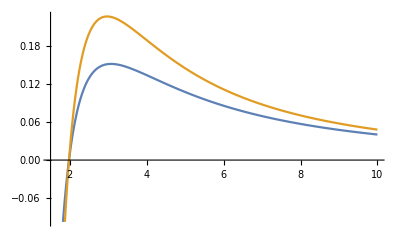

```mathematica
Plot[{V1RNeM/.M->1/.e->0.2/.λ->6,V2RNeM/.M->1/.e->0.2/.λ->6},{r,1.5,10}]
```

### Paper verification

In the following we set the potential obtained by Moncrief (1974) to compare the above expressions

```mathematica
Λpaper[r]=λ-2 + (6M)/r-(4 e^2)/r^2;
Spaper[r]=λ/(r^3 Λpaper[r])+(2 √A[r] √B[r])/(r^3 Λpaper[r]^2)(λ-2 + (4 e^2)/r^2)-1/(r^3 Λpaper[r])((2M)/r-(2 e^2)/r^2)/.Example1Functions//FullSimplify;
Vpaper[r]=(√A[r] √B[r])/(r Λpaper[r])^2((8 e^2)/r^2-(6M)/r)^2 +(8 e^2 √A[r] √B[r])/(r^4 Λpaper[r]) + (λ (λ-2))/(r^2 Λpaper[r])+(3M)/r^3+(4 e^2)/(r^4 Λpaper[r])(2-(6M)/r+(4 e^2)/r^2)/.Example1Functions//FullSimplify;
σpaper[r]=√(9 M^2+4 e^2 (-2+λ));

VMoncriefnoDiag=√A[r] √B[r](Vpaper[r] IdentityMatrix[2] +Spaper[r].({{3M, -2e √(λ-2)}, {-2e √(λ-2), -3M}})) /.Example1Functions //Simplify;

V1Moncrief=√A[r] √B[r](Vpaper[r] + σpaper[r]Spaper[r]) /.Example1Functions /.{rn->M-√(-e^2+M^2),rp->M+√(-e^2+M^2)};
V2Moncrief=√A[r] √B[r](Vpaper[r] - σpaper[r]Spaper[r]) /.Example1Functions /.{rn->M-√(-e^2+M^2),rp->M+√(-e^2+M^2)};
```

Checking the potentials:

```mathematica
V2RN-V1Moncrief/.{rn->M-√(-e^2+M^2),rp->M+√(-e^2+M^2)}//Simplify
V1RN-V2Moncrief/.{rn->M-√(-e^2+M^2),rp->M+√(-e^2+M^2)}//Simplify
```

0

0

```mathematica
Clear[E1matrixK,E1matrixL,E1matrixM,E1matrixD,E1matrixS,E1matrixC,E1matrixB,Example1Functions]
```

## Example 2: BH in Einstein-Maxwell-dilaton theory

For this example, we use the theory described in [arXiv: gr-qc/0005125].
The metric and field variables are given by

```mathematica
$Assumptions={r>0,λ>2,M>0};
```

The Lagrangian functions are

```mathematica
Example2Functions={f1->Function[ϕ,2],

				f2->Function[{ϕF,Xϕ,FF}, -4Exp[-2 ϕF]FF +4 Xϕ],

				A->Function[r,-(1-(2M)/r)],
				B->Function[r,-(1-(2M)/r)],
				c->Function[r,-r(r-Q^2/M)],
				A0->Function[r,-Q/r],
				ϕ->Function[r,1/2 Log[1-Q^2/(M r)]]};
```

Checking that the above relations satisfy the background equations

```mathematica
Simplify[{EquA,EquB, EquC, EquA0,Equϕ}/.Example2Functions]
```

{0,0,0,0,0}

```mathematica
E2matrixK=Simplify[matrixK/.Example2Functions];
E2matrixL=Simplify[matrixL/.Example2Functions];
E2matrixD=Simplify[matrixD/.Example2Functions];
E2matrixM=Simplify[matrixM/.Example2Functions];
```

Now, we proceed to compute the potential. First, we compute the matrix C

```mathematica
E2matrixC=Simplify[1/2 Inverse[E2matrixL].(D[E2matrixL,r] - E2matrixD - 1/2(A'[r]/A[r] + B'[r]/B[r])E2matrixL)/.Example2Functions]//FullSimplify;
E2matrixC//MatrixForm
```

((-Q^8 r+156 M^3 Q^4 r^2-136 M^4 Q^2 r^3+48 M^5 r^4+2 M Q^6 (6 Q^2+r^2 (4+λ))-2 M^2 Q^4 r (39 Q^2+r^2 (4+λ)))/(2 r (Q^2-2 M r) (Q^2-M r) (4 M Q^4-Q^4 r+12 M^3 r^2+2 M^2 r (-7 Q^2+r^2 (-2+λ))-2 M Q^2 r^2 (-2+λ))) | 0 | (4 Q^2 (24 M^4 r^2+8 M^3 r (-3 Q^2+r^2 (-2+λ))+2 M^2 (Q^4+Q^2 r^2 (6-5 λ)-r^4 (-2+λ))-Q^4 (Q^2+r^2 λ)+2 M Q^2 r (r^2 (-2+λ)+2 Q^2 (1+λ))))/(r (Q^2-2 M r) ((Q^2-2 M r) (6 M^2 r+Q^2 r-2 M (2 Q^2+r^2))+2 M r^2 (Q^2-M r) λ))
(8 M Q (Q^2-2 M r))/(4 M Q^4-Q^4 r+12 M^3 r^2+2 M^2 r (-7 Q^2+r^2 (-2+λ))-2 M Q^2 r^2 (-2+λ)) | -Q^2/(2 Q^2 r-2 M r^2) | -(16 Q^3 (2 M-r) (Q^2-2 M r))/(r (4 M Q^4-Q^4 r+12 M^3 r^2+2 M^2 r (-7 Q^2+r^2 (-2+λ))-2 M Q^2 r^2 (-2+λ)))
-(M^2 Q^2 r)/((Q^2-2 M r) ((Q^2-2 M r) (4 M Q^2-(6 M^2+Q^2) r+2 M r^2)+2 M r^2 (-Q^2+M r) λ)) | 0 | (Q^2-2 M r)/(2 Q^2 r-2 M r^2)+(2 M Q^4 (2 M-r))/((Q^2-2 M r) ((Q^2-2 M r) (4 M Q^2-(6 M^2+Q^2) r+2 M r^2)+2 M r^2 (-Q^2+M r) λ)))

Now, the matrix B is given by

```mathematica
E2matrixB=Simplify[E2matrixL.(E2matrixC.E2matrixC - D[E2matrixC,r]) - D[E2matrixL,r].E2matrixC + E2matrixD .E2matrixC + E2matrixM - 1/2 D[E2matrixD,r]]//FullSimplify ;
E2matrixB//MatrixForm
```

((M (-6 Q^18 r^3-2304 M^11 r^10 (-2+λ)+Q^16 r^5 (-1+λ)+2 M Q^14 r^2 (-14 Q^4+Q^2 r^2 (63-31 λ)+r^4 (-2+λ) (-5+4 λ))+384 M^10 r^7 (12 Q^4-3 r^4 (-2+λ)^2+Q^2 r^2 (-74+25 λ))-64 M^9 r^6 (412 Q^6+3 r^6 (-2+λ)^3-2 Q^2 r^4 (-2+λ) (-110+31 λ)+6 Q^4 r^2 (-187+41 λ))+8 M^6 Q^4 r^3 (4756 Q^8+2 Q^6 r^2 (261+38 λ)+Q^4 r^4 (-9968+(5517-298 λ) λ)-r^8 (-2+λ)^2 (6+λ (-43+26 λ))-4 Q^2 r^6 (-2+λ) (-612+λ (158+61 λ)))-16 M^7 Q^2 r^4 (3864 Q^8-8 r^8 (-2+λ)^3 λ+3 Q^6 r^2 (-938+111 λ)-Q^2 r^6 (-2+λ) (-812+λ (332+25 λ))-2 Q^4 r^4 (3216+λ (-1718+73 λ)))-32 M^8 r^5 (-1768 Q^8+Q^6 r^2 (2720-397 λ)+r^8 (-2+λ)^3 λ-Q^2 r^6 (-2+λ)^2 (-74+13 λ)+Q^4 r^4 (2314+λ (-1425+143 λ)))-8 M^5 Q^6 r^2 (1670 Q^8+Q^6 r^2 (2089-149 λ)+Q^4 r^4 (-4168+(2993-450 λ) λ)-r^8 (-2+λ)^2 (18+λ (-17+22 λ))-Q^2 r^6 (-2+λ) (-2184+λ (497+275 λ)))+2 M^2 Q^12 r (64 Q^6+8 Q^4 r^2 (19-5 λ)-2 Q^2 r^4 (302+λ (-267+56 λ))+r^6 (-66+λ (53+2 λ-6 λ^2)))-4 M^3 Q^10 (48 Q^8+28 Q^6 r^2 (15-2 λ)+2 Q^4 r^4 (57+(99-62 λ) λ)-Q^2 r^6 (1566+λ (-1415+214 λ+50 λ^2))+2 r^8 (-52+λ (24+9 λ-2 λ^3)))+4 M^4 Q^8 r (624 Q^8+6 Q^6 r^2 (339-40 λ)+Q^4 r^4 (-1465+(1869-572 λ) λ)-2 Q^2 r^6 (-2+λ) (-1187+2 λ (177+67 λ))-r^8 (-2+λ) (-86+λ (11+λ (-23+20 λ))))))/(2 r^2 (-Q^2+M r) (4 M Q^4-Q^4 r+12 M^3 r^2+2 M^2 r (-7 Q^2+r^2 (-2+λ))-2 M Q^2 r^2 (-2+λ))^4 λ) | (Q (3 Q^14 r^3+384 M^9 (3 Q^2 r^6-2 r^8 (1+λ))-64 M^8 (94 Q^4 r^5+6 r^9 (-2+λ) (1+λ)-9 Q^2 r^7 (4+5 λ))+2 M Q^12 r^2 (7 Q^2+r^2 (-21+8 λ))-32 M^7 r^4 (-348 Q^6+2 r^6 (-2+λ)^2 (1+λ)-Q^2 r^4 (-2+λ) (48+41 λ)+3 Q^4 r^2 (1+46 λ))-16 M^6 Q^2 r^3 (618 Q^6+Q^4 r^2 (335-233 λ)-3 r^6 (-2+λ)^2 (6+5 λ)+2 Q^2 r^4 (-2+λ) (64+47 λ))-4 M^2 Q^10 r (16 Q^4+3 Q^2 r^2 (13-6 λ)+r^4 (-66+(46-7 λ) λ))+8 M^3 Q^8 (12 Q^6+5 Q^4 r^2 (19-4 λ)-3 r^6 (38-27 λ+2 λ^3)+Q^2 r^4 (65-λ (22+13 λ)))+8 M^5 Q^4 r^2 (571 Q^6+Q^4 r^2 (817-260 λ)+3 Q^2 r^4 (-80+λ (-8+21 λ))-r^6 (-2+λ) (-126+λ (-19+42 λ)))-4 M^4 Q^6 r (264 Q^6+3 Q^4 r^2 (275-68 λ)-2 Q^2 r^4 (-32+λ (5+22 λ))-r^6 (-2+λ) (-226+λ (11+52 λ)))))/(8 r^3 (-Q^2+M r) (4 M Q^4-Q^4 r+12 M^3 r^2+2 M^2 r (-7 Q^2+r^2 (-2+λ))-2 M Q^2 r^2 (-2+λ))^3 λ) | (Q^2 (-4608 M^12 r^10 (4+7 λ)+Q^16 r^4 (-12 Q^2+r^2 (-2+3 λ))+2 M Q^14 r^3 (-16 Q^4+Q^2 r^2 (128-81 λ)+r^4 (-2+λ) (-10+13 λ))-1536 M^11 r^7 (12 Q^4-Q^2 r^2 (74+83 λ)+6 r^4 (-3+2 (-2+λ) λ))-128 M^10 r^6 (-824 Q^6+3 Q^4 r^2 (724+483 λ)+4 Q^2 r^4 (331+2 (121-76 λ) λ)+6 r^6 (-2+λ) (-10+λ (-15+4 λ)))+2 M^2 Q^12 r^2 (184 Q^6+4 Q^4 r^2 (13+34 λ)+Q^2 r^4 (-1248+(1431-370 λ) λ)-r^6 (-2+λ) (-66+λ (37+10 λ)))+64 M^9 r^5 (-3536 Q^8+Q^6 r^2 (4616+1581 λ)+Q^4 r^4 (6872+11 (161-179 λ) λ)+2 r^8 (-2+λ)^2 (6+λ (13+λ))+8 Q^2 r^6 (-2+λ) (-92+λ (-84+29 λ)))+32 M^8 r^4 (7728 Q^10+r^10 (-2+λ)^3 λ (2+λ)+2 Q^8 r^2 (-1046+387 λ)-2 Q^2 r^8 (-2+λ)^2 (74+λ (109+6 λ))+Q^6 r^4 (-18304+λ (2181+2716 λ))+Q^4 r^6 (-7876+λ (344+(3611-925 λ) λ)))+8 M^6 Q^4 r^2 (6680 Q^10+4 Q^8 r^2 (4467+740 λ)+Q^6 r^4 (-15628+(22269-4042 λ) λ)+Q^4 r^6 (-37408+λ (26510+3 (185-744 λ) λ))+r^10 (-2+λ)^2 (-12+λ (-116+3 λ (-1+8 λ)))+Q^2 r^8 (-2+λ) (5040+λ (482+λ (-1381+14 λ))))-8 M^5 Q^6 r (1248 Q^10+8 Q^8 r^2 (926+31 λ)+Q^6 r^4 (1248+(8079-2296 λ) λ)-Q^4 r^6 (17832+λ (-19138+3471 λ+666 λ^2))+Q^2 r^8 (-2+λ) (4540+λ (-844+15 λ (-51+2 λ)))+r^10 (-2+λ)^2 (-36+λ (-124+λ (-9+16 λ))))-16 M^7 Q^2 r^3 (9512 Q^10+8 r^10 (-2+λ)^3 λ (2+λ)+17 Q^8 r^2 (516+209 λ)+Q^6 r^4 (-25564+λ (13631+187 λ))+Q^4 r^6 (-22656+λ (8844+(4972-1937 λ) λ))-Q^2 r^8 (-2+λ) (-1648+λ (-742+λ (709+19 λ))))-4 M^3 Q^10 r (224 Q^8-104 Q^6 r^2 (-11+λ)+Q^4 r^4 (-980+(2327-744 λ) λ)-2 r^8 (-2+λ) (-52+λ (-16+λ (19+3 λ)))-3 Q^2 r^6 (1088+λ (-1259+λ (309+22 λ))))+4 M^4 Q^8 (192 Q^10+16 Q^8 r^2 (183-8 λ)+4 Q^6 r^4 (1131+498 λ-208 λ^2)+2 Q^2 r^8 (-2+λ) (2478+λ (-1111+5 λ (-47+2 λ)))-Q^4 r^6 (9194+λ (-14269+4 λ (1009+40 λ)))+r^10 (-2+λ) (172+λ (220+λ (-121-34 λ+8 λ^2))))))/(2 r^3 (-Q^2+M r) (4 M Q^4-Q^4 r+12 M^3 r^2+2 M^2 r (-7 Q^2+r^2 (-2+λ))-2 M Q^2 r^2 (-2+λ))^4 λ)
(Q (3 Q^14 r^3+384 M^9 (3 Q^2 r^6-2 r^8 (1+λ))-64 M^8 (94 Q^4 r^5+6 r^9 (-2+λ) (1+λ)-9 Q^2 r^7 (4+5 λ))+2 M Q^12 r^2 (7 Q^2+r^2 (-21+8 λ))-32 M^7 r^4 (-348 Q^6+2 r^6 (-2+λ)^2 (1+λ)-Q^2 r^4 (-2+λ) (48+41 λ)+3 Q^4 r^2 (1+46 λ))-16 M^6 Q^2 r^3 (618 Q^6+Q^4 r^2 (335-233 λ)-3 r^6 (-2+λ)^2 (6+5 λ)+2 Q^2 r^4 (-2+λ) (64+47 λ))-4 M^2 Q^10 r (16 Q^4+3 Q^2 r^2 (13-6 λ)+r^4 (-66+(46-7 λ) λ))+8 M^3 Q^8 (12 Q^6+5 Q^4 r^2 (19-4 λ)-3 r^6 (38-27 λ+2 λ^3)+Q^2 r^4 (65-λ (22+13 λ)))+8 M^5 Q^4 r^2 (571 Q^6+Q^4 r^2 (817-260 λ)+3 Q^2 r^4 (-80+λ (-8+21 λ))-r^6 (-2+λ) (-126+λ (-19+42 λ)))-4 M^4 Q^6 r (264 Q^6+3 Q^4 r^2 (275-68 λ)-2 Q^2 r^4 (-32+λ (5+22 λ))-r^6 (-2+λ) (-226+λ (11+52 λ)))))/(8 r^3 (-Q^2+M r) (4 M Q^4-Q^4 r+12 M^3 r^2+2 M^2 r (-7 Q^2+r^2 (-2+λ))-2 M Q^2 r^2 (-2+λ))^3 λ) | -(3 Q^12 r^3+576 M^8 r^5 (-Q^2+r^2 λ)+32 M^7 (85 Q^4 r^4+10 Q^2 r^6 (1-5 λ)+6 r^8 (-2+λ) λ)+2 M Q^10 r^2 (7 Q^2+2 r^2 (-7+2 λ))+16 M^6 r^3 (-263 Q^6+r^6 (-2+λ)^2 λ-Q^2 r^4 (-2+λ) (2+31 λ)+Q^4 r^2 (-121+113 λ))-4 M^2 Q^8 r (16 Q^4+2 Q^2 r^2 (16-9 λ)+r^4 (-26+λ (10+λ)))-4 M^4 Q^4 r (216 Q^6+Q^4 r^2 (541-156 λ)+2 Q^2 r^4 (58+λ (-65+4 λ))-r^6 (-2+λ) (-22+λ (-17+12 λ)))+8 M^5 Q^2 r^2 (355 Q^6+4 Q^4 r^2 (100-39 λ)-2 r^6 (-2+λ)^2 (1+3 λ)+Q^2 r^4 (16+λ (-114+47 λ)))+8 M^3 Q^6 (12 Q^6+Q^4 r^2 (79-20 λ)+Q^2 r^4 (49-λ (32+5 λ))+r^6 (-24+λ (6+(7-2 λ) λ))))/(64 M r^4 (-Q^2+M r) (4 M Q^4-Q^4 r+12 M^3 r^2+2 M^2 r (-7 Q^2+r^2 (-2+λ))-2 M Q^2 r^2 (-2+λ))^2 λ) | (Q (-3 Q^12 r^3+2 M Q^10 r^2 (2 Q^2+r^2 (11-3 λ))+576 M^8 (2 Q^2 r^5-r^7 λ)-64 M^7 (55 Q^4 r^4+Q^2 r^6 (16-29 λ)+3 r^8 (-2+λ) λ)-16 M^5 Q^2 r^2 (139 Q^6+2 Q^4 r^2 (97-52 λ)-r^6 (-2+λ) λ (-5+3 λ)+Q^2 r^4 (-5+3 λ) (-8+11 λ))+8 M^4 Q^4 r (69 Q^6+Q^4 r^2 (185-81 λ)-r^6 (-2+λ) (-2-9 λ+6 λ^2)+Q^2 r^4 (73+6 λ (-15+4 λ)))+2 M^2 Q^8 r (6 Q^4+Q^2 r^2 (9-20 λ)+r^4 (-30+λ (9+4 λ)))+16 M^6 (256 Q^6 r^3+Q^4 r^5 (182-151 λ)-r^9 (-2+λ)^2 λ+2 Q^2 r^7 (8+λ (-35+17 λ)))-4 M^3 Q^6 (12 Q^6+6 Q^4 r^2 (12-5 λ)+2 Q^2 r^4 (-1+λ) (-27+2 λ)-r^6 (18+λ (5+4 (-4+λ) λ)))))/(4 M r^4 (-Q^2+M r) (4 M Q^4-Q^4 r+12 M^3 r^2+2 M^2 r (-7 Q^2+r^2 (-2+λ))-2 M Q^2 r^2 (-2+λ))^2 λ)
(Q^2 (-4608 M^12 r^10 (4+7 λ)+Q^16 r^4 (-12 Q^2+r^2 (-2+3 λ))+2 M Q^14 r^3 (-16 Q^4+Q^2 r^2 (128-81 λ)+r^4 (-2+λ) (-10+13 λ))-1536 M^11 r^7 (12 Q^4-Q^2 r^2 (74+83 λ)+6 r^4 (-3+2 (-2+λ) λ))-128 M^10 r^6 (-824 Q^6+3 Q^4 r^2 (724+483 λ)+4 Q^2 r^4 (331+2 (121-76 λ) λ)+6 r^6 (-2+λ) (-10+λ (-15+4 λ)))+2 M^2 Q^12 r^2 (184 Q^6+4 Q^4 r^2 (13+34 λ)+Q^2 r^4 (-1248+(1431-370 λ) λ)-r^6 (-2+λ) (-66+λ (37+10 λ)))+64 M^9 r^5 (-3536 Q^8+Q^6 r^2 (4616+1581 λ)+Q^4 r^4 (6872+11 (161-179 λ) λ)+2 r^8 (-2+λ)^2 (6+λ (13+λ))+8 Q^2 r^6 (-2+λ) (-92+λ (-84+29 λ)))+32 M^8 r^4 (7728 Q^10+r^10 (-2+λ)^3 λ (2+λ)+2 Q^8 r^2 (-1046+387 λ)-2 Q^2 r^8 (-2+λ)^2 (74+λ (109+6 λ))+Q^6 r^4 (-18304+λ (2181+2716 λ))+Q^4 r^6 (-7876+λ (344+(3611-925 λ) λ)))+8 M^6 Q^4 r^2 (6680 Q^10+4 Q^8 r^2 (4467+740 λ)+Q^6 r^4 (-15628+(22269-4042 λ) λ)+Q^4 r^6 (-37408+λ (26510+3 (185-744 λ) λ))+r^10 (-2+λ)^2 (-12+λ (-116+3 λ (-1+8 λ)))+Q^2 r^8 (-2+λ) (5040+λ (482+λ (-1381+14 λ))))-8 M^5 Q^6 r (1248 Q^10+8 Q^8 r^2 (926+31 λ)+Q^6 r^4 (1248+(8079-2296 λ) λ)-Q^4 r^6 (17832+λ (-19138+3471 λ+666 λ^2))+Q^2 r^8 (-2+λ) (4540+λ (-844+15 λ (-51+2 λ)))+r^10 (-2+λ)^2 (-36+λ (-124+λ (-9+16 λ))))-16 M^7 Q^2 r^3 (9512 Q^10+8 r^10 (-2+λ)^3 λ (2+λ)+17 Q^8 r^2 (516+209 λ)+Q^6 r^4 (-25564+λ (13631+187 λ))+Q^4 r^6 (-22656+λ (8844+(4972-1937 λ) λ))-Q^2 r^8 (-2+λ) (-1648+λ (-742+λ (709+19 λ))))-4 M^3 Q^10 r (224 Q^8-104 Q^6 r^2 (-11+λ)+Q^4 r^4 (-980+(2327-744 λ) λ)-2 r^8 (-2+λ) (-52+λ (-16+λ (19+3 λ)))-3 Q^2 r^6 (1088+λ (-1259+λ (309+22 λ))))+4 M^4 Q^8 (192 Q^10+16 Q^8 r^2 (183-8 λ)+4 Q^6 r^4 (1131+498 λ-208 λ^2)+2 Q^2 r^8 (-2+λ) (2478+λ (-1111+5 λ (-47+2 λ)))-Q^4 r^6 (9194+λ (-14269+4 λ (1009+40 λ)))+r^10 (-2+λ) (172+λ (220+λ (-121-34 λ+8 λ^2))))))/(2 r^3 (-Q^2+M r) (4 M Q^4-Q^4 r+12 M^3 r^2+2 M^2 r (-7 Q^2+r^2 (-2+λ))-2 M Q^2 r^2 (-2+λ))^4 λ) | (Q (-3 Q^12 r^3+2 M Q^10 r^2 (2 Q^2+r^2 (11-3 λ))+576 M^8 (2 Q^2 r^5-r^7 λ)-64 M^7 (55 Q^4 r^4+Q^2 r^6 (16-29 λ)+3 r^8 (-2+λ) λ)-16 M^5 Q^2 r^2 (139 Q^6+2 Q^4 r^2 (97-52 λ)-r^6 (-2+λ) λ (-5+3 λ)+Q^2 r^4 (-5+3 λ) (-8+11 λ))+8 M^4 Q^4 r (69 Q^6+Q^4 r^2 (185-81 λ)-r^6 (-2+λ) (-2-9 λ+6 λ^2)+Q^2 r^4 (73+6 λ (-15+4 λ)))+2 M^2 Q^8 r (6 Q^4+Q^2 r^2 (9-20 λ)+r^4 (-30+λ (9+4 λ)))+16 M^6 (256 Q^6 r^3+Q^4 r^5 (182-151 λ)-r^9 (-2+λ)^2 λ+2 Q^2 r^7 (8+λ (-35+17 λ)))-4 M^3 Q^6 (12 Q^6+6 Q^4 r^2 (12-5 λ)+2 Q^2 r^4 (-1+λ) (-27+2 λ)-r^6 (18+λ (5+4 (-4+λ) λ)))))/(4 M r^4 (-Q^2+M r) (4 M Q^4-Q^4 r+12 M^3 r^2+2 M^2 r (-7 Q^2+r^2 (-2+λ))-2 M Q^2 r^2 (-2+λ))^2 λ) | (-165888 M^15 r^12 λ+27648 M^14 r^11 (31 Q^2+r^2 (8-7 λ)) λ+Q^20 r^5 (-12 Q^2+r^2 (-2+5 λ))+2 M Q^18 r^4 (-4 Q^4+Q^2 r^2 (130-113 λ)+2 r^4 (-2+λ) (-5+12 λ))-4608 M^13 r^10 (6 Q^2 r^2 (40-37 λ) λ+6 r^4 (-2+λ) λ (-2+3 λ)+Q^4 (-8+421 λ))+4 M^2 Q^16 r^3 (108 Q^6+2 Q^4 r^2 (-51+130 λ)+3 r^6 (-2+λ) (11+2 (-9+λ) λ)-2 Q^2 r^4 (322+3 λ (-173+54 λ)))+768 M^12 r^7 (48 Q^8-2 r^8 (-2+λ)^2 λ (-4+11 λ)+6 Q^2 r^6 (-2+λ) λ (-58+95 λ)+4 Q^6 r^2 (-74+863 λ)-3 Q^4 r^4 (32+λ (-1047+1012 λ)))-8 M^3 Q^14 r^2 (204 Q^8+2 Q^6 r^2 (299+105 λ)-2 Q^4 r^4 (557+3 λ (-492+157 λ))-2 r^8 (-2+λ) (-26+λ (17+λ (-8+5 λ)))+Q^2 r^6 (-1698+λ (2911+2 λ (-571+30 λ))))-64 M^10 r^5 (-7072 Q^12+Q^10 r^2 (7584-36967 λ)+r^12 (-2+λ)^4 λ^2-Q^2 r^10 (-2+λ)^3 λ (-18+133 λ)+Q^8 r^4 (18088+λ (-55316+41011 λ))+4 Q^6 r^6 (1398+λ (-5869+5 (2499-946 λ) λ))+12 Q^4 r^8 (-2+λ) (-14+λ (138+5 λ (-117+50 λ))))-128 M^11 r^6 (1648 Q^10+r^10 (-2+λ)^3 λ (-2+13 λ)-16 Q^2 r^8 (-2+λ)^2 λ (-14+43 λ)+Q^8 r^2 (-4200+21103 λ)-4 Q^6 r^4 (884+λ (-6349+5949 λ))+12 Q^4 r^6 (-38+λ (727+2 λ (-824+319 λ))))-32 M^9 Q^2 r^4 (15456 Q^12-10 r^12 (-2+λ)^4 λ^2+Q^10 r^2 (2888+53575 λ)-2 Q^8 r^4 (22920+λ (-55344+26507 λ))+Q^2 r^10 (-2+λ)^2 (-24+λ (80+13 λ (-96+43 λ)))-16 Q^4 r^8 (-2+λ) (-129+λ (223+λ (-1079+441 λ)))+2 Q^6 r^6 (-14748+λ (29186+λ (-41950+14097 λ))))-16 M^5 Q^10 (96 Q^12+8 Q^10 r^2 (261+10 λ)+2 Q^8 r^4 (2983+30 (71-14 λ) λ)+Q^6 r^6 (-3973+2 λ (11671-4052 λ+74 λ^2))+Q^4 r^8 (-13872+λ (26431+λ (-11529+4 (277-13 λ) λ)))-r^12 (-2+λ)^2 (18+λ (63+λ (79+4 (-13+λ) λ)))+Q^2 r^10 (-2+λ) (2356+λ (-1709+2 λ (408+λ (-172+15 λ)))))+8 M^4 Q^12 r (320 Q^10+16 Q^8 r^2 (163+12 λ)+2 Q^6 r^4 (641+(3485-1056 λ) λ)+Q^4 r^6 (-7861+λ (18103-6994 λ+240 λ^2))+r^10 (-2+λ) (86+3 λ (17+λ (19+6 (-5+λ) λ)))-2 Q^2 r^8 (2582+λ (-3921+λ (1759+λ (-277+28 λ)))))+16 M^6 Q^8 r (1248 Q^12+4 Q^10 r^2 (2687+628 λ)+2 Q^8 r^4 (5091+4 (3745-831 λ) λ)+Q^6 r^6 (-25646+λ (72113+28 λ (-1000+51 λ)))+Q^4 r^8 (-27784+λ (43383+λ (-23815+5902 λ-732 λ^2)))-r^12 (-2+λ)^2 (6+λ (77+λ (157+2 λ (-67+10 λ))))+Q^2 r^10 (-2+λ) (2592+λ (-1018+λ (2197+4 λ (-397+59 λ)))))-64 M^7 Q^6 r^2 (1670 Q^12+Q^10 r^2 (6845+4257 λ)+Q^8 r^4 (-1714+(24017-6015 λ) λ)-r^12 (-2+λ)^3 λ (-6+λ (-29+10 λ))+Q^6 r^6 (-15743+4 λ (7894+λ (-3864+479 λ)))+Q^4 r^8 (-8184+λ (10714+λ (-9971+5136 λ-927 λ^2)))+Q^2 r^10 (-2+λ) (418+λ (-17+λ (1110+λ (-971+187 λ)))))+16 M^8 Q^4 r^3 (19024 Q^12+132 Q^10 r^2 (250+417 λ)+Q^8 r^4 (-55312+(178105-56716 λ) λ)-r^12 (-2+λ)^3 λ (-6+λ (-89+40 λ))+4 Q^2 r^10 (-2+λ)^2 (-74+λ (-35-778 λ+308 λ^2))+4 Q^6 r^6 (-20480+λ (35066+λ (-27340+6541 λ)))-2 Q^4 r^8 (11172+λ (-14194+λ (30702+λ (-22751+4794 λ))))))/(M r^4 (-Q^2+M r) (4 M Q^4-Q^4 r+12 M^3 r^2+2 M^2 r (-7 Q^2+r^2 (-2+λ))-2 M Q^2 r^2 (-2+λ))^4 λ))

As shown in the paper, the potentials are given by the  eigenvalues of the matrix −K^-1B.

```mathematica
innerV = -Inverse[E2matrixK] . E2matrixB  //Simplify  ;
```

```mathematica
TotalEigenVals=Table[Eigenvalues[innerV/.M->1/.Q->0.4/.λ->6/.r->ro],{ro,2,50,0.1}] ;
```

```mathematica
numE2EigenVal1=TotalEigenVals⟦All,1⟧ ;
numE2EigenVal2=TotalEigenVals⟦All,2⟧ ;
numE2EigenVal3=TotalEigenVals⟦All,3⟧ ;
```

```mathematica
gridList = Table[ro,{ro,2,50,0.1}];
V1EMD = Interpolation[Table[{gridList⟦ii⟧,numE2EigenVal1⟦ii⟧},{ii,1,Length[gridList]}],r] ;
V2EMD = Interpolation[Table[{gridList⟦ii⟧,numE2EigenVal2⟦ii⟧},{ii,1,Length[gridList]}],r] ;
V3EMD = Interpolation[Table[{gridList⟦ii⟧,numE2EigenVal3⟦ii⟧},{ii,1,Length[gridList]}],r] ;
```

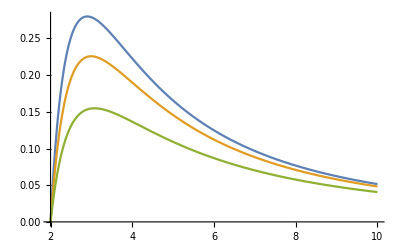

```mathematica
Plot[{V1EMD, V2EMD, V3EMD},{r,2,10}]
```

```mathematica
Clear[V1EMD, V2EMD, V3EMD,E2matrixK,E2matrixL,E2matrixM,E2matrixD,Example2Functions]
```